```mathematica
Quit
```

Here Alex is set as reference surface and Sophie is the target surface .

```mathematica
SetDirectory[NotebookDirectory[]];
```

Read in mat file

```mathematica
Import["BaseSurface-Alex/OutputForLibigl/Mesh2/Alex_Mesh2_FaceRemesh.csv","Elements"]
```

{Data,Dataset,Dimensions,Grid,MaxColumnCount,RawData,RowCount,Summary}

The original meshes

```mathematica
FaceRef=Import["BaseSurface-Alex/OutputForLibigl/Mesh2/Alex_Mesh2_FaceRemesh.csv","Data"];
```

```mathematica
FaceTar=Import["TargetSurface-Sophie/OutputForLibigl/Mesh2/Sophie_Mesh2_FaceRemesh.csv","Data"];
```

```mathematica
VerticeRef=Import["BaseSurface-Alex/OutputForLibigl/Mesh2/Alex_Mesh2_VerticeRemesh.csv","Data"];
VerticeTar=Import["TargetSurface-Sophie/OutputForLibigl/Mesh2/Sophie_Mesh2_VerticeRemesh.csv","Data"];
```

```mathematica
Dimensions[FaceRef]
```

{9606,3}

```mathematica
Dimensions[VerticeRef]
```

{4908,3}

The parameterization results

```mathematica
UVRef=Import["BaseSurface-Alex/OutputForLibigl/Mesh2/Alex_Mesh2_UVRemesh.csv","Data"];
UVTar=Import["TargetSurface-Sophie/OutputForLibigl/Mesh2/Sophie_Mesh2_UVRemesh.csv","Data"];
```

Data check

```mathematica
If[FaceRef==FaceTar&&Dimensions[VerticeRef]==Dimensions[VerticeTar]&&UVRef==UVTar,"Pass","Data error"]
```

Pass

If pass

```mathematica
UV=UVRef;
Face=FaceRef;
```

The principal directions and curvatures of the reference surface

```mathematica
PD1Ref=Import["BaseSurface-Alex/OutputForLibigl/Mesh2/Alex_Mesh2_PD1.txt","Data"];
PD2Ref=Import["BaseSurface-Alex/OutputForLibigl/Mesh2/Alex_Mesh2_PD2.txt","Data"];
k1Ref=Flatten[Import["BaseSurface-Alex/OutputForLibigl/Mesh2/Alex_Mesh2_k1.txt","Data"]];
k2Ref=Flatten[Import["BaseSurface-Alex/OutputForLibigl/Mesh2/Alex_Mesh2_k2.txt","Data"]];
```

The principal directions and curvatures of the target surface

```mathematica
PD1Tar=Import["TargetSurface-Sophie/OutputForLibigl/Mesh2/Sophie_Mesh2_PD1.txt","Data"];
PD2Tar=Import["TargetSurface-Sophie/OutputForLibigl/Mesh2/Sophie_Mesh2_PD2.txt","Data"];
k1Tar=Flatten[Import["TargetSurface-Sophie/OutputForLibigl/Mesh2/Sophie_Mesh2_k1.txt","Data"]];
k2Tar=Flatten[Import["TargetSurface-Sophie/OutputForLibigl/Mesh2/Sophie_Mesh2_k2.txt","Data"]];
```

```mathematica
nNodes=Dimensions[VerticeRef][[1]]
nFaces=Dimensions[Face][[1]]
```

4908

9606

计算混合积

```mathematica
MixProd=Table[({UV[[Face[[n,1]],1]],UV[[Face[[n,1]],2]],1.0}).({UV[[Face[[n,2]],1]],UV[[Face[[n,2]],2]],1.0}×{UV[[Face[[n,3]],1]],UV[[Face[[n,3]],2]],1.0}),{n,1,nFaces}];
```

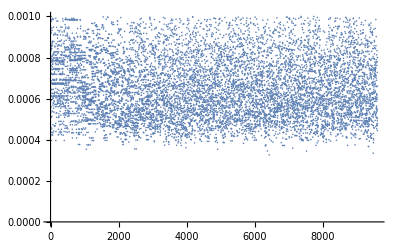

```mathematica
ListPlot[MixProd,PlotRange->All]
```

```mathematica
ii=1;Tabii={};While[ii≤ nFaces,If[MixProd[[ii]]< 0,AppendTo[Tabii,ii]];ii++];
```

```mathematica
Tabii
```

{}

```mathematica
Table[{{VerticeRef[[Face[[n,1]],1]],VerticeRef[[Face[[n,1]],2]],VerticeRef[[Face[[n,1]],3]]},{VerticeRef[[Face[[n,2]],1]],VerticeRef[[Face[[n,2]],2]],VerticeRef[[Face[[n,2]],3]]},{VerticeRef[[Face[[n,3]],1]],VerticeRef[[Face[[n,3]],2]],VerticeRef[[Face[[n,3]],3]]}},{n,1,nFaces}];
ModelRef=Graphics3D[Polygon[%]];
```

```mathematica
Table[{{VerticeTar[[Face[[n,1]],1]],VerticeTar[[Face[[n,1]],2]],VerticeTar[[Face[[n,1]],3]]},{VerticeTar[[Face[[n,2]],1]],VerticeTar[[Face[[n,2]],2]],VerticeTar[[Face[[n,2]],3]]},{VerticeTar[[Face[[n,3]],1]],VerticeTar[[Face[[n,3]],2]],VerticeTar[[Face[[n,3]],3]]}},{n,1,nFaces}];
ModelTar=Graphics3D[Polygon[%]];
```

```mathematica
Show[ModelRef,ModelTar]
```

-Graphics3D-

```mathematica
Table[{{UV[[Face[[n,1]],1]],UV[[Face[[n,1]],2]],0},{UV[[Face[[n,2]],1]],UV[[Face[[n,2]],2]],0},{UV[[Face[[n,3]],1]],UV[[Face[[n,3]],2]],0}},{n,1,nFaces}];
UVPlane=Graphics3D[Polygon[%]]
```

-Graphics3D-

```mathematica
Show[ModelRef,UVPlane,ModelTar]
```

-Graphics3D-

compute the linear parametric equation for each face based on the formulations below
-Graphics-

{K11, K12, K13, K14}

```mathematica
MatK1Ref=Table[Inverse[{{1,UV[[Face[[n,1]],1]],UV[[Face[[n,1]],2]],UV[[Face[[n,1]],1]]*UV[[Face[[n,1]],2]]},{1,UV[[Face[[n,2]],1]],UV[[Face[[n,2]],2]],UV[[Face[[n,2]],1]]*UV[[Face[[n,2]],2]]},{1,UV[[Face[[n,3]],1]],UV[[Face[[n,3]],2]],UV[[Face[[n,3]],1]]*UV[[Face[[n,3]],2]]},{1,1/3(UV[[Face[[n,1]],1]]+UV[[Face[[n,2]],1]]+UV[[Face[[n,3]],1]]),1/3(UV[[Face[[n,1]],2]]+UV[[Face[[n,2]],2]]+UV[[Face[[n,3]],2]]),1/3(UV[[Face[[n,1]],1]]+UV[[Face[[n,2]],1]]+UV[[Face[[n,3]],1]])*1/3(UV[[Face[[n,1]],2]]+UV[[Face[[n,2]],2]]+UV[[Face[[n,3]],2]])}}].{VerticeRef[[Face[[n,1]],1]],VerticeRef[[Face[[n,2]],1]],VerticeRef[[Face[[n,3]],1]],1/3(VerticeRef[[Face[[n,1]],1]]+VerticeRef[[Face[[n,2]],1]]+VerticeRef[[Face[[n,3]],1]])},{n,1,nFaces}];
```

{K21, K22, K23}

```mathematica
MatK2Ref=Table[Inverse[{{1,UV[[Face[[n,1]],1]],UV[[Face[[n,1]],2]],UV[[Face[[n,1]],1]]*UV[[Face[[n,1]],2]]},{1,UV[[Face[[n,2]],1]],UV[[Face[[n,2]],2]],UV[[Face[[n,2]],1]]*UV[[Face[[n,2]],2]]},{1,UV[[Face[[n,3]],1]],UV[[Face[[n,3]],2]],UV[[Face[[n,3]],1]]*UV[[Face[[n,3]],2]]},{1,1/3(UV[[Face[[n,1]],1]]+UV[[Face[[n,2]],1]]+UV[[Face[[n,3]],1]]),1/3(UV[[Face[[n,1]],2]]+UV[[Face[[n,2]],2]]+UV[[Face[[n,3]],2]]),1/3(UV[[Face[[n,1]],1]]+UV[[Face[[n,2]],1]]+UV[[Face[[n,3]],1]])*1/3(UV[[Face[[n,1]],2]]+UV[[Face[[n,2]],2]]+UV[[Face[[n,3]],2]])}}].{VerticeRef[[Face[[n,1]],2]],VerticeRef[[Face[[n,2]],2]],VerticeRef[[Face[[n,3]],2]],1/3(VerticeRef[[Face[[n,1]],2]]+VerticeRef[[Face[[n,2]],2]]+VerticeRef[[Face[[n,3]],2]])},{n,1,nFaces}];
```

{K31, K32, K33}

```mathematica
MatK3Ref=Table[Inverse[{{1,UV[[Face[[n,1]],1]],UV[[Face[[n,1]],2]],UV[[Face[[n,1]],1]]*UV[[Face[[n,1]],2]]},{1,UV[[Face[[n,2]],1]],UV[[Face[[n,2]],2]],UV[[Face[[n,2]],1]]*UV[[Face[[n,2]],2]]},{1,UV[[Face[[n,3]],1]],UV[[Face[[n,3]],2]],UV[[Face[[n,3]],1]]*UV[[Face[[n,3]],2]]},{1,1/3(UV[[Face[[n,1]],1]]+UV[[Face[[n,2]],1]]+UV[[Face[[n,3]],1]]),1/3(UV[[Face[[n,1]],2]]+UV[[Face[[n,2]],2]]+UV[[Face[[n,3]],2]]),1/3(UV[[Face[[n,1]],1]]+UV[[Face[[n,2]],1]]+UV[[Face[[n,3]],1]])*1/3(UV[[Face[[n,1]],2]]+UV[[Face[[n,2]],2]]+UV[[Face[[n,3]],2]])}}].{VerticeRef[[Face[[n,1]],3]],VerticeRef[[Face[[n,2]],3]],VerticeRef[[Face[[n,3]],3]],1/3(VerticeRef[[Face[[n,1]],3]]+VerticeRef[[Face[[n,2]],3]]+VerticeRef[[Face[[n,3]],3]])},{n,1,nFaces}];
```

Check...

```mathematica
(*ListPlot[Table[MatK1Ref[[n,1]]+MatK1Ref[[n,2]]*UV[[Face[[n,1]],1]]+MatK1Ref[[n,3]]*UV[[Face[[n,1]],2]]+MatK1Ref[[n,4]]*UV[[Face[[n,1]],1]]*UV[[Face[[n,1]],2]]-VerticeRef[[Face[[n,1]],1]],{n,1,nFaces}],PlotRange->All]*)
```

```mathematica
(*ListPlot[Table[MatK2Ref[[n,1]]+MatK2Ref[[n,2]]*UV[[Face[[n,1]],1]]+MatK2Ref[[n,3]]*UV[[Face[[n,1]],2]]+MatK2Ref[[n,4]]*UV[[Face[[n,1]],1]]*UV[[Face[[n,1]],2]]-VerticeRef[[Face[[n,1]],2]],{n,1,nFaces}],PlotRange->All]*)
```

```mathematica
(*ListPlot[Table[MatK3Ref[[n,1]]+MatK3Ref[[n,2]]*UV[[Face[[n,1]],1]]+MatK3Ref[[n,3]]*UV[[Face[[n,1]],2]]+MatK3Ref[[n,4]]*UV[[Face[[n,1]],1]]*UV[[Face[[n,1]],2]]-VerticeRef[[Face[[n,1]],3]],{n,1,nFaces}],PlotRange->All]*)
```

Check passed...

compute the coefficients of the element-wise first fundamental form.
-Graphics-
-Graphics-

尝试用计数，在节点处求和，求平均的思路解决

For each element, calculate {E, F, G}, count how many times a node is called, then calculate the average .

```mathematica
TmprX=Table[{0,0,0,0},{n,1,nNodes}];
```

```mathematica
i=1;While[i<=nFaces,j=1;While[j<=3,TmprX[[Face[[i,j]]]]=TmprX[[Face[[i,j]]]]+{(MatK1Ref[[i,2]]+MatK1Ref[[i,4]]*UV[[Face[[i,j]],2]]),(MatK2Ref[[i,2]]+MatK2Ref[[i,4]]*UV[[Face[[i,j]],2]]),(MatK3Ref[[i,2]]+MatK3Ref[[i,4]]*UV[[Face[[i,j]],2]]),1};j++];i++]
```

```mathematica
TmprY=Table[{0,0,0,0},{n,1,nNodes}];
```

```mathematica
i=1;While[i<=nFaces,j=1;While[j<=3,TmprY[[Face[[i,j]]]]=TmprY[[Face[[i,j]]]]+{MatK1Ref[[i,3]]+MatK1Ref[[i,4]]*UV[[Face[[i,j]],1]],MatK2Ref[[i,3]]+MatK2Ref[[i,4]]*UV[[Face[[i,j]],1]],MatK3Ref[[i,3]]+MatK3Ref[[i,4]]*UV[[Face[[i,j]],1]],1};j++];i++]
```

```mathematica
rXRef=Table[{TmprX[[n,1]]/TmprX[[n,4]],TmprX[[n,2]]/TmprX[[n,4]],TmprX[[n,3]]/TmprX[[n,4]]},{n,1,nNodes}];
rYRef=Table[{TmprY[[n,1]]/TmprY[[n,4]],TmprY[[n,2]]/TmprY[[n,4]],TmprY[[n,3]]/TmprY[[n,4]]},{n,1,nNodes}];
```

```mathematica
EERef=Table[rXRef[[n]].rXRef[[n]],{n,1,nNodes}];
```

```mathematica
FFRef=Table[rXRef[[n]].rYRef[[n]],{n,1,nNodes}];
```

```mathematica
GGRef=Table[rYRef[[n]].rYRef[[n]],{n,1,nNodes}];
```

检查 EFG

```mathematica
Table[{UV[[n,1]],UV[[n,2]],EERef[[n]]},{n,1,nNodes}];
Table[{UV[[n,1]],UV[[n,2]],FFRef[[n]]},{n,1,nNodes}];
Table[{UV[[n,1]],UV[[n,2]],GGRef[[n]]},{n,1,nNodes}];
EFGPlotRef=ListPointPlot3D[{%%%,%%,%},PlotStyle->{Red,Green,Blue}]
```

-Graphics3D-

compute the linear parametric equation for each face based on the formulations below
-Graphics-

{K11, K12, K13, K14}

```mathematica
MatK1Tar=Table[Inverse[{{1,UV[[Face[[n,1]],1]],UV[[Face[[n,1]],2]],UV[[Face[[n,1]],1]]*UV[[Face[[n,1]],2]]},{1,UV[[Face[[n,2]],1]],UV[[Face[[n,2]],2]],UV[[Face[[n,2]],1]]*UV[[Face[[n,2]],2]]},{1,UV[[Face[[n,3]],1]],UV[[Face[[n,3]],2]],UV[[Face[[n,3]],1]]*UV[[Face[[n,3]],2]]},{1,1/3(UV[[Face[[n,1]],1]]+UV[[Face[[n,2]],1]]+UV[[Face[[n,3]],1]]),1/3(UV[[Face[[n,1]],2]]+UV[[Face[[n,2]],2]]+UV[[Face[[n,3]],2]]),1/3(UV[[Face[[n,1]],1]]+UV[[Face[[n,2]],1]]+UV[[Face[[n,3]],1]])*1/3(UV[[Face[[n,1]],2]]+UV[[Face[[n,2]],2]]+UV[[Face[[n,3]],2]])}}].{VerticeTar[[Face[[n,1]],1]],VerticeTar[[Face[[n,2]],1]],VerticeTar[[Face[[n,3]],1]],1/3(VerticeTar[[Face[[n,1]],1]]+VerticeTar[[Face[[n,2]],1]]+VerticeTar[[Face[[n,3]],1]])},{n,1,nFaces}];
```

{K21, K22, K23}

```mathematica
MatK2Tar=Table[Inverse[{{1,UV[[Face[[n,1]],1]],UV[[Face[[n,1]],2]],UV[[Face[[n,1]],1]]*UV[[Face[[n,1]],2]]},{1,UV[[Face[[n,2]],1]],UV[[Face[[n,2]],2]],UV[[Face[[n,2]],1]]*UV[[Face[[n,2]],2]]},{1,UV[[Face[[n,3]],1]],UV[[Face[[n,3]],2]],UV[[Face[[n,3]],1]]*UV[[Face[[n,3]],2]]},{1,1/3(UV[[Face[[n,1]],1]]+UV[[Face[[n,2]],1]]+UV[[Face[[n,3]],1]]),1/3(UV[[Face[[n,1]],2]]+UV[[Face[[n,2]],2]]+UV[[Face[[n,3]],2]]),1/3(UV[[Face[[n,1]],1]]+UV[[Face[[n,2]],1]]+UV[[Face[[n,3]],1]])*1/3(UV[[Face[[n,1]],2]]+UV[[Face[[n,2]],2]]+UV[[Face[[n,3]],2]])}}].{VerticeTar[[Face[[n,1]],2]],VerticeTar[[Face[[n,2]],2]],VerticeTar[[Face[[n,3]],2]],1/3(VerticeTar[[Face[[n,1]],2]]+VerticeTar[[Face[[n,2]],2]]+VerticeTar[[Face[[n,3]],2]])},{n,1,nFaces}];
```

{K31, K32, K33}

```mathematica
MatK3Tar=Table[Inverse[{{1,UV[[Face[[n,1]],1]],UV[[Face[[n,1]],2]],UV[[Face[[n,1]],1]]*UV[[Face[[n,1]],2]]},{1,UV[[Face[[n,2]],1]],UV[[Face[[n,2]],2]],UV[[Face[[n,2]],1]]*UV[[Face[[n,2]],2]]},{1,UV[[Face[[n,3]],1]],UV[[Face[[n,3]],2]],UV[[Face[[n,3]],1]]*UV[[Face[[n,3]],2]]},{1,1/3(UV[[Face[[n,1]],1]]+UV[[Face[[n,2]],1]]+UV[[Face[[n,3]],1]]),1/3(UV[[Face[[n,1]],2]]+UV[[Face[[n,2]],2]]+UV[[Face[[n,3]],2]]),1/3(UV[[Face[[n,1]],1]]+UV[[Face[[n,2]],1]]+UV[[Face[[n,3]],1]])*1/3(UV[[Face[[n,1]],2]]+UV[[Face[[n,2]],2]]+UV[[Face[[n,3]],2]])}}].{VerticeTar[[Face[[n,1]],3]],VerticeTar[[Face[[n,2]],3]],VerticeTar[[Face[[n,3]],3]],1/3(VerticeTar[[Face[[n,1]],3]]+VerticeTar[[Face[[n,2]],3]]+VerticeTar[[Face[[n,3]],3]])},{n,1,nFaces}];
```

Check...

```mathematica
(*ListPlot[Table[MatK1Tar[[n,1]]+MatK1Tar[[n,2]]*UV[[Face[[n,1]],1]]+MatK1Tar[[n,3]]*UV[[Face[[n,1]],2]]+MatK1Tar[[n,4]]*UV[[Face[[n,1]],1]]*UV[[Face[[n,1]],2]]-VerticeTar[[Face[[n,1]],1]],{n,1,nFaces}],PlotRange->All]*)
```

```mathematica
(*ListPlot[Table[MatK2Tar[[n,1]]+MatK2Tar[[n,2]]*UV[[Face[[n,1]],1]]+MatK2Tar[[n,3]]*UV[[Face[[n,1]],2]]+MatK2Tar[[n,4]]*UV[[Face[[n,1]],1]]*UV[[Face[[n,1]],2]]-VerticeTar[[Face[[n,1]],2]],{n,1,nFaces}],PlotRange->All]*)
```

```mathematica
(*ListPlot[Table[MatK3Tar[[n,1]]+MatK3Tar[[n,2]]*UV[[Face[[n,1]],1]]+MatK3Tar[[n,3]]*UV[[Face[[n,1]],2]]+MatK3Tar[[n,4]]*UV[[Face[[n,1]],1]]*UV[[Face[[n,1]],2]]-VerticeTar[[Face[[n,1]],3]],{n,1,nFaces}],PlotRange->All]*)
```

Check passed...

compute the coefficients of the element-wise first fundamental form.
-Graphics-
-Graphics-

尝试用计数，在节点处求和，求平均的思路解决

For each element, calculate {E, F, G}, count how many times a node is called, then calculate the average .

```mathematica
TmprX=Table[{0,0,0,0},{n,1,nNodes}];
```

```mathematica
i=1;While[i<=nFaces,j=1;While[j<=3,TmprX[[Face[[i,j]]]]=TmprX[[Face[[i,j]]]]+{(MatK1Tar[[i,2]]+MatK1Tar[[i,4]]*UV[[Face[[i,j]],2]]),(MatK2Tar[[i,2]]+MatK2Tar[[i,4]]*UV[[Face[[i,j]],2]]),(MatK3Tar[[i,2]]+MatK3Tar[[i,4]]*UV[[Face[[i,j]],2]]),1};j++];i++]
```

```mathematica
TmprY=Table[{0,0,0,0},{n,1,nNodes}];
```

```mathematica
i=1;While[i<=nFaces,j=1;While[j<=3,TmprY[[Face[[i,j]]]]=TmprY[[Face[[i,j]]]]+{MatK1Tar[[i,3]]+MatK1Tar[[i,4]]*UV[[Face[[i,j]],1]],MatK2Tar[[i,3]]+MatK2Tar[[i,4]]*UV[[Face[[i,j]],1]],MatK3Tar[[i,3]]+MatK3Tar[[i,4]]*UV[[Face[[i,j]],1]],1};j++];i++]
```

```mathematica
rXTar=Table[{TmprX[[n,1]]/TmprX[[n,4]],TmprX[[n,2]]/TmprX[[n,4]],TmprX[[n,3]]/TmprX[[n,4]]},{n,1,nNodes}];
rYTar=Table[{TmprY[[n,1]]/TmprY[[n,4]],TmprY[[n,2]]/TmprY[[n,4]],TmprY[[n,3]]/TmprY[[n,4]]},{n,1,nNodes}];
```

```mathematica
EETar=Table[rXTar[[n]].rXTar[[n]],{n,1,nNodes}];
```

```mathematica
FFTar=Table[rXTar[[n]].rYTar[[n]],{n,1,nNodes}];
```

```mathematica
GGTar=Table[rYTar[[n]].rYTar[[n]],{n,1,nNodes}];
```

检查 EFG

```mathematica
Table[{UV[[n,1]],UV[[n,2]],EETar[[n]]},{n,1,nNodes}];
Table[{UV[[n,1]],UV[[n,2]],FFTar[[n]]},{n,1,nNodes}];
Table[{UV[[n,1]],UV[[n,2]],GGTar[[n]]},{n,1,nNodes}];
EFGPlotTar=ListPointPlot3D[{%%%,%%,%},PlotStyle->{Red,Green,Blue}]
```

-Graphics3D-

mathematic preliminaries
-Graphics-
α.β=(MG-NF)/(LF-ME), α=(PD1.ru)/(PD1.rv), β=(PD2.ru)/(PD2.rv)

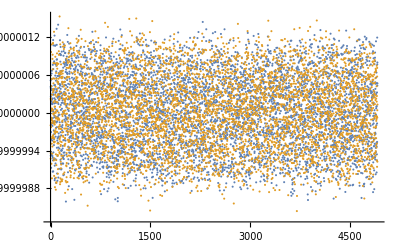

```mathematica
Table[PD1Ref[[n]].PD1Ref[[n]],{n,1,nNodes}];
Table[PD2Ref[[n]].PD2Ref[[n]],{n,1,nNodes}];
ListPlot[{%%,%},PlotRange->All]
```

从上图可见主方向已经单位化了，不满意可以再单位化一遍，接下来求解LMN

求解LMN with conformal mapping assumption

```mathematica
Solve[{Pk1+Pk2==(Lr+Nr)/Er,(*Pk1*Pk2==(-Mr^2+Lr Nr)/Er^2,*)α==-Mr/(Lr-Pk1 Er),β==-Mr/(Lr-Pk2 Er)},{Lr,Mr,Nr}];
FullSimplify[%]
```

{{Lr→(Er (Pk1 α-Pk2 β))/(α-β),Mr→(Er (-Pk1+Pk2) α β)/(α-β),Nr→(Er (Pk2 α-Pk1 β))/(α-β)}}

将解析解代入方程2，验证是否成立
Pk1*Pk2==(-Mr^2+Lr Nr)/Er^2，先计算右半边

```mathematica
(-Mr^2+Lr Nr)/Er^2/.{Lr->(Er (Pk1 α-Pk2 β))/(α-β),Mr->(Er (-Pk1+Pk2) α β)/(α-β),Nr->(Er (Pk2 α-Pk1 β))/(α-β)}//Simplify
Simplify[%,α β==-1]
```

(-Pk1^2 α β (1+α β)-Pk2^2 α β (1+α β)+Pk1 Pk2 (β^2+α^2 (1+2 β^2)))/(α-β)^2

Pk1 Pk2

求解LMN in general case

```mathematica
Solve[{Pk1+Pk2==(Lr Gr-2Mr Fr+Nr Er)/(Er Gr-Fr^2),(*Pk1*Pk2==(Lr Nr-Mr^2)/(Er Gr-Fr^2),*)α==-(Mr-Pk1 Fr)/(Lr-Pk1 Er),β==-(Mr-Pk2 Fr)/(Lr-Pk2 Er)},{Lr,Mr,Nr}]//FullSimplify
```

{{Lr→(Fr Pk1-Fr Pk2+Er Pk1 α-Er Pk2 β)/(α-β),Mr→(Er (-Pk1+Pk2) α β+Fr (Pk2 α-Pk1 β))/(α-β),Nr→(-Fr^2 (Pk1-Pk2) (α+β)+Er Gr (Pk2 α-Pk1 β)-Fr (Pk1-Pk2) (Gr+2 Er α β))/(Er (α-β))}}

```mathematica
αRef=Table[(PD1Ref[[n]].rXRef[[n]])/(PD1Ref[[n]].rYRef[[n]]) ,{n,1,nNodes}];
βRef=Table[(PD2Ref[[n]].rXRef[[n]])/(PD2Ref[[n]].rYRef[[n]]),{n,1,nNodes}];
```

检查Libigl计算的主方向

```mathematica
Table[{UV[[n,1]],UV[[n,2]],αRef[[n]]},{n,1,nNodes}];
ListPointPlot3D[{%}]
```

-Graphics3D-

```mathematica
Table[{UV[[n,1]],UV[[n,2]],βRef[[n]]},{n,1,nNodes}];
ListPointPlot3D[{%}]
```

-Graphics3D-

检查Libigl计算的主曲率

```mathematica
Table[{UV[[n,1]],UV[[n,2]],k1Ref[[n]]},{n,1,nNodes}];
Table[{UV[[n,1]],UV[[n,2]],k2Ref[[n]]},{n,1,nNodes}];
ListPointPlot3D[{%%,%},PlotRange->All]
```

-Graphics3D-

计算LMN

```mathematica
LLRef=Flatten[Table[1/(αRef[[n]]-βRef[[n]]) (FFRef[[n]] k1Ref[[n]]-FFRef[[n]] k2Ref[[n]]+EERef[[n]] k1Ref[[n]] αRef[[n]]-EERef[[n]] k2Ref[[n]] βRef[[n]]),{n,1,nNodes}]];
```

```mathematica
MMRef=Flatten[Table[1/(αRef[[n]]-βRef[[n]])(EERef[[n]] (-k1Ref[[n]]+k2Ref[[n]]) αRef[[n]] βRef[[n]]+FFRef[[n]] (k2Ref[[n]] αRef[[n]]-k1Ref[[n]] βRef[[n]])),{n,1,nNodes}]];
```

```mathematica
NNRef=Flatten[Table[1/(EERef[[n]] (αRef[[n]]-βRef[[n]]))(-(FFRef[[n]])^2 (k1Ref[[n]]-k2Ref[[n]]) (αRef[[n]]+βRef[[n]])+EERef[[n]] GGRef[[n]] (k2Ref[[n]] αRef[[n]]-k1Ref[[n]] βRef[[n]])-FFRef[[n]] (k1Ref[[n]]-k2Ref[[n]]) (GGRef[[n]]+2 EERef[[n]] αRef[[n]] βRef[[n]])),{n,1,nNodes}]];
```

```mathematica
DatumPlane=Graphics3D[{Gray,Opacity[0.6],Polygon[{{-1,-1,0},{-1,1,0},{1,1,0},{1,-1,0}}]}];
```

检查四条方程中，没有使用的第二条方程 （高斯曲率） 是否满足
Pk1*Pk2==(Lr Nr-Mr^2)/(Er Gr-Fr^2)

```mathematica
CheckEq2=Flatten[Table[k1Ref[[n]]*k2Ref[[n]]-(LLRef[[n]] NNRef[[n]]-MMRef[[n]]^2)/(EERef[[n]] GGRef[[n]]-FFRef[[n]]^2),{n,1,nNodes}]];
Table[{UV[[n,1]],UV[[n,2]],CheckEq2[[n]]},{n,1,nNodes}];
Show[ListPointPlot3D[%],DatumPlane]
```

-Graphics3D-

方程不太满足，公式无误，矫正主方向无改善，有可能是三角形网格离散化，还有libigl计算误差导致的

检查 LMN

```mathematica
Table[{UV[[n,1]],UV[[n,2]],LLRef[[n]]},{n,1,nNodes}];
Table[{UV[[n,1]],UV[[n,2]],MMRef[[n]]},{n,1,nNodes}];
Table[{UV[[n,1]],UV[[n,2]],NNRef[[n]]},{n,1,nNodes}];
ListPointPlot3D[{%%%,%%,%},PlotStyle->{Red,Green,Blue},PlotRange->All]
```

-Graphics3D-

mathematic preliminaries
-Graphics-
α.β=(MG-NF)/(LF-ME), α=(PD1.ru)/(PD1.rv), β=(PD2.ru)/(PD2.rv)

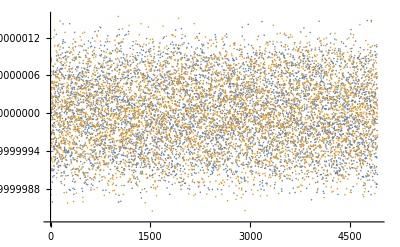

```mathematica
Table[PD1Tar[[n]].PD1Tar[[n]],{n,1,nNodes}];
Table[PD2Tar[[n]].PD2Tar[[n]],{n,1,nNodes}];
ListPlot[{%%,%},PlotRange->All]
```

从上图可见主方向已经单位化了，不满意可以再单位化一遍，接下来求解LMN

求解LMN with conformal mapping assumption

```mathematica
Solve[{Pk1+Pk2==(Lr+Nr)/Er,(*Pk1*Pk2==(-Mr^2+Lr Nr)/Er^2,*)α==-Mr/(Lr-Pk1 Er),β==-Mr/(Lr-Pk2 Er)},{Lr,Mr,Nr}];
FullSimplify[%]
```

{{Lr→(Er (Pk1 α-Pk2 β))/(α-β),Mr→(Er (-Pk1+Pk2) α β)/(α-β),Nr→(Er (Pk2 α-Pk1 β))/(α-β)}}

将解析解代入方程2，验证是否成立
Pk1*Pk2==(-Mr^2+Lr Nr)/Er^2，先计算右半边

```mathematica
(-Mr^2+Lr Nr)/Er^2/.{Lr->(Er (Pk1 α-Pk2 β))/(α-β),Mr->(Er (-Pk1+Pk2) α β)/(α-β),Nr->(Er (Pk2 α-Pk1 β))/(α-β)}//Simplify
Simplify[%,α β==-1]
```

(-Pk1^2 α β (1+α β)-Pk2^2 α β (1+α β)+Pk1 Pk2 (β^2+α^2 (1+2 β^2)))/(α-β)^2

Pk1 Pk2

求解LMN in general case

```mathematica
Solve[{Pk1+Pk2==(Lr Gr-2Mr Fr+Nr Er)/(Er Gr-Fr^2),(*Pk1*Pk2==(Lr Nr-Mr^2)/(Er Gr-Fr^2),*)α==-(Mr-Pk1 Fr)/(Lr-Pk1 Er),β==-(Mr-Pk2 Fr)/(Lr-Pk2 Er)},{Lr,Mr,Nr}]//FullSimplify
```

{{Lr→(Fr Pk1-Fr Pk2+Er Pk1 α-Er Pk2 β)/(α-β),Mr→(Er (-Pk1+Pk2) α β+Fr (Pk2 α-Pk1 β))/(α-β),Nr→(-Fr^2 (Pk1-Pk2) (α+β)+Er Gr (Pk2 α-Pk1 β)-Fr (Pk1-Pk2) (Gr+2 Er α β))/(Er (α-β))}}

```mathematica
αTar=Table[(PD1Tar[[n]].rXTar[[n]])/(PD1Tar[[n]].rYTar[[n]]) ,{n,1,nNodes}];
βTar=Table[(PD2Tar[[n]].rXTar[[n]])/(PD2Tar[[n]].rYTar[[n]]),{n,1,nNodes}];
```

检查Libigl计算的主方向

```mathematica
Table[{UV[[n,1]],UV[[n,2]],αTar[[n]]},{n,1,nNodes}];
ListPointPlot3D[{%}]
```

-Graphics3D-

```mathematica
Table[{UV[[n,1]],UV[[n,2]],βTar[[n]]},{n,1,nNodes}];
ListPointPlot3D[{%}]
```

-Graphics3D-

检查Libigl计算的主曲率

```mathematica
Table[{UV[[n,1]],UV[[n,2]],k1Tar[[n]]},{n,1,nNodes}];
Table[{UV[[n,1]],UV[[n,2]],k2Tar[[n]]},{n,1,nNodes}];
ListPointPlot3D[{%%,%},PlotRange->All]
```

-Graphics3D-

计算LMN

```mathematica
LLTar=Flatten[Table[1/(αTar[[n]]-βTar[[n]]) (FFTar[[n]] k1Tar[[n]]-FFTar[[n]] k2Tar[[n]]+EETar[[n]] k1Tar[[n]] αTar[[n]]-EETar[[n]] k2Tar[[n]] βTar[[n]]),{n,1,nNodes}]];
```

```mathematica
MMTar=Flatten[Table[1/(αTar[[n]]-βTar[[n]])(EETar[[n]] (-k1Tar[[n]]+k2Tar[[n]]) αTar[[n]] βTar[[n]]+FFTar[[n]] (k2Tar[[n]] αTar[[n]]-k1Tar[[n]] βTar[[n]])),{n,1,nNodes}]];
```

```mathematica
NNTar=Flatten[Table[1/(EETar[[n]] (αTar[[n]]-βTar[[n]]))(-(FFTar[[n]])^2 (k1Tar[[n]]-k2Tar[[n]]) (αTar[[n]]+βTar[[n]])+EETar[[n]] GGTar[[n]] (k2Tar[[n]] αTar[[n]]-k1Tar[[n]] βTar[[n]])-FFTar[[n]] (k1Tar[[n]]-k2Tar[[n]]) (GGTar[[n]]+2 EETar[[n]] αTar[[n]] βTar[[n]])),{n,1,nNodes}]];
```

```mathematica
DatumPlane=Graphics3D[{Gray,Opacity[0.6],Polygon[{{-1,-1,0},{-1,1,0},{1,1,0},{1,-1,0}}]}];
```

检查四条方程中，没有使用的第二条方程 （高斯曲率） 是否满足
Pk1*Pk2==(Lr Nr-Mr^2)/(Er Gr-Fr^2)

```mathematica
CheckEq2=Flatten[Table[k1Tar[[n]]*k2Tar[[n]]-(LLTar[[n]] NNTar[[n]]-MMTar[[n]]^2)/(EETar[[n]] GGTar[[n]]-FFTar[[n]]^2),{n,1,nNodes}]];
Table[{UV[[n,1]],UV[[n,2]],CheckEq2[[n]]},{n,1,nNodes}];
Show[ListPointPlot3D[%],DatumPlane]
```

-Graphics3D-

方程不太满足，公式无误，矫正主方向无改善，有可能是三角形网格离散化，还有libigl计算误差导致的

检查 LMN

```mathematica
Table[{UV[[n,1]],UV[[n,2]],LLTar[[n]]},{n,1,nNodes}];
Table[{UV[[n,1]],UV[[n,2]],MMTar[[n]]},{n,1,nNodes}];
Table[{UV[[n,1]],UV[[n,2]],NNTar[[n]]},{n,1,nNodes}];
ListPointPlot3D[{%%%,%%,%},PlotStyle->{Red,Green,Blue},PlotRange->All]
```

-Graphics3D-

三维模型的生成
先计算各节点的单位法向量n

```mathematica
InverseVectorFlag=-1;
```

```mathematica
VertornRef=InverseVectorFlag*Table[(rXRef[[n]]×rYRef[[n]])/(√((rXRef[[n]]×rYRef[[n]]).(rXRef[[n]]×rYRef[[n]]))),{n,1,nNodes}];
```

```mathematica
VertornTar=Table[(rXTar[[n]]×rYTar[[n]])/(√((rXTar[[n]]×rYTar[[n]]).(rXTar[[n]]×rYTar[[n]]))),{n,1,nNodes}];
```

```mathematica
HeadRad=0.01;
TubeRad=0.002;
nLen=0.05;
```

```mathematica
Table[{{VerticeRef[[n,1]],VerticeRef[[n,2]],VerticeRef[[n,3]]},{VerticeRef[[n,1]],VerticeRef[[n,2]],VerticeRef[[n,3]]}+nLen{VertornRef[[n,1]],VertornRef[[n,2]],VertornRef[[n,3]]}},{n,1,nNodes}];
nPlot=Graphics3D[{Red,Arrowheads[HeadRad],Arrow[Tube[%,TubeRad] ]}];
Show[nPlot,ModelRef]
```

-Graphics3D-

```mathematica
Table[{{VerticeTar[[n,1]],VerticeTar[[n,2]],VerticeTar[[n,3]]},{VerticeTar[[n,1]],VerticeTar[[n,2]],VerticeTar[[n,3]]}+nLen{VertornTar[[n,1]],VertornTar[[n,2]],VertornTar[[n,3]]}},{n,1,nNodes}];
nPlot=Graphics3D[{Red,Arrowheads[HeadRad],Arrow[Tube[%,TubeRad] ]}];
Show[nPlot,ModelTar]
```

-Graphics3D-

Verification passed

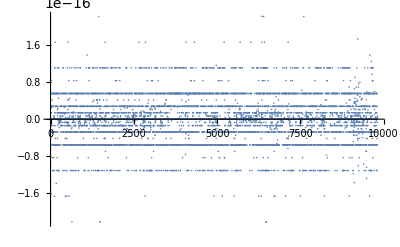

```mathematica
Flatten[Table[{VertornRef[[n]].rXRef[[n]],VertornRef[[n]].rYRef[[n]]},{n,1,nNodes}]];
ListPlot[%,PlotRange->All]
```

将节点沿法向平移，number of layers is 3

```mathematica
Th=0.01*1/3((Max[VerticeRef[[All,1]]]-Min[VerticeRef[[All,1]]])+(Max[VerticeRef[[All,2]]]-Min[VerticeRef[[All,2]]])+(Max[VerticeRef[[All,3]]]-Min[VerticeRef[[All,3]]]))
```

0.0132469

```mathematica
NodesL1=Table[VerticeRef[[n]]-Th/2 VertornRef[[n]],{n,1,nNodes}];
NodesL2=VerticeRef;
NodesL3=Table[VerticeRef[[n]]+Th/2 VertornRef[[n]],{n,1,nNodes}];
```

```mathematica
Table[{{NodesL1[[Face[[n,1]],1]],NodesL1[[Face[[n,1]],2]],NodesL1[[Face[[n,1]],3]]},{NodesL1[[Face[[n,2]],1]],NodesL1[[Face[[n,2]],2]],NodesL1[[Face[[n,2]],3]]},{NodesL1[[Face[[n,3]],1]],NodesL1[[Face[[n,3]],2]],NodesL1[[Face[[n,3]],3]]}},{n,1,nFaces}];
Layer1Plot=Graphics3D[Polygon[%]];
Table[{{NodesL2[[Face[[n,1]],1]],NodesL2[[Face[[n,1]],2]],NodesL2[[Face[[n,1]],3]]},{NodesL2[[Face[[n,2]],1]],NodesL2[[Face[[n,2]],2]],NodesL2[[Face[[n,2]],3]]},{NodesL2[[Face[[n,3]],1]],NodesL2[[Face[[n,3]],2]],NodesL2[[Face[[n,3]],3]]}},{n,1,nFaces}];
Layer2Plot=Graphics3D[Polygon[%]];
Table[{{NodesL3[[Face[[n,1]],1]],NodesL3[[Face[[n,1]],2]],NodesL3[[Face[[n,1]],3]]},{NodesL3[[Face[[n,2]],1]],NodesL3[[Face[[n,2]],2]],NodesL3[[Face[[n,2]],3]]},{NodesL3[[Face[[n,3]],1]],NodesL3[[Face[[n,3]],2]],NodesL3[[Face[[n,3]],3]]}},{n,1,nFaces}];
Layer3Plot=Graphics3D[Polygon[%]];
```

```mathematica
Show[Layer3Plot,Layer1Plot,PlotRange->All]
```

-Graphics3D-

曲面交叉了怎么办？让abaqus判断吧。

Output {a1,a2,a3} {b1,b2,b3} for CAE
g1 = {a1, a2, a3};
g2 = {b1, b2, b3};

```mathematica
a1MiddleRef=Table[1/3(rXRef[[Face[[n,1]],1]]+rXRef[[Face[[n,2]],1]]+rXRef[[Face[[n,3]],1]]),{n,1,nFaces}];
a2MiddleRef=Table[1/3(rXRef[[Face[[n,1]],2]]+rXRef[[Face[[n,2]],2]]+rXRef[[Face[[n,3]],2]]),{n,1,nFaces}];a3MiddleRef=Table[1/3(rXRef[[Face[[n,1]],3]]+rXRef[[Face[[n,2]],3]]+rXRef[[Face[[n,3]],3]]),{n,1,nFaces}];
```

```mathematica
b1MiddleRef=Table[1/3(rYRef[[Face[[n,1]],1]]+rYRef[[Face[[n,2]],1]]+rYRef[[Face[[n,3]],1]]),{n,1,nFaces}];
b2MiddleRef=Table[1/3(rYRef[[Face[[n,1]],2]]+rYRef[[Face[[n,2]],2]]+rYRef[[Face[[n,3]],2]]),{n,1,nFaces}];b3MiddleRef=Table[1/3(rYRef[[Face[[n,1]],3]]+rYRef[[Face[[n,2]],3]]+rYRef[[Face[[n,3]],3]]),{n,1,nFaces}];
```

```mathematica
Export["OutputForCAE/a1.csv",N[a1MiddleRef]];
Export["OutputForCAE/a2.csv",N[a2MiddleRef]];
Export["OutputForCAE/a3.csv",N[a3MiddleRef]];
Export["OutputForCAE/b1.csv",N[b1MiddleRef]];
Export["OutputForCAE/b2.csv",N[b2MiddleRef]];
Export["OutputForCAE/b3.csv",N[b3MiddleRef]];
```

Output nodes for CAE

```mathematica
NodesLayer1=Table[{n,NodesL1[[n,1]],NodesL1[[n,2]],NodesL1[[n,3]]},{n,1,nNodes}];
NodesLayer2=Table[{n+nNodes,NodesL2[[n,1]],NodesL2[[n,2]],NodesL2[[n,3]]},{n,1,nNodes}];
NodesLayer3=Table[{n+2nNodes,NodesL3[[n,1]],NodesL3[[n,2]],NodesL3[[n,3]]},{n,1,nNodes}];
```

```mathematica
OptNodes=Join[NodesLayer1,NodesLayer2,NodesLayer3];
```

```mathematica
Dimensions[OptNodes]
```

{14724,4}

Element is from bottom to top

```mathematica
(*EleLayer1=Table[{ii,Face[[ii,1]],Face[[ii,2]],Face[[ii,3]],Face[[ii,1]]+nNodes,Face[[ii,2]]+nNodes,Face[[ii,3]]+nNodes},{ii,1,nFaces}];

EleLayer2=Table[{ii+nFaces,Face[[ii,1]]+nNodes,Face[[ii,2]]+nNodes,Face[[ii,3]]+nNodes,Face[[ii,1]]+2nNodes,Face[[ii,2]]+2nNodes,Face[[ii,3]]+2nNodes},{ii,1,nFaces}];*)
```

```mathematica
EleLayer1=Table[{ii,Face[[ii,1]],Face[[ii,3]],Face[[ii,2]],Face[[ii,1]]+nNodes,Face[[ii,3]]+nNodes,Face[[ii,2]]+nNodes},{ii,1,nFaces}];

EleLayer2=Table[{ii+nFaces,Face[[ii,1]]+nNodes,Face[[ii,3]]+nNodes,Face[[ii,2]]+nNodes,Face[[ii,1]]+2nNodes,Face[[ii,3]]+2nNodes,Face[[ii,2]]+2nNodes},{ii,1,nFaces}];
```

先做两层

```mathematica
OptEleNumber=Join[EleLayer1,EleLayer2];
```

Boundary Conditions

```mathematica
TopMid=0;
```

```mathematica
BotMid=0;
```

```mathematica
BotRight=0;
```

```mathematica
nFaces*2
```

19212

```mathematica
Export["OutputForCAE/Mma128140Element.csv",Join[{{"nodes  ",3nNodes}},OptNodes,{{ }},{{"elements  ",2nFaces}},OptEleNumber,{{ }},{{"*Nset, nset=BotNode, generate"},{1,nNodes,1}},{{"*Nset, nset=TopNode, generate"},{1+2nNodes,3nNodes,1}},{{"*Nset, nset=BotMid"},{BotMid}},{{"*Nset, nset=BotRight"},{BotRight}},{{"*Nset, nset=TopMid"},{TopMid}}]];
```

Calculate growth function

{DetGTmp1, λ10Tmp1, λ20Tmp1, λs0Tmp1}

```mathematica
GrowthFunTmp1=Table[{((-EETar[[n]]^2 EERef[[n]] FFRef[[n]]^2 GGTar[[n]]+2 EETar[[n]] FFTar[[n]] FFRef[[n]]^2 (EERef[[n]] FFTar[[n]]+FFRef[[n]] GGTar[[n]])-EETar[[n]] (EERef[[n]]^2 FFTar[[n]]^2+4 EERef[[n]] FFTar[[n]] FFRef[[n]] GGTar[[n]]+FFRef[[n]]^2 GGTar[[n]]^2) GGRef[[n]]+FFTar[[n]]^2 GGRef[[n]] (2 FFRef[[n]] (EERef[[n]] FFTar[[n]]+FFRef[[n]] GGTar[[n]])-EERef[[n]] GGTar[[n]] GGRef[[n]])+2 √((FFTar[[n]]^2-EETar[[n]] GGTar[[n]]) (FFRef[[n]]^2-EERef[[n]] GGRef[[n]])) Abs[EERef[[n]] FFTar[[n]]+FFRef[[n]] GGTar[[n]]] Abs[EETar[[n]] FFRef[[n]]+FFTar[[n]] GGRef[[n]]]) (-1+(((EETar[[n]] FFRef[[n]]+FFTar[[n]] GGRef[[n]]) (-FFTar[[n]] FFRef[[n]]^2 GGTar[[n]]+EERef[[n]] (-FFTar[[n]]^2 FFRef[[n]]+EETar[[n]] FFRef[[n]] GGTar[[n]]+FFTar[[n]] GGTar[[n]] GGRef[[n]]))+√((FFTar[[n]]^2-EETar[[n]] GGTar[[n]]) (FFRef[[n]]^2-EERef[[n]] GGRef[[n]])) Abs[EERef[[n]] FFTar[[n]]+FFRef[[n]] GGTar[[n]]] Abs[EETar[[n]] FFRef[[n]]+FFTar[[n]] GGRef[[n]]]) ((EERef[[n]] FFTar[[n]]+FFRef[[n]] GGTar[[n]]) (-FFTar[[n]]^2 FFRef[[n]] GGRef[[n]]+EETar[[n]] (-FFTar[[n]] FFRef[[n]]^2+EERef[[n]] FFTar[[n]] GGRef[[n]]+FFRef[[n]] GGTar[[n]] GGRef[[n]]))+√((FFTar[[n]]^2-EETar[[n]] GGTar[[n]]) (FFRef[[n]]^2-EERef[[n]] GGRef[[n]])) Abs[EERef[[n]] FFTar[[n]]+FFRef[[n]] GGTar[[n]]] Abs[EETar[[n]] FFRef[[n]]+FFTar[[n]] GGRef[[n]]]))/((EERef[[n]] FFTar[[n]]+FFRef[[n]] GGTar[[n]]) (EETar[[n]] FFRef[[n]]+FFTar[[n]] GGRef[[n]]) (EETar[[n]] FFRef[[n]]^2 GGTar[[n]]-EERef[[n]] FFTar[[n]]^2 GGRef[[n]])^2)))/((FFRef[[n]]^2-EERef[[n]] GGRef[[n]]) (EETar[[n]]^2 EERef[[n]]^2+4 EETar[[n]] FFRef[[n]] (EERef[[n]] FFTar[[n]]+FFRef[[n]] GGTar[[n]])-2 EETar[[n]] EERef[[n]] GGTar[[n]] GGRef[[n]]+GGRef[[n]] (4 FFTar[[n]] (EERef[[n]] FFTar[[n]]+FFRef[[n]] GGTar[[n]])+GGTar[[n]]^2 GGRef[[n]]))),((-((EERef[[n]] FFTar[[n]]+FFRef[[n]] GGTar[[n]]) (-FFTar[[n]]^2 FFRef[[n]] GGRef[[n]]+EETar[[n]] (-FFTar[[n]] FFRef[[n]]^2+EERef[[n]] FFTar[[n]] GGRef[[n]]+FFRef[[n]] GGTar[[n]] GGRef[[n]])))-√((FFTar[[n]]^2-EETar[[n]] GGTar[[n]]) (FFRef[[n]]^2-EERef[[n]] GGRef[[n]])) Abs[EERef[[n]] FFTar[[n]]+FFRef[[n]] GGTar[[n]]] Abs[EETar[[n]] FFRef[[n]]+FFTar[[n]] GGRef[[n]]]) √((-EETar[[n]]^2 EERef[[n]] FFRef[[n]]^2 GGTar[[n]]+2 EETar[[n]] FFTar[[n]] FFRef[[n]]^2 (EERef[[n]] FFTar[[n]]+FFRef[[n]] GGTar[[n]])-EETar[[n]] (EERef[[n]]^2 FFTar[[n]]^2+4 EERef[[n]] FFTar[[n]] FFRef[[n]] GGTar[[n]]+FFRef[[n]]^2 GGTar[[n]]^2) GGRef[[n]]+FFTar[[n]]^2 GGRef[[n]] (2 FFRef[[n]] (EERef[[n]] FFTar[[n]]+FFRef[[n]] GGTar[[n]])-EERef[[n]] GGTar[[n]] GGRef[[n]])+2 √((FFTar[[n]]^2-EETar[[n]] GGTar[[n]]) (FFRef[[n]]^2-EERef[[n]] GGRef[[n]])) Abs[EERef[[n]] FFTar[[n]]+FFRef[[n]] GGTar[[n]]] Abs[EETar[[n]] FFRef[[n]]+FFTar[[n]] GGRef[[n]]])/((FFRef[[n]]^2-EERef[[n]] GGRef[[n]]) (EETar[[n]]^2 EERef[[n]]^2+4 EETar[[n]] FFRef[[n]] (EERef[[n]] FFTar[[n]]+FFRef[[n]] GGTar[[n]])-2 EETar[[n]] EERef[[n]] GGTar[[n]] GGRef[[n]]+GGRef[[n]] (4 FFTar[[n]] (EERef[[n]] FFTar[[n]]+FFRef[[n]] GGTar[[n]])+GGTar[[n]]^2 GGRef[[n]])))))/((EERef[[n]] FFTar[[n]]+FFRef[[n]] GGTar[[n]]) (-EETar[[n]] FFRef[[n]]^2 GGTar[[n]]+EERef[[n]] FFTar[[n]]^2 GGRef[[n]])),(((EETar[[n]] FFRef[[n]]+FFTar[[n]] GGRef[[n]]) (-FFRef[[n]] (FFTar[[n]] FFRef[[n]] GGTar[[n]]+EERef[[n]] (FFTar[[n]]^2-EETar[[n]] GGTar[[n]]))+EERef[[n]] FFTar[[n]] GGTar[[n]] GGRef[[n]])+√((FFTar[[n]]^2-EETar[[n]] GGTar[[n]]) (FFRef[[n]]^2-EERef[[n]] GGRef[[n]])) Abs[EERef[[n]] FFTar[[n]]+FFRef[[n]] GGTar[[n]]] Abs[EETar[[n]] FFRef[[n]]+FFTar[[n]] GGRef[[n]]]) √((-EETar[[n]]^2 EERef[[n]] FFRef[[n]]^2 GGTar[[n]]+2 EETar[[n]] FFTar[[n]] FFRef[[n]]^2 (EERef[[n]] FFTar[[n]]+FFRef[[n]] GGTar[[n]])-EETar[[n]] (EERef[[n]]^2 FFTar[[n]]^2+4 EERef[[n]] FFTar[[n]] FFRef[[n]] GGTar[[n]]+FFRef[[n]]^2 GGTar[[n]]^2) GGRef[[n]]+FFTar[[n]]^2 GGRef[[n]] (2 FFRef[[n]] (EERef[[n]] FFTar[[n]]+FFRef[[n]] GGTar[[n]])-EERef[[n]] GGTar[[n]] GGRef[[n]])+2 √((FFTar[[n]]^2-EETar[[n]] GGTar[[n]]) (FFRef[[n]]^2-EERef[[n]] GGRef[[n]])) Abs[EERef[[n]] FFTar[[n]]+FFRef[[n]] GGTar[[n]]] Abs[EETar[[n]] FFRef[[n]]+FFTar[[n]] GGRef[[n]]])/((FFRef[[n]]^2-EERef[[n]] GGRef[[n]]) (EETar[[n]]^2 EERef[[n]]^2+4 EETar[[n]] FFRef[[n]] (EERef[[n]] FFTar[[n]]+FFRef[[n]] GGTar[[n]])-2 EETar[[n]] EERef[[n]] GGTar[[n]] GGRef[[n]]+GGRef[[n]] (4 FFTar[[n]] (EERef[[n]] FFTar[[n]]+FFRef[[n]] GGTar[[n]])+GGTar[[n]]^2 GGRef[[n]])))))/((EETar[[n]] FFRef[[n]]+FFTar[[n]] GGRef[[n]]) (EETar[[n]] FFRef[[n]]^2 GGTar[[n]]-EERef[[n]] FFTar[[n]]^2 GGRef[[n]])),-√((-EETar[[n]]^2 EERef[[n]] FFRef[[n]]^2 GGTar[[n]]+2 EETar[[n]] FFTar[[n]] FFRef[[n]]^2 (EERef[[n]] FFTar[[n]]+FFRef[[n]] GGTar[[n]])-EETar[[n]] (EERef[[n]]^2 FFTar[[n]]^2+4 EERef[[n]] FFTar[[n]] FFRef[[n]] GGTar[[n]]+FFRef[[n]]^2 GGTar[[n]]^2) GGRef[[n]]+FFTar[[n]]^2 GGRef[[n]] (2 FFRef[[n]] (EERef[[n]] FFTar[[n]]+FFRef[[n]] GGTar[[n]])-EERef[[n]] GGTar[[n]] GGRef[[n]])+2 √((FFTar[[n]]^2-EETar[[n]] GGTar[[n]]) (FFRef[[n]]^2-EERef[[n]] GGRef[[n]])) Abs[EERef[[n]] FFTar[[n]]+FFRef[[n]] GGTar[[n]]] Abs[EETar[[n]] FFRef[[n]]+FFTar[[n]] GGRef[[n]]])/((FFRef[[n]]^2-EERef[[n]] GGRef[[n]]) (EETar[[n]]^2 EERef[[n]]^2+4 EETar[[n]] FFRef[[n]] (EERef[[n]] FFTar[[n]]+FFRef[[n]] GGTar[[n]])-2 EETar[[n]] EERef[[n]] GGTar[[n]] GGRef[[n]]+GGRef[[n]] (4 FFTar[[n]] (EERef[[n]] FFTar[[n]]+FFRef[[n]] GGTar[[n]])+GGTar[[n]]^2 GGRef[[n]]))))},{n,1,nNodes}];
```

{DetGTmp2, λ10Tmp2, λ20Tmp2, λs0Tmp2}

```mathematica
GrowthFunTmp2=Table[{((-EETar[[n]]^2 EERef[[n]] FFRef[[n]]^2 GGTar[[n]]+2 EETar[[n]] FFTar[[n]] FFRef[[n]]^2 (EERef[[n]] FFTar[[n]]+FFRef[[n]] GGTar[[n]])-EETar[[n]] (EERef[[n]]^2 FFTar[[n]]^2+4 EERef[[n]] FFTar[[n]] FFRef[[n]] GGTar[[n]]+FFRef[[n]]^2 GGTar[[n]]^2) GGRef[[n]]+FFTar[[n]]^2 GGRef[[n]] (2 FFRef[[n]] (EERef[[n]] FFTar[[n]]+FFRef[[n]] GGTar[[n]])-EERef[[n]] GGTar[[n]] GGRef[[n]])+2 √((FFTar[[n]]^2-EETar[[n]] GGTar[[n]]) (FFRef[[n]]^2-EERef[[n]] GGRef[[n]])) Abs[EERef[[n]] FFTar[[n]]+FFRef[[n]] GGTar[[n]]] Abs[EETar[[n]] FFRef[[n]]+FFTar[[n]] GGRef[[n]]]) (-1+(((EETar[[n]] FFRef[[n]]+FFTar[[n]] GGRef[[n]]) (-FFTar[[n]] FFRef[[n]]^2 GGTar[[n]]+EERef[[n]] (-FFTar[[n]]^2 FFRef[[n]]+EETar[[n]] FFRef[[n]] GGTar[[n]]+FFTar[[n]] GGTar[[n]] GGRef[[n]]))+√((FFTar[[n]]^2-EETar[[n]] GGTar[[n]]) (FFRef[[n]]^2-EERef[[n]] GGRef[[n]])) Abs[EERef[[n]] FFTar[[n]]+FFRef[[n]] GGTar[[n]]] Abs[EETar[[n]] FFRef[[n]]+FFTar[[n]] GGRef[[n]]]) ((EERef[[n]] FFTar[[n]]+FFRef[[n]] GGTar[[n]]) (-FFTar[[n]]^2 FFRef[[n]] GGRef[[n]]+EETar[[n]] (-FFTar[[n]] FFRef[[n]]^2+EERef[[n]] FFTar[[n]] GGRef[[n]]+FFRef[[n]] GGTar[[n]] GGRef[[n]]))+√((FFTar[[n]]^2-EETar[[n]] GGTar[[n]]) (FFRef[[n]]^2-EERef[[n]] GGRef[[n]])) Abs[EERef[[n]] FFTar[[n]]+FFRef[[n]] GGTar[[n]]] Abs[EETar[[n]] FFRef[[n]]+FFTar[[n]] GGRef[[n]]]))/((EERef[[n]] FFTar[[n]]+FFRef[[n]] GGTar[[n]]) (EETar[[n]] FFRef[[n]]+FFTar[[n]] GGRef[[n]]) (EETar[[n]] FFRef[[n]]^2 GGTar[[n]]-EERef[[n]] FFTar[[n]]^2 GGRef[[n]])^2)))/((FFRef[[n]]^2-EERef[[n]] GGRef[[n]]) (EETar[[n]]^2 EERef[[n]]^2+4 EETar[[n]] FFRef[[n]] (EERef[[n]] FFTar[[n]]+FFRef[[n]] GGTar[[n]])-2 EETar[[n]] EERef[[n]] GGTar[[n]] GGRef[[n]]+GGRef[[n]] (4 FFTar[[n]] (EERef[[n]] FFTar[[n]]+FFRef[[n]] GGTar[[n]])+GGTar[[n]]^2 GGRef[[n]]))),(((EERef[[n]] FFTar[[n]]+FFRef[[n]] GGTar[[n]]) (-FFTar[[n]]^2 FFRef[[n]] GGRef[[n]]+EETar[[n]] (-FFTar[[n]] FFRef[[n]]^2+EERef[[n]] FFTar[[n]] GGRef[[n]]+FFRef[[n]] GGTar[[n]] GGRef[[n]]))+√((FFTar[[n]]^2-EETar[[n]] GGTar[[n]]) (FFRef[[n]]^2-EERef[[n]] GGRef[[n]])) Abs[EERef[[n]] FFTar[[n]]+FFRef[[n]] GGTar[[n]]] Abs[EETar[[n]] FFRef[[n]]+FFTar[[n]] GGRef[[n]]]) √((-EETar[[n]]^2 EERef[[n]] FFRef[[n]]^2 GGTar[[n]]+2 EETar[[n]] FFTar[[n]] FFRef[[n]]^2 (EERef[[n]] FFTar[[n]]+FFRef[[n]] GGTar[[n]])-EETar[[n]] (EERef[[n]]^2 FFTar[[n]]^2+4 EERef[[n]] FFTar[[n]] FFRef[[n]] GGTar[[n]]+FFRef[[n]]^2 GGTar[[n]]^2) GGRef[[n]]+FFTar[[n]]^2 GGRef[[n]] (2 FFRef[[n]] (EERef[[n]] FFTar[[n]]+FFRef[[n]] GGTar[[n]])-EERef[[n]] GGTar[[n]] GGRef[[n]])+2 √((FFTar[[n]]^2-EETar[[n]] GGTar[[n]]) (FFRef[[n]]^2-EERef[[n]] GGRef[[n]])) Abs[EERef[[n]] FFTar[[n]]+FFRef[[n]] GGTar[[n]]] Abs[EETar[[n]] FFRef[[n]]+FFTar[[n]] GGRef[[n]]])/((FFRef[[n]]^2-EERef[[n]] GGRef[[n]]) (EETar[[n]]^2 EERef[[n]]^2+4 EETar[[n]] FFRef[[n]] (EERef[[n]] FFTar[[n]]+FFRef[[n]] GGTar[[n]])-2 EETar[[n]] EERef[[n]] GGTar[[n]] GGRef[[n]]+GGRef[[n]] (4 FFTar[[n]] (EERef[[n]] FFTar[[n]]+FFRef[[n]] GGTar[[n]])+GGTar[[n]]^2 GGRef[[n]])))))/((EERef[[n]] FFTar[[n]]+FFRef[[n]] GGTar[[n]]) (-EETar[[n]] FFRef[[n]]^2 GGTar[[n]]+EERef[[n]] FFTar[[n]]^2 GGRef[[n]])),((-((EETar[[n]] FFRef[[n]]+FFTar[[n]] GGRef[[n]]) (-FFRef[[n]] (FFTar[[n]] FFRef[[n]] GGTar[[n]]+EERef[[n]] (FFTar[[n]]^2-EETar[[n]] GGTar[[n]]))+EERef[[n]] FFTar[[n]] GGTar[[n]] GGRef[[n]]))-√((FFTar[[n]]^2-EETar[[n]] GGTar[[n]]) (FFRef[[n]]^2-EERef[[n]] GGRef[[n]])) Abs[EERef[[n]] FFTar[[n]]+FFRef[[n]] GGTar[[n]]] Abs[EETar[[n]] FFRef[[n]]+FFTar[[n]] GGRef[[n]]]) √((-EETar[[n]]^2 EERef[[n]] FFRef[[n]]^2 GGTar[[n]]+2 EETar[[n]] FFTar[[n]] FFRef[[n]]^2 (EERef[[n]] FFTar[[n]]+FFRef[[n]] GGTar[[n]])-EETar[[n]] (EERef[[n]]^2 FFTar[[n]]^2+4 EERef[[n]] FFTar[[n]] FFRef[[n]] GGTar[[n]]+FFRef[[n]]^2 GGTar[[n]]^2) GGRef[[n]]+FFTar[[n]]^2 GGRef[[n]] (2 FFRef[[n]] (EERef[[n]] FFTar[[n]]+FFRef[[n]] GGTar[[n]])-EERef[[n]] GGTar[[n]] GGRef[[n]])+2 √((FFTar[[n]]^2-EETar[[n]] GGTar[[n]]) (FFRef[[n]]^2-EERef[[n]] GGRef[[n]])) Abs[EERef[[n]] FFTar[[n]]+FFRef[[n]] GGTar[[n]]] Abs[EETar[[n]] FFRef[[n]]+FFTar[[n]] GGRef[[n]]])/((FFRef[[n]]^2-EERef[[n]] GGRef[[n]]) (EETar[[n]]^2 EERef[[n]]^2+4 EETar[[n]] FFRef[[n]] (EERef[[n]] FFTar[[n]]+FFRef[[n]] GGTar[[n]])-2 EETar[[n]] EERef[[n]] GGTar[[n]] GGRef[[n]]+GGRef[[n]] (4 FFTar[[n]] (EERef[[n]] FFTar[[n]]+FFRef[[n]] GGTar[[n]])+GGTar[[n]]^2 GGRef[[n]])))))/((EETar[[n]] FFRef[[n]]+FFTar[[n]] GGRef[[n]]) (EETar[[n]] FFRef[[n]]^2 GGTar[[n]]-EERef[[n]] FFTar[[n]]^2 GGRef[[n]])),√((-EETar[[n]]^2 EERef[[n]] FFRef[[n]]^2 GGTar[[n]]+2 EETar[[n]] FFTar[[n]] FFRef[[n]]^2 (EERef[[n]] FFTar[[n]]+FFRef[[n]] GGTar[[n]])-EETar[[n]] (EERef[[n]]^2 FFTar[[n]]^2+4 EERef[[n]] FFTar[[n]] FFRef[[n]] GGTar[[n]]+FFRef[[n]]^2 GGTar[[n]]^2) GGRef[[n]]+FFTar[[n]]^2 GGRef[[n]] (2 FFRef[[n]] (EERef[[n]] FFTar[[n]]+FFRef[[n]] GGTar[[n]])-EERef[[n]] GGTar[[n]] GGRef[[n]])+2 √((FFTar[[n]]^2-EETar[[n]] GGTar[[n]]) (FFRef[[n]]^2-EERef[[n]] GGRef[[n]])) Abs[EERef[[n]] FFTar[[n]]+FFRef[[n]] GGTar[[n]]] Abs[EETar[[n]] FFRef[[n]]+FFTar[[n]] GGRef[[n]]])/((FFRef[[n]]^2-EERef[[n]] GGRef[[n]]) (EETar[[n]]^2 EERef[[n]]^2+4 EETar[[n]] FFRef[[n]] (EERef[[n]] FFTar[[n]]+FFRef[[n]] GGTar[[n]])-2 EETar[[n]] EERef[[n]] GGTar[[n]] GGRef[[n]]+GGRef[[n]] (4 FFTar[[n]] (EERef[[n]] FFTar[[n]]+FFRef[[n]] GGTar[[n]])+GGTar[[n]]^2 GGRef[[n]]))))},{n,1,nNodes}];
```

{DetGTmp3, λ10Tmp3, λ20Tmp3, λs0Tmp3}

```mathematica
GrowthFunTmp3=Table[{((-EETar[[n]]^2 EERef[[n]] FFRef[[n]]^2 GGTar[[n]]+2 EETar[[n]] FFTar[[n]] FFRef[[n]]^2 (EERef[[n]] FFTar[[n]]+FFRef[[n]] GGTar[[n]])-EETar[[n]] (EERef[[n]]^2 FFTar[[n]]^2+4 EERef[[n]] FFTar[[n]] FFRef[[n]] GGTar[[n]]+FFRef[[n]]^2 GGTar[[n]]^2) GGRef[[n]]+FFTar[[n]]^2 GGRef[[n]] (2 FFRef[[n]] (EERef[[n]] FFTar[[n]]+FFRef[[n]] GGTar[[n]])-EERef[[n]] GGTar[[n]] GGRef[[n]])-2 √((FFTar[[n]]^2-EETar[[n]] GGTar[[n]]) (FFRef[[n]]^2-EERef[[n]] GGRef[[n]])) Abs[EERef[[n]] FFTar[[n]]+FFRef[[n]] GGTar[[n]]] Abs[EETar[[n]] FFRef[[n]]+FFTar[[n]] GGRef[[n]]]) (-1-(((EERef[[n]] FFTar[[n]]+FFRef[[n]] GGTar[[n]]) (-FFTar[[n]]^2 FFRef[[n]] GGRef[[n]]+EETar[[n]] (-FFTar[[n]] FFRef[[n]]^2+EERef[[n]] FFTar[[n]] GGRef[[n]]+FFRef[[n]] GGTar[[n]] GGRef[[n]]))-√((FFTar[[n]]^2-EETar[[n]] GGTar[[n]]) (FFRef[[n]]^2-EERef[[n]] GGRef[[n]])) Abs[EERef[[n]] FFTar[[n]]+FFRef[[n]] GGTar[[n]]] Abs[EETar[[n]] FFRef[[n]]+FFTar[[n]] GGRef[[n]]]) (-((EETar[[n]] FFRef[[n]]+FFTar[[n]] GGRef[[n]]) (-FFTar[[n]] FFRef[[n]]^2 GGTar[[n]]+EERef[[n]] (-FFTar[[n]]^2 FFRef[[n]]+EETar[[n]] FFRef[[n]] GGTar[[n]]+FFTar[[n]] GGTar[[n]] GGRef[[n]])))+√((FFTar[[n]]^2-EETar[[n]] GGTar[[n]]) (FFRef[[n]]^2-EERef[[n]] GGRef[[n]])) Abs[EERef[[n]] FFTar[[n]]+FFRef[[n]] GGTar[[n]]] Abs[EETar[[n]] FFRef[[n]]+FFTar[[n]] GGRef[[n]]]))/((EERef[[n]] FFTar[[n]]+FFRef[[n]] GGTar[[n]]) (EETar[[n]] FFRef[[n]]+FFTar[[n]] GGRef[[n]]) (EETar[[n]] FFRef[[n]]^2 GGTar[[n]]-EERef[[n]] FFTar[[n]]^2 GGRef[[n]])^2)))/((FFRef[[n]]^2-EERef[[n]] GGRef[[n]]) (EETar[[n]]^2 EERef[[n]]^2+4 EETar[[n]] FFRef[[n]] (EERef[[n]] FFTar[[n]]+FFRef[[n]] GGTar[[n]])-2 EETar[[n]] EERef[[n]] GGTar[[n]] GGRef[[n]]+GGRef[[n]] (4 FFTar[[n]] (EERef[[n]] FFTar[[n]]+FFRef[[n]] GGTar[[n]])+GGTar[[n]]^2 GGRef[[n]]))),(√((-EETar[[n]]^2 EERef[[n]] FFRef[[n]]^2 GGTar[[n]]+2 EETar[[n]] FFTar[[n]] FFRef[[n]]^2 (EERef[[n]] FFTar[[n]]+FFRef[[n]] GGTar[[n]])-EETar[[n]] (EERef[[n]]^2 FFTar[[n]]^2+4 EERef[[n]] FFTar[[n]] FFRef[[n]] GGTar[[n]]+FFRef[[n]]^2 GGTar[[n]]^2) GGRef[[n]]+FFTar[[n]]^2 GGRef[[n]] (2 FFRef[[n]] (EERef[[n]] FFTar[[n]]+FFRef[[n]] GGTar[[n]])-EERef[[n]] GGTar[[n]] GGRef[[n]])-2 √((FFTar[[n]]^2-EETar[[n]] GGTar[[n]]) (FFRef[[n]]^2-EERef[[n]] GGRef[[n]])) Abs[EERef[[n]] FFTar[[n]]+FFRef[[n]] GGTar[[n]]] Abs[EETar[[n]] FFRef[[n]]+FFTar[[n]] GGRef[[n]]])/((FFRef[[n]]^2-EERef[[n]] GGRef[[n]]) (EETar[[n]]^2 EERef[[n]]^2+4 EETar[[n]] FFRef[[n]] (EERef[[n]] FFTar[[n]]+FFRef[[n]] GGTar[[n]])-2 EETar[[n]] EERef[[n]] GGTar[[n]] GGRef[[n]]+GGRef[[n]] (4 FFTar[[n]] (EERef[[n]] FFTar[[n]]+FFRef[[n]] GGTar[[n]])+GGTar[[n]]^2 GGRef[[n]])))) (-((EERef[[n]] FFTar[[n]]+FFRef[[n]] GGTar[[n]]) (-FFTar[[n]]^2 FFRef[[n]] GGRef[[n]]+EETar[[n]] (-FFTar[[n]] FFRef[[n]]^2+EERef[[n]] FFTar[[n]] GGRef[[n]]+FFRef[[n]] GGTar[[n]] GGRef[[n]])))+√((FFTar[[n]]^2-EETar[[n]] GGTar[[n]]) (FFRef[[n]]^2-EERef[[n]] GGRef[[n]])) Abs[EERef[[n]] FFTar[[n]]+FFRef[[n]] GGTar[[n]]] Abs[EETar[[n]] FFRef[[n]]+FFTar[[n]] GGRef[[n]]]))/((EERef[[n]] FFTar[[n]]+FFRef[[n]] GGTar[[n]]) (-EETar[[n]] FFRef[[n]]^2 GGTar[[n]]+EERef[[n]] FFTar[[n]]^2 GGRef[[n]])),(√((-EETar[[n]]^2 EERef[[n]] FFRef[[n]]^2 GGTar[[n]]+2 EETar[[n]] FFTar[[n]] FFRef[[n]]^2 (EERef[[n]] FFTar[[n]]+FFRef[[n]] GGTar[[n]])-EETar[[n]] (EERef[[n]]^2 FFTar[[n]]^2+4 EERef[[n]] FFTar[[n]] FFRef[[n]] GGTar[[n]]+FFRef[[n]]^2 GGTar[[n]]^2) GGRef[[n]]+FFTar[[n]]^2 GGRef[[n]] (2 FFRef[[n]] (EERef[[n]] FFTar[[n]]+FFRef[[n]] GGTar[[n]])-EERef[[n]] GGTar[[n]] GGRef[[n]])-2 √((FFTar[[n]]^2-EETar[[n]] GGTar[[n]]) (FFRef[[n]]^2-EERef[[n]] GGRef[[n]])) Abs[EERef[[n]] FFTar[[n]]+FFRef[[n]] GGTar[[n]]] Abs[EETar[[n]] FFRef[[n]]+FFTar[[n]] GGRef[[n]]])/((FFRef[[n]]^2-EERef[[n]] GGRef[[n]]) (EETar[[n]]^2 EERef[[n]]^2+4 EETar[[n]] FFRef[[n]] (EERef[[n]] FFTar[[n]]+FFRef[[n]] GGTar[[n]])-2 EETar[[n]] EERef[[n]] GGTar[[n]] GGRef[[n]]+GGRef[[n]] (4 FFTar[[n]] (EERef[[n]] FFTar[[n]]+FFRef[[n]] GGTar[[n]])+GGTar[[n]]^2 GGRef[[n]])))) ((EETar[[n]] FFRef[[n]]+FFTar[[n]] GGRef[[n]]) (-FFRef[[n]] (FFTar[[n]] FFRef[[n]] GGTar[[n]]+EERef[[n]] (FFTar[[n]]^2-EETar[[n]] GGTar[[n]]))+EERef[[n]] FFTar[[n]] GGTar[[n]] GGRef[[n]])-√((FFTar[[n]]^2-EETar[[n]] GGTar[[n]]) (FFRef[[n]]^2-EERef[[n]] GGRef[[n]])) Abs[EERef[[n]] FFTar[[n]]+FFRef[[n]] GGTar[[n]]] Abs[EETar[[n]] FFRef[[n]]+FFTar[[n]] GGRef[[n]]]))/((EETar[[n]] FFRef[[n]]+FFTar[[n]] GGRef[[n]]) (EETar[[n]] FFRef[[n]]^2 GGTar[[n]]-EERef[[n]] FFTar[[n]]^2 GGRef[[n]])),-√((-EETar[[n]]^2 EERef[[n]] FFRef[[n]]^2 GGTar[[n]]+2 EETar[[n]] FFTar[[n]] FFRef[[n]]^2 (EERef[[n]] FFTar[[n]]+FFRef[[n]] GGTar[[n]])-EETar[[n]] (EERef[[n]]^2 FFTar[[n]]^2+4 EERef[[n]] FFTar[[n]] FFRef[[n]] GGTar[[n]]+FFRef[[n]]^2 GGTar[[n]]^2) GGRef[[n]]+FFTar[[n]]^2 GGRef[[n]] (2 FFRef[[n]] (EERef[[n]] FFTar[[n]]+FFRef[[n]] GGTar[[n]])-EERef[[n]] GGTar[[n]] GGRef[[n]])-2 √((FFTar[[n]]^2-EETar[[n]] GGTar[[n]]) (FFRef[[n]]^2-EERef[[n]] GGRef[[n]])) Abs[EERef[[n]] FFTar[[n]]+FFRef[[n]] GGTar[[n]]] Abs[EETar[[n]] FFRef[[n]]+FFTar[[n]] GGRef[[n]]])/((FFRef[[n]]^2-EERef[[n]] GGRef[[n]]) (EETar[[n]]^2 EERef[[n]]^2+4 EETar[[n]] FFRef[[n]] (EERef[[n]] FFTar[[n]]+FFRef[[n]] GGTar[[n]])-2 EETar[[n]] EERef[[n]] GGTar[[n]] GGRef[[n]]+GGRef[[n]] (4 FFTar[[n]] (EERef[[n]] FFTar[[n]]+FFRef[[n]] GGTar[[n]])+GGTar[[n]]^2 GGRef[[n]]))))},{n,1,nNodes}];
```

{DetGTmp4, λ10Tmp4, λ20Tmp4, λs0Tmp4}

```mathematica
GrowthFunTmp4=Table[{((-EETar[[n]]^2 EERef[[n]] FFRef[[n]]^2 GGTar[[n]]+2 EETar[[n]] FFTar[[n]] FFRef[[n]]^2 (EERef[[n]] FFTar[[n]]+FFRef[[n]] GGTar[[n]])-EETar[[n]] (EERef[[n]]^2 FFTar[[n]]^2+4 EERef[[n]] FFTar[[n]] FFRef[[n]] GGTar[[n]]+FFRef[[n]]^2 GGTar[[n]]^2) GGRef[[n]]+FFTar[[n]]^2 GGRef[[n]] (2 FFRef[[n]] (EERef[[n]] FFTar[[n]]+FFRef[[n]] GGTar[[n]])-EERef[[n]] GGTar[[n]] GGRef[[n]])-2 √((FFTar[[n]]^2-EETar[[n]] GGTar[[n]]) (FFRef[[n]]^2-EERef[[n]] GGRef[[n]])) Abs[EERef[[n]] FFTar[[n]]+FFRef[[n]] GGTar[[n]]] Abs[EETar[[n]] FFRef[[n]]+FFTar[[n]] GGRef[[n]]]) (-1-(((EERef[[n]] FFTar[[n]]+FFRef[[n]] GGTar[[n]]) (-FFTar[[n]]^2 FFRef[[n]] GGRef[[n]]+EETar[[n]] (-FFTar[[n]] FFRef[[n]]^2+EERef[[n]] FFTar[[n]] GGRef[[n]]+FFRef[[n]] GGTar[[n]] GGRef[[n]]))-√((FFTar[[n]]^2-EETar[[n]] GGTar[[n]]) (FFRef[[n]]^2-EERef[[n]] GGRef[[n]])) Abs[EERef[[n]] FFTar[[n]]+FFRef[[n]] GGTar[[n]]] Abs[EETar[[n]] FFRef[[n]]+FFTar[[n]] GGRef[[n]]]) (-((EETar[[n]] FFRef[[n]]+FFTar[[n]] GGRef[[n]]) (-FFTar[[n]] FFRef[[n]]^2 GGTar[[n]]+EERef[[n]] (-FFTar[[n]]^2 FFRef[[n]]+EETar[[n]] FFRef[[n]] GGTar[[n]]+FFTar[[n]] GGTar[[n]] GGRef[[n]])))+√((FFTar[[n]]^2-EETar[[n]] GGTar[[n]]) (FFRef[[n]]^2-EERef[[n]] GGRef[[n]])) Abs[EERef[[n]] FFTar[[n]]+FFRef[[n]] GGTar[[n]]] Abs[EETar[[n]] FFRef[[n]]+FFTar[[n]] GGRef[[n]]]))/((EERef[[n]] FFTar[[n]]+FFRef[[n]] GGTar[[n]]) (EETar[[n]] FFRef[[n]]+FFTar[[n]] GGRef[[n]]) (EETar[[n]] FFRef[[n]]^2 GGTar[[n]]-EERef[[n]] FFTar[[n]]^2 GGRef[[n]])^2)))/((FFRef[[n]]^2-EERef[[n]] GGRef[[n]]) (EETar[[n]]^2 EERef[[n]]^2+4 EETar[[n]] FFRef[[n]] (EERef[[n]] FFTar[[n]]+FFRef[[n]] GGTar[[n]])-2 EETar[[n]] EERef[[n]] GGTar[[n]] GGRef[[n]]+GGRef[[n]] (4 FFTar[[n]] (EERef[[n]] FFTar[[n]]+FFRef[[n]] GGTar[[n]])+GGTar[[n]]^2 GGRef[[n]]))),(√((-EETar[[n]]^2 EERef[[n]] FFRef[[n]]^2 GGTar[[n]]+2 EETar[[n]] FFTar[[n]] FFRef[[n]]^2 (EERef[[n]] FFTar[[n]]+FFRef[[n]] GGTar[[n]])-EETar[[n]] (EERef[[n]]^2 FFTar[[n]]^2+4 EERef[[n]] FFTar[[n]] FFRef[[n]] GGTar[[n]]+FFRef[[n]]^2 GGTar[[n]]^2) GGRef[[n]]+FFTar[[n]]^2 GGRef[[n]] (2 FFRef[[n]] (EERef[[n]] FFTar[[n]]+FFRef[[n]] GGTar[[n]])-EERef[[n]] GGTar[[n]] GGRef[[n]])-2 √((FFTar[[n]]^2-EETar[[n]] GGTar[[n]]) (FFRef[[n]]^2-EERef[[n]] GGRef[[n]])) Abs[EERef[[n]] FFTar[[n]]+FFRef[[n]] GGTar[[n]]] Abs[EETar[[n]] FFRef[[n]]+FFTar[[n]] GGRef[[n]]])/((FFRef[[n]]^2-EERef[[n]] GGRef[[n]]) (EETar[[n]]^2 EERef[[n]]^2+4 EETar[[n]] FFRef[[n]] (EERef[[n]] FFTar[[n]]+FFRef[[n]] GGTar[[n]])-2 EETar[[n]] EERef[[n]] GGTar[[n]] GGRef[[n]]+GGRef[[n]] (4 FFTar[[n]] (EERef[[n]] FFTar[[n]]+FFRef[[n]] GGTar[[n]])+GGTar[[n]]^2 GGRef[[n]])))) ((EERef[[n]] FFTar[[n]]+FFRef[[n]] GGTar[[n]]) (-FFTar[[n]]^2 FFRef[[n]] GGRef[[n]]+EETar[[n]] (-FFTar[[n]] FFRef[[n]]^2+EERef[[n]] FFTar[[n]] GGRef[[n]]+FFRef[[n]] GGTar[[n]] GGRef[[n]]))-√((FFTar[[n]]^2-EETar[[n]] GGTar[[n]]) (FFRef[[n]]^2-EERef[[n]] GGRef[[n]])) Abs[EERef[[n]] FFTar[[n]]+FFRef[[n]] GGTar[[n]]] Abs[EETar[[n]] FFRef[[n]]+FFTar[[n]] GGRef[[n]]]))/((EERef[[n]] FFTar[[n]]+FFRef[[n]] GGTar[[n]]) (-EETar[[n]] FFRef[[n]]^2 GGTar[[n]]+EERef[[n]] FFTar[[n]]^2 GGRef[[n]])),(√((-EETar[[n]]^2 EERef[[n]] FFRef[[n]]^2 GGTar[[n]]+2 EETar[[n]] FFTar[[n]] FFRef[[n]]^2 (EERef[[n]] FFTar[[n]]+FFRef[[n]] GGTar[[n]])-EETar[[n]] (EERef[[n]]^2 FFTar[[n]]^2+4 EERef[[n]] FFTar[[n]] FFRef[[n]] GGTar[[n]]+FFRef[[n]]^2 GGTar[[n]]^2) GGRef[[n]]+FFTar[[n]]^2 GGRef[[n]] (2 FFRef[[n]] (EERef[[n]] FFTar[[n]]+FFRef[[n]] GGTar[[n]])-EERef[[n]] GGTar[[n]] GGRef[[n]])-2 √((FFTar[[n]]^2-EETar[[n]] GGTar[[n]]) (FFRef[[n]]^2-EERef[[n]] GGRef[[n]])) Abs[EERef[[n]] FFTar[[n]]+FFRef[[n]] GGTar[[n]]] Abs[EETar[[n]] FFRef[[n]]+FFTar[[n]] GGRef[[n]]])/((FFRef[[n]]^2-EERef[[n]] GGRef[[n]]) (EETar[[n]]^2 EERef[[n]]^2+4 EETar[[n]] FFRef[[n]] (EERef[[n]] FFTar[[n]]+FFRef[[n]] GGTar[[n]])-2 EETar[[n]] EERef[[n]] GGTar[[n]] GGRef[[n]]+GGRef[[n]] (4 FFTar[[n]] (EERef[[n]] FFTar[[n]]+FFRef[[n]] GGTar[[n]])+GGTar[[n]]^2 GGRef[[n]])))) (-((EETar[[n]] FFRef[[n]]+FFTar[[n]] GGRef[[n]]) (-FFRef[[n]] (FFTar[[n]] FFRef[[n]] GGTar[[n]]+EERef[[n]] (FFTar[[n]]^2-EETar[[n]] GGTar[[n]]))+EERef[[n]] FFTar[[n]] GGTar[[n]] GGRef[[n]]))+√((FFTar[[n]]^2-EETar[[n]] GGTar[[n]]) (FFRef[[n]]^2-EERef[[n]] GGRef[[n]])) Abs[EERef[[n]] FFTar[[n]]+FFRef[[n]] GGTar[[n]]] Abs[EETar[[n]] FFRef[[n]]+FFTar[[n]] GGRef[[n]]]))/((EETar[[n]] FFRef[[n]]+FFTar[[n]] GGRef[[n]]) (EETar[[n]] FFRef[[n]]^2 GGTar[[n]]-EERef[[n]] FFTar[[n]]^2 GGRef[[n]])),√((-EETar[[n]]^2 EERef[[n]] FFRef[[n]]^2 GGTar[[n]]+2 EETar[[n]] FFTar[[n]] FFRef[[n]]^2 (EERef[[n]] FFTar[[n]]+FFRef[[n]] GGTar[[n]])-EETar[[n]] (EERef[[n]]^2 FFTar[[n]]^2+4 EERef[[n]] FFTar[[n]] FFRef[[n]] GGTar[[n]]+FFRef[[n]]^2 GGTar[[n]]^2) GGRef[[n]]+FFTar[[n]]^2 GGRef[[n]] (2 FFRef[[n]] (EERef[[n]] FFTar[[n]]+FFRef[[n]] GGTar[[n]])-EERef[[n]] GGTar[[n]] GGRef[[n]])-2 √((FFTar[[n]]^2-EETar[[n]] GGTar[[n]]) (FFRef[[n]]^2-EERef[[n]] GGRef[[n]])) Abs[EERef[[n]] FFTar[[n]]+FFRef[[n]] GGTar[[n]]] Abs[EETar[[n]] FFRef[[n]]+FFTar[[n]] GGRef[[n]]])/((FFRef[[n]]^2-EERef[[n]] GGRef[[n]]) (EETar[[n]]^2 EERef[[n]]^2+4 EETar[[n]] FFRef[[n]] (EERef[[n]] FFTar[[n]]+FFRef[[n]] GGTar[[n]])-2 EETar[[n]] EERef[[n]] GGTar[[n]] GGRef[[n]]+GGRef[[n]] (4 FFTar[[n]] (EERef[[n]] FFTar[[n]]+FFRef[[n]] GGTar[[n]])+GGTar[[n]]^2 GGRef[[n]]))))},{n,1,nNodes}];
```

```mathematica
LambdaZ0=Table[{0,0,0},{n,1,nNodes}];
```

```mathematica
i=1;While[i<=nNodes,If[GrowthFunTmp4[[i,1]]>0&&GrowthFunTmp4[[i,2]]>0&&GrowthFunTmp4[[i,3]]>0,LambdaZ0[[i,1]]=GrowthFunTmp4[[i,2]];LambdaZ0[[i,2]]=GrowthFunTmp4[[i,3]];LambdaZ0[[i,3]]=GrowthFunTmp4[[i,4]];];i++]
```

```mathematica
i=1;While[i<=nNodes,If[GrowthFunTmp3[[i,1]]>0&&GrowthFunTmp3[[i,2]]>0&&GrowthFunTmp3[[i,3]]>0,LambdaZ0[[i,1]]=GrowthFunTmp3[[i,2]];LambdaZ0[[i,2]]=GrowthFunTmp3[[i,3]];LambdaZ0[[i,3]]=GrowthFunTmp3[[i,4]];];i++]
```

```mathematica
i=1;While[i<=nNodes,If[GrowthFunTmp2[[i,1]]>0&&GrowthFunTmp2[[i,2]]>0&&GrowthFunTmp2[[i,3]]>0,LambdaZ0[[i,1]]=GrowthFunTmp2[[i,2]];LambdaZ0[[i,2]]=GrowthFunTmp2[[i,3]];LambdaZ0[[i,3]]=GrowthFunTmp2[[i,4]];];i++]
```

```mathematica
i=1;While[i<=nNodes,If[GrowthFunTmp1[[i,1]]>0&&GrowthFunTmp1[[i,2]]>0&&GrowthFunTmp1[[i,3]]>0,LambdaZ0[[i,1]]=GrowthFunTmp1[[i,2]];LambdaZ0[[i,2]]=GrowthFunTmp1[[i,3]];LambdaZ0[[i,3]]=GrowthFunTmp1[[i,4]];];i++]
```

```mathematica
λ10=Table[LambdaZ0[[n,1]],{n,1,nNodes}];
λ20=Table[LambdaZ0[[n,2]],{n,1,nNodes}];
λs0=Table[LambdaZ0[[n,3]],{n,1,nNodes}];
```

这里加入判断，若生长函数λ0等于零，则上面的解不适用。
要换成别的解。

```mathematica
CountFail=0;
```

```mathematica
i=1;While[i<=nNodes,If[λ10[[i]]==0,λ10[[i]]=2.04;λ20[[i]]=1;λs0[[i]]=0;CountFail++];i++]
```

```mathematica
CountFail
```

0

```mathematica
λ11=Table[(-((FFTar[[n]]^2-EETar[[n]] GGTar[[n]]) GGRef[[n]] (-λ10[[n]] (GGTar[[n]] LLRef[[n]] λ10[[n]]-FFTar[[n]] MMRef[[n]] λ10[[n]]+EETar[[n]] LLRef[[n]] λ20[[n]])+(FFTar[[n]] LLRef[[n]]-EETar[[n]] MMRef[[n]]) λ10[[n]] λs0[[n]]+EETar[[n]] LLRef[[n]] λs0[[n]]^2))+FFRef[[n]] (FFTar[[n]]^2-EETar[[n]] GGTar[[n]]) (-λ10[[n]] (GGTar[[n]] MMRef[[n]] λ10[[n]]-FFTar[[n]] NNRef[[n]] λ10[[n]]+FFTar[[n]] LLRef[[n]] λ20[[n]]+EETar[[n]] MMRef[[n]] λ20[[n]])-(GGTar[[n]] LLRef[[n]]-2 FFTar[[n]] MMRef[[n]]+EETar[[n]] NNRef[[n]]) λ10[[n]] λs0[[n]]+2 FFTar[[n]] LLRef[[n]] λs0[[n]]^2)+FFRef[[n]]^2 (-λ10[[n]] (GGTar[[n]]^2 LLTar[[n]] λ10[[n]]+FFTar[[n]]^2 (NNTar[[n]] λ10[[n]]-LLTar[[n]] λ20[[n]])+GGTar[[n]] (-2 FFTar[[n]] MMTar[[n]] λ10[[n]]+EETar[[n]] LLTar[[n]] λ20[[n]]))+2 (FFTar[[n]] GGTar[[n]] LLTar[[n]]-FFTar[[n]]^2 MMTar[[n]]-EETar[[n]] GGTar[[n]] MMTar[[n]]+EETar[[n]] FFTar[[n]] NNTar[[n]]) λ10[[n]] λs0[[n]]+(-2 FFTar[[n]]^2 LLTar[[n]]+2 EETar[[n]] FFTar[[n]] MMTar[[n]]+EETar[[n]] (GGTar[[n]] LLTar[[n]]-EETar[[n]] NNTar[[n]])) λs0[[n]]^2)+EERef[[n]] (λ10[[n]] (GGRef[[n]] (GGTar[[n]]^2 LLTar[[n]]-2 FFTar[[n]] GGTar[[n]] MMTar[[n]]+FFTar[[n]]^2 NNTar[[n]]) λ10[[n]]+(FFTar[[n]]^2-EETar[[n]] GGTar[[n]]) (-GGRef[[n]] LLTar[[n]]+FFTar[[n]] MMRef[[n]]) λ20[[n]])+(EETar[[n]] GGTar[[n]] (2 GGRef[[n]] MMTar[[n]]-GGTar[[n]] MMRef[[n]])+FFTar[[n]]^2 (2 GGRef[[n]] MMTar[[n]]+GGTar[[n]] MMRef[[n]])-2 FFTar[[n]] GGRef[[n]] (GGTar[[n]] LLTar[[n]]+EETar[[n]] NNTar[[n]])-FFTar[[n]]^3 NNRef[[n]]+EETar[[n]] FFTar[[n]] GGTar[[n]] NNRef[[n]]) λ10[[n]] λs0[[n]]+(-2 FFTar[[n]]^3 MMRef[[n]]+2 EETar[[n]] FFTar[[n]] (-GGRef[[n]] MMTar[[n]]+GGTar[[n]] MMRef[[n]])+FFTar[[n]]^2 (2 GGRef[[n]] LLTar[[n]]+EETar[[n]] NNRef[[n]])-EETar[[n]] (GGTar[[n]] GGRef[[n]] LLTar[[n]]-EETar[[n]] GGRef[[n]] NNTar[[n]]+EETar[[n]] GGTar[[n]] NNRef[[n]])) λs0[[n]]^2))/((FFTar[[n]]^2-EETar[[n]] GGTar[[n]]) (FFRef[[n]]^2-EERef[[n]] GGRef[[n]]) (-GGTar[[n]] λ10[[n]]-EETar[[n]] λ20[[n]]+2 FFTar[[n]] λs0[[n]])),{n,1,nNodes}]
```

{0.402216,4.98703,7.80598,1.46761,-1.5388,-1.03356,0.319015,1.37904,1.44226,1.0842,0.565317,0.254146,0.355953,0.369329,-0.146979,0.394495,1.08124,1.31846,0.835909,0.932387,0.933463,0.950332,0.908883,1.1061,1.12943,1.19455,1.22771,1.19005,0.811122,0.430034,-0.202619,-0.618285,-0.782282,-1.06425,-1.58816,-2.02421,-1.84861,-1.12704,-0.480409,0.260369,0.955868,1.13849,1.54521,1.56444,1.29136,1.28801,1.38033,0.947166,0.439003,-0.00371911,0.518593,0.92184,1.10371,1.75664,1.23627,-1.65626,-3.41663,0.224521,0.200311,-0.577296,-0.632831,-0.215595,0.172859,0.485922,0.627889,-0.335875,-1.07953,-1.19659,-1.28795,-1.19326,-1.066,-0.828146,-0.371876,0.0351227,0.25111,0.34161,0.189624,0.230883,0.249705,0.219192,0.299997,0.268757,0.474751,0.476722,0.283797,0.110053,0.0755259,0.0866718,-0.0801352,-0.357015,-0.498552,-0.801959,-0.946948,-0.584135,-0.800105,-1.26051,-1.47705,-2.10248,-3.23553,-4.11037,-4.13672,-2.68696,-1.28643,1.04396,3.53931,0.494741,0.222246,1.44567,1.95211,3.35042,3.45321,1.58067,0.67931,-0.517678,-0.436946,-0.896689,-0.651686,-0.578248,-0.482204,-0.440376,-0.398403,-0.228173,-0.155741,-0.106971,0.427014,0.556876,-0.283034,-0.230357,-0.507644,-0.511643,-0.427945,-0.370751,-0.209972,-0.342221,-0.368202,-0.367018,-0.529099,-0.54697,-0.619354,-0.666798,-0.698662,-0.665536,-0.567873,-0.428948,-0.162694,0.0483479,0.2636,0.320464,0.241323,-0.0159897,-0.414407,-0.747761,-0.816698,-0.577493,-0.0955265,0.404816,0.608839,0.57424,0.353547,0.133042,0.124686,0.209666,0.469736,0.632053,0.601449,0.224693,-0.15124,-0.375674,-0.529075,-0.0279061,0.533596,0.866174,1.25057,1.33666,1.50488,1.38908,1.60244,1.39867,1.27998,0.943516,0.694584,0.613896,0.562693,0.363974,-0.0264259,-0.346201,-0.724156,-1.57275,-1.71351,0.128469,3.26141,0.111372,0.893165,-4.64053,-5.17875,-5.40102,-4.89874,-2.54567,-1.01277,-0.608303,-1.35345,-0.8808,-1.84678,-2.97406,-5.30913,-5.80491,-4.11823,-1.94202,-0.0649354,0.577495,0.717508,0.176199,0.872318,1.17627,0.483739,0.0358571,0.0754022,-0.335356,-1.45043,0.287261,-0.955227,-0.963655,-0.664494,0.609962,-0.922505,0.73933,-0.803673,1.09848,1.3026,1.42269,0.255403,-0.381965,-0.282173,1.74463,-2.51401,0.338679,0.407617,-1.17137,0.158303,-0.0252229,0.221751,-0.909366,0.0588711,-0.829332,-1.09075,0.126516,-2.62061,-2.27447,0.457447,0.768178,-1.1255,-0.890923,-0.487344,-0.730555,-1.71603,-0.60391,-2.29164,-0.761239,-0.755231,-0.385846,-0.0856441,0.442023,-0.675043,0.916251,0.117714,0.81817,-0.949214,-0.211519,1.29996,1.50917,0.525398,1.26189,0.858289,0.720948,1.30473,1.64896,0.633483,2.2591,-1.42435,1.07675,-0.0426863,-0.18209,0.317417,-0.900708,0.124387,0.77699,-0.17937,3.14301,0.38821,-1.425,-2.34738,0.0185856,-0.829035,-0.149876,-0.886454,-2.76046,-1.62787,-1.33324,0.163148,0.0752864,0.183196,0.190453,-1.29014,-0.351287,-0.880223,0.274906,-0.732839,-0.223968,-1.24952,-1.84727,0.0305114,-3.10992,-3.66198,0.581526,0.802566,0.987863,0.653911,-0.536838,-1.19755,-0.722347,-0.393061,-0.584938,-0.39162,-2.9992,-0.621964,-0.636691,-0.779774,-0.46302,-0.265236,-0.91763,-0.382285,0.451513,0.0727604,-0.636936,1.07777,0.420169,0.203277,-0.0473291,0.547141,0.0585021,-0.61273,0.330575,0.7885,1.27195,1.30076,0.770786,-0.602719,-0.214971,1.39226,1.21986,0.309743,0.271828,1.10509,1.66179,1.20033,1.18656,0.684087,-0.495144,1.76567,1.8779,-1.98333,1.31126,0.275212,-0.816531,-0.861006,0.0329999,1.27867,1.26253,-0.268966,1.01566,-0.904674,-0.219568,-2.79669,-3.96581,-0.157229,0.444135,0.390367,-0.34623,-0.856027,-1.64137,-3.50334,-2.69172,0.350847,0.223132,0.229061,-0.0647744,0.227118,0.5275,0.511145,0.211695,-1.17408,-1.44244,-0.592168,-0.764755,0.331763,0.473382,0.0350382,-0.402908,-1.2357,-1.45793,-0.691872,-1.90107,-2.1298,-0.145545,0.156318,-3.51243,-0.0985692,1.37056,0.669328,1.01222,1.58612,0.0227405,-0.759653,-0.55138,-0.53177,-0.290448,-0.440183,-0.220422,-0.383583,-0.544858,-0.620965,-0.548004,-0.708033,-0.391178,-0.144994,-0.320999,-0.525221,-0.479178,-0.340097,-0.230016,0.330035,0.233104,0.898239,0.952948,0.321789,0.0129654,0.286484,0.822134,0.395727,-0.431895,0.978815,1.27621,0.525768,1.39623,1.40018,0.289751,1.59781,0.391509,0.504527,0.733428,1.23351,1.16946,0.701486,1.16571,0.178909,0.00782519,0.395608,0.716393,0.637739,1.12131,2.05802,1.06476,0.964941,1.11611,1.2268,-0.643673,1.58548,1.79598,1.34099,1.79444,1.48726,-2.12753,-0.968619,0.684145,-1.09188,0.990375,1.65679,1.98683,0.221884,0.452497,0.548978,-3.15307,-5.83777,0.16026,-4.9711,-4.93844,-0.0202927,0.0539368,0.0461105,1.3958,-0.0128425,-0.107744,-1.28296,-1.2479,0.194497,0.434493,-1.2166,-1.45338,-0.72629,-1.38244,-1.25132,-0.519823,0.258882,-0.365167,-0.663645,-0.13467,0.0135336,-4.08682,-0.358199,1.9819,0.202912,-0.723794,-1.03168,-0.854247,-0.800406,-0.605906,-0.594723,-0.495663,-0.160677,-0.207614,-0.258121,-0.280579,0.159221,-0.112297,0.435372,-0.0188634,0.336093,0.0975953,0.346739,0.560632,-0.188956,-1.01039,-0.931079,-0.491312,-0.802286,0.207875,-0.255843,1.2076,0.400972,0.454493,0.823458,0.351171,1.13954,1.08228,1.80675,1.30011,1.34048,-0.123189,-1.71945,-0.797683,1.09366,-1.06293,1.29751,-1.02845,1.73627,0.506988,0.435694,-0.122811,0.0503857,0.374341,1.37902,-0.850307,-0.469639,-0.0301207,-2.28077,-0.105922,0.821984,-0.230232,-1.10109,0.421541,-0.269677,-0.38009,-0.182498,-0.187623,-0.0113138,0.321857,-0.259946,-0.169203,1.25921,-0.573116,-0.854578,-0.509511,-0.266076,-0.117773,-0.214308,-0.210721,-0.395548,-0.241483,-0.512113,-0.170735,-0.163287,0.0745329,0.620716,0.682902,0.576745,0.637831,-0.134539,-0.595423,-0.0796482,-0.159259,0.221569,1.65868,0.857849,1.16726,1.10497,-1.5271,-0.953223,-2.26679,-1.60582,-0.365987,0.0016696,0.799071,1.17015,1.36117,-1.56498,-0.016693,-0.0123616,-0.209509,0.368788,-0.202133,1.17054,1.4354,-0.0820646,-0.198967,-3.8481,0.59096,-0.0889497,0.0913358,-0.538709,-0.358931,0.193481,0.407208,-0.164024,-0.359551,-0.288997,-0.448981,-0.199263,-0.070193,-0.716433,-0.248967,-0.285444,0.703575,-0.397216,1.17376,1.03323,1.95274,-2.18838,-0.721384,-0.557559,-0.617125,0.550955,0.161698,-0.723173,0.959601,0.839886,1.44366,0.735212,1.49898,-2.12715,0.320064,-0.477217,-0.239866,-0.12493,0.101256,-0.188408,-0.609836,-0.377216,-0.37588,-0.296958,-0.144542,-0.508705,-0.439849,-0.577039,-0.243384,-0.104761,0.407532,0.0744527,0.338704,0.0706763,0.695928,-0.350372,-0.53487,-0.923157,1.43659,2.03891,1.59907,-0.0380165,-0.502268,-0.167725,0.875174,0.656809,0.637581,-0.0323679,-0.906099,1.22617,0.902329,0.592285,1.05013,-2.8568,-1.51316,1.00894,0.279803,-0.130953,0.784415,0.462629,0.24559,0.34028,0.287291,0.158768,0.232415,0.229094,0.0874347,0.174786,-0.350672,-0.74218,-0.633954,-0.407293,-0.54724,0.351577,0.375611,-0.330812,-0.447797,-0.384297,0.797562,-0.0700877,-0.563088,-1.49488,-1.13426,-1.74838,-1.1016,-0.281661,0.431147,-0.58069,0.565917,0.321147,0.198782,1.09748,0.782369,1.17038,0.387696,0.154876,-0.104889,0.13227,0.453548,-0.0564459,0.0997316,-0.993659,-0.279962,-0.61658,-0.577059,-0.891925,-0.0404469,-0.906404,0.222671,-0.435327,0.149004,1.05755,0.397543,1.48324,-0.801356,-0.774191,0.374754,0.532312,0.244262,0.00378388,0.0389877,-0.221484,0.238279,2.12364,0.480521,0.200537,-0.144188,-0.0637924,-0.0792087,0.236722,-0.832643,-1.26102,-0.783785,-1.02247,0.0523108,-1.24917,-0.52048,-0.436537,1.667,1.30097,-1.28457,-0.92301,-0.605853,-0.865267,-0.567282,-0.702683,0.169733,0.2331,0.213532,-0.0437763,0.3914,0.30942,1.28464,0.481586,1.0903,1.03742,0.749572,0.802113,0.861927,0.211589,0.023187,-0.450226,0.224489,-1.1971,-0.922401,1.03193,-1.36831,0.588562,-0.373573,0.166718,0.359113,-0.230346,-1.14679,1.2728,0.203497,0.28769,-0.636884,-1.01942,-1.02035,0.866417,1.7056,0.572177,0.121076,-0.161269,0.0223472,0.18383,-0.544184,-1.15796,-1.14058,-0.843943,-1.11252,-1.16139,-1.21074,-1.27591,1.02087,1.04429,1.22592,1.43222,0.346302,0.306233,0.414671,0.188895,0.00634354,0.294507,0.14824,-0.558413,-0.468274,1.19112,1.93283,-1.06859,-0.564723,0.652922,1.88466,-1.05595,-0.791915,1.58347,0.942012,-0.896841,-0.480305,-0.95265,-1.00167,-1.00952,-1.34441,-1.14169,-1.04969,-0.791879,1.3112,0.820474,1.08231,2.07999,1.70576,2.33479,2.00149,1.6316,1.61798,0.0776502,-0.0899844,-1.53397,-2.12481,-1.72073,-1.5419,-2.08158,-2.30326,-1.47236,-1.83627,-0.510182,-0.695153,1.13635,1.08829,1.44183,1.92713,1.53498,1.518,2.01924,1.26122,0.434277,-0.0843157,0.767726,-3.90432,-1.40918,-1.3781,-1.39306,0.283163,0.0757842,-0.141697,0.0214069,-0.0537597,0.241547,0.339782,0.246976,-1.16418,-0.785955,-0.771751,-0.818917,-0.940867,-0.627173,-1.02486,-0.395987,0.446664,-0.683213,-0.701284,0.539983,-0.143085,0.198665,-1.25012,0.896024,1.18452,0.956267,1.25821,1.27614,1.32124,1.24913,1.12214,1.70604,1.44848,1.29243,-0.136394,0.32256,-0.0224098,-0.409749,-0.170694,0.419092,0.343191,-0.137786,0.0354608,0.355979,-0.39777,-0.589768,-0.459095,-0.301368,0.939444,0.964443,1.36454,1.37185,1.23256,-0.406031,-0.0951708,-0.0570662,-0.254611,-0.343022,-0.51305,0.177569,-0.408175,0.164092,0.0310964,-1.69314,-2.85678,0.125065,0.15025,-0.466439,-0.347736,-0.6998,-0.61952,-0.518152,0.318781,0.351432,0.517575,-0.0805561,-1.85461,1.23308,1.23513,1.22149,-0.390716,0.0259479,0.0764627,-0.168109,-0.230182,-0.0270825,-0.106755,0.0911961,-0.382159,-0.644595,-0.885261,-1.61618,-1.80426,-1.06641,-1.15632,-1.40711,-1.76284,-0.605846,1.16935,0.681227,0.505723,0.440232,0.0537806,-0.871834,-0.31572,-0.677122,0.404389,0.816457,0.562971,0.655045,0.351731,-0.407769,-0.499761,-0.619274,-0.65526,-0.611062,-0.980541,-1.07037,0.248611,0.380555,1.0323,0.81666,0.420741,0.662466,1.20387,0.835646,1.38919,1.27503,-0.204055,-0.227727,-0.0235512,0.811259,0.516164,0.747535,0.51984,-0.796764,0.425372,0.779315,-0.0931401,-1.76174,0.734993,1.30683,-0.184509,0.653155,1.19663,-0.368569,-0.556054,-0.354723,-0.488059,1.7978,1.8898,1.94153,1.79105,-0.395938,1.9796,-1.07665,1.60971,0.126777,-0.303103,-0.429134,-0.228123,-0.764932,1.39222,1.84425,1.41941,1.29803,1.70238,-1.43864,-1.41395,-0.567289,-0.78686,-1.20526,-1.25872,-0.375763,0.00393168,-1.44193,-0.919744,-1.08729,-1.14292,-0.795322,-1.2062,-0.965212,-1.42535,1.10986,1.03548,2.10825,1.36762,1.26659,1.38123,1.41581,1.2546,1.13087,1.18639,1.03053,1.15418,1.37273,1.30929,0.304047,0.0711893,0.603283,-0.112244,-0.250133,0.367827,-0.405006,0.0493294,-0.0123205,-0.120379,0.297346,0.0975361,0.0443005,-0.610916,-0.0834459,0.0228313,-0.47743,1.61993,0.972415,0.574409,1.41135,-0.236052,-0.612208,-0.250447,-1.43149,0.430525,1.03425,0.12617,-0.0949571,0.104151,-0.363547,0.185635,-0.679553,-1.11766,-0.115845,-0.586864,-0.788253,-1.04725,-1.85194,0.926746,1.16529,-0.131042,0.668556,-0.0146384,-0.0888598,0.0142117,0.939132,-0.0273493,0.280127,-1.09393,0.783088,0.704254,0.675286,0.475961,0.553692,0.522513,0.54433,0.341453,0.653984,0.846898,0.687077,0.940509,1.72867,0.534973,1.80578,0.655341,1.77793,2.1813,1.35259,-0.0482616,-1.17809,1.75738,2.11389,-0.813938,-0.790775,-0.95127,-0.442154,0.551083,0.629526,0.816982,1.65588,2.07151,1.43938,1.4344,1.50475,0.927808,1.23994,0.0637909,-0.599769,-0.689886,-0.402364,0.199039,0.867346,0.827188,-0.342819,1.23552,-0.0446471,-0.597805,-0.349157,-0.248354,-0.893638,1.91215,-0.133328,0.152217,-0.0726503,-0.0426293,0.144885,0.112459,0.0358697,-0.176382,0.074702,0.197133,0.29085,0.372135,0.188531,-0.741571,-0.522972,0.318697,-0.148347,-1.39211,-1.71052,-2.3433,-2.15028,-1.71348,-2.06191,-2.05397,-1.5762,1.28273,-0.582664,0.681895,0.462868,-0.0274134,0.439402,0.299108,0.984507,0.150445,0.653282,0.132801,0.784099,-0.282833,0.604052,0.448182,0.68864,0.557568,0.22869,0.462493,0.452331,0.76316,0.948587,0.876706,-0.00582926,-0.160849,0.101893,0.486486,0.432671,0.343062,0.470477,0.984381,1.45857,1.50737,1.64632,1.96229,0.518301,-0.510399,0.0369413,-4.85111,-1.35716,-0.130242,0.171637,-1.28963,2.3186,-0.726211,-0.0132548,-0.362531,-0.375203,0.135241,-1.03176,-1.02739,-0.397112,0.957115,0.521914,0.735877,0.549399,1.1191,0.64239,0.895828,0.974037,0.363153,0.408135,0.294052,0.673475,0.123596,0.278642,0.781998,0.180745,-0.557843,-0.097009,1.77325,2.0324,1.61742,2.00364,1.37707,1.44895,1.83436,2.32527,1.70032,1.87578,1.1829,1.05507,1.94568,1.88275,1.81207,1.82496,1.88984,1.75932,2.09109,2.06324,1.98349,1.59657,2.07577,2.58558,0.858817,2.29619,-0.247821,-0.928244,-0.811071,-0.347784,-0.390563,-0.776159,-0.609758,0.489732,-0.518805,-0.8915,-0.00606295,-1.16256,1.53006,0.0011442,-0.215061,-0.0777484,-0.492498,-0.15685,-0.0572707,0.272394,0.188381,-0.78366,-0.853819,-0.951475,-1.07648,-0.929078,-1.31029,-1.04,-1.00293,-1.15409,-1.19144,-0.959604,-1.2862,-0.961123,-1.4821,-1.32782,-0.317953,0.390305,1.09676,1.67685,1.40511,-1.98597,-1.22731,1.2011,1.07431,0.938131,-0.0616929,-1.52271,-1.64216,-1.00534,-0.165452,-1.26948,-0.991505,0.0497208,0.877274,-1.16274,-1.03881,-1.61009,-0.801634,0.311811,-0.27645,1.17523,0.510918,1.28842,1.62398,1.49764,1.58055,2.23847,0.53503,1.75541,1.80249,1.64273,2.16568,1.32032,0.716338,-0.401975,0.0661401,0.620469,-1.0365,0.777702,-0.728544,-0.793852,-0.64306,-0.991085,-0.184363,-0.857302,-0.607994,0.766295,-0.168602,-0.184519,1.34326,0.231126,0.196365,-0.0500379,0.519768,1.01343,-0.564257,0.72003,0.659796,2.26841,1.06248,0.865956,1.15478,-1.24542,-0.808493,2.11006,1.91329,2.03236,1.9462,1.83417,1.97499,2.54693,0.940065,-0.684889,-1.07692,-0.887022,-1.76558,-0.189342,-0.398462,-0.0155987,0.0510856,0.213929,-0.707278,-0.854251,-1.02913,-0.803968,0.667156,0.562778,2.0472,-0.670215,-1.78261,1.24352,1.26244,0.730683,0.790701,0.463095,1.06912,0.598457,0.899588,0.752793,1.00024,2.78253,1.38003,-1.26198,-2.05319,0.427907,1.63026,-0.450642,-0.966927,-0.519226,1.18481,-0.00984475,-1.42168,-1.05138,-0.990472,-1.31189,-1.28537,-1.33168,-0.795125,-1.11841,-0.948452,-1.05931,-0.902819,-0.705147,-1.14146,-1.11651,-1.06112,-0.48283,-1.16269,-1.11428,-0.942869,-0.687589,-0.413635,-0.363547,-0.40501,-0.388651,-0.442103,-0.361317,-0.412239,-0.470265,-0.756229,-0.863594,-0.442557,-2.21772,-0.217221,-0.112205,-0.33783,-0.136472,-0.449052,-0.30739,0.221621,-0.509404,-0.287682,-0.0781133,0.0408282,-0.0408242,-0.414803,0.206189,0.10025,-0.0437209,-0.279985,-0.190438,-0.671173,-0.903453,0.0457834,1.02587,1.39915,0.921795,-0.861766,-0.242166,1.46691,2.64331,2.28653,1.99244,1.85278,2.15271,2.39436,1.67321,-0.752439,-0.203399,-0.00130793,-0.524517,0.557743,-0.262209,0.765776,0.446062,1.11368,0.216128,1.35115,0.377423,0.00213563,-0.0573314,-0.0871739,0.0634519,-0.112185,0.820642,0.88373,2.3527,1.49621,-1.38257,-0.850026,-0.517624,0.0288469,-1.40681,-0.47883,0.923918,0.0115502,1.13003,0.273342,1.01326,-0.206269,-0.635925,-0.737424,-0.213445,0.69187,-0.0947696,0.488129,-0.70219,1.33984,-1.06648,-0.82311,-0.954438,-0.861289,-0.990141,-0.887722,-1.09706,-1.09608,-0.716596,-2.28829,-1.33974,-0.39701,-0.901411,-0.614946,-0.61554,-0.611034,-0.34822,-0.844123,-1.08036,-0.878349,-0.865679,-0.951821,-1.1427,-1.17644,-1.2193,-1.44724,-2.19174,2.29409,0.835278,2.08958,1.89363,2.36314,-0.247425,0.62101,1.06321,-0.00513203,0.619236,-0.991251,-1.73587,-1.25335,-0.585357,-1.47593,-1.26737,-1.73648,1.21014,1.38132,-0.349314,-0.455694,-0.971053,0.154121,0.438429,-0.283042,-0.833193,1.58938,0.679872,2.28221,0.959991,0.570728,0.903618,1.65437,2.53147,2.36538,2.46719,2.51402,-0.712164,-0.679589,-1.25575,-0.67271,-2.33609,-2.20695,-1.02887,-2.66026,-1.6223,-2.95805,-3.4291,-2.1353,-4.89019,-2.94902,-0.590901,-4.37856,3.1173,-0.736742,-0.946846,-0.405243,-0.851362,-1.16145,1.7293,-0.690385,-0.582951,-0.342264,-0.63334,-0.65002,-0.733597,-0.900455,-2.59747,-2.45477,-2.20032,-1.42087,-0.167904,-1.69549,-2.41176,-0.933165,-0.781464,-1.1095,-1.14444,-0.972293,0.307469,-0.245797,-0.235224,-0.947044,-0.988124,-1.34022,-0.211761,1.27193,-0.576846,-0.264137,-1.51984,2.1593,1.93585,1.04136,0.631041,0.687053,1.39002,0.462969,1.48496,-0.192431,0.201328,-0.00673636,-1.10123,-0.278459,0.665696,2.33832,-1.57262,-2.83303,-0.106989,0.149906,0.366382,-1.48316,2.39841,-0.705464,-0.927013,-1.36867,-0.881385,-0.881015,-1.91076,-3.26754,-0.645511,-0.0967089,-0.905887,-0.990114,-0.999375,-0.572159,-0.656783,0.765632,-2.45847,-0.539905,1.05176,1.03913,0.498906,0.296965,0.722154,0.6219,-0.549551,-1.38844,-0.513556,1.29143,-0.778995,-1.44492,-1.3446,-1.15798,-1.00415,-1.2104,-1.2568,-0.943563,-0.448165,-1.26684,-1.26113,-1.23445,-1.12899,-0.645632,-1.02521,-0.762695,-0.87678,-1.0997,-0.49575,-1.51927,0.80823,1.07889,1.1876,1.3484,0.544318,0.992439,0.326525,0.300299,-1.24983,-0.837959,-0.977449,-1.04854,-0.852022,-0.866747,-0.554719,-1.20639,-1.20175,-4.22039,-3.00837,0.161012,0.917022,-1.49865,-1.19757,-1.26862,-1.61355,-0.0890611,-1.02746,-0.592549,-1.01093,-0.607469,-0.96792,-1.04305,-0.889882,-0.935093,-0.93036,-0.822446,-1.11396,0.271094,-0.677482,-0.977759,-0.955064,-1.17695,-0.268243,-1.23438,-1.369,-0.860289,-0.648373,-1.20434,-0.760922,-1.27238,-0.977757,-1.19117,-0.628641,-1.32484,0.253228,0.16823,-0.162552,-0.0857922,-0.212858,-0.0915614,0.164573,-0.317248,-0.223677,0.2038,-0.607696,0.706949,-0.560703,-0.432881,0.761938,0.317024,0.742685,0.314033,0.625668,0.30007,0.524665,0.397876,-0.278823,0.27818,0.162873,0.370858,0.299503,0.0250426,-0.0872568,0.328811,0.115065,-0.126746,0.27345,0.124853,0.0535661,-0.205005,-0.280257,-0.4954,-0.346841,0.136063,0.117882,0.258982,0.194379,0.0907113,0.636404,-0.154696,-0.26932,-0.206754,0.410106,-0.0588562,0.186099,0.21722,0.314376,-3.12563,-3.753,-3.45021,-2.33691,-1.39796,-4.04037,-3.45445,-1.78261,-2.88133,-0.130529,-2.87362,-1.83047,-2.94818,-1.3158,-0.329091,-1.28434,-3.77291,-2.69057,0.249633,-1.30368,-1.21913,-1.12558,-3.78516,-0.560015,-0.647269,-0.774816,-0.029834,-0.979127,-0.259223,-0.578157,1.00547,0.0231939,0.93994,0.293059,0.187676,-0.971232,0.780793,0.488239,-0.671243,0.0896934,0.416205,-0.990131,-1.20296,-1.09675,-1.41567,-2.8896,-4.28765,-2.62642,-2.85439,-4.03948,-3.55202,-2.70587,-3.39246,-3.4444,-3.96149,-3.2349,-4.17421,-2.79648,-2.99763,-0.585236,-1.03085,-0.136209,1.14731,-0.491298,-0.544022,0.769332,0.574066,0.573333,-0.479193,-1.49059,-1.31082,-0.428109,-2.28246,0.0377555,-4.2585,-1.13297,-0.383056,1.57583,-0.511913,0.444128,0.843001,0.821314,1.19596,0.873236,0.884492,0.925818,0.469313,1.03689,1.10749,0.861658,0.698273,-0.250396,0.817436,-0.313934,3.61745,-0.532451,1.306,0.0287405,-0.0922811,0.853534,-2.16298,-1.26911,-0.705857,-2.66545,2.46513,-0.347439,-1.35261,-0.448408,-1.20931,-1.26194,-0.700157,-0.771348,0.981712,0.420687,1.50086,1.60515,-0.0215369,-0.542377,2.7267,3.99125,3.58537,1.37543,0.494538,0.737418,0.358517,-0.150049,1.91649,1.01299,0.572184,0.35119,0.671629,-0.593948,-1.23631,-1.04286,-1.1976,0.684423,0.846819,0.340283,0.995865,0.64534,-0.123298,-0.0742756,0.142363,0.826321,0.33975,1.34876,0.492845,1.41778,1.13133,1.33403,0.766886,1.91441,1.79451,1.76287,2.07953,1.91472,1.85152,1.94557,1.92001,1.4195,5.01925,-0.461558,2.50581,0.45523,1.40319,2.3457,1.27172,1.4824,1.13919,-0.117155,-0.0961507,-1.07452,-0.412831,-1.16946,-1.41058,0.381507,0.362595,0.274446,0.490439,0.75473,0.56857,0.0556542,1.76691,1.91607,1.79163,1.70406,0.330544,0.696245,0.875937,1.53299,1.27627,0.564697,1.99208,0.896373,1.36142,1.88179,2.21357,2.21637,2.13065,2.90315,4.76922,1.35683,3.23616,3.43529,2.87941,2.05462,2.78996,1.09533,1.62884,1.82786,1.39795,1.75568,0.822293,0.207949,1.85971,3.01218,3.57748,-0.37292,-0.766116,-1.17519,1.70198,0.45604,0.380211,-1.74464,0.344407,0.308469,-0.065127,0.446036,-0.0338424,-0.344385,-0.695724,0.151012,-0.628449,1.36366,0.171101,0.748061,-0.423635,0.952933,0.357834,0.538507,0.572108,0.762808,0.939683,2.52505,1.84077,0.841859,1.73728,1.51071,1.79933,0.802783,0.197469,0.510143,0.203552,0.97809,1.44651,1.43341,1.33056,1.08503,1.2959,1.18563,1.57823,0.486303,1.07217,1.69043,3.67311,-0.332219,0.346113,0.883969,-0.158744,-0.379746,-0.139457,-0.531421,-0.240288,-0.290384,0.37373,0.468029,1.17137,1.83005,4.28526,-0.584522,-0.986438,-0.1573,-0.600999,1.60644,1.52091,2.31189,0.552508,-0.40372,-1.93222,-2.94243,-3.32695,0.630027,1.4394,1.5303,2.80205,0.523008,0.577688,0.584903,0.659834,0.675302,0.410286,0.138095,0.117762,0.172763,0.288803,-0.169595,0.146786,1.19313,1.05818,0.240893,0.396356,1.25499,2.15161,2.4426,1.64366,1.072,0.5706,0.0685526,-0.255811,0.841694,-0.410762,0.404963,0.248584,1.17842,0.969088,0.554587,2.02309,2.06167,0.543666,0.899072,1.36138,1.80405,1.50956,1.99453,1.79692,0.532426,1.19423,-0.500039,-0.514373,-0.490363,-0.407296,2.91197,2.39211,0.858361,-1.14941,-0.117979,-0.350798,0.778712,-1.68719,0.684181,-1.55542,-0.945452,-1.31603,-0.509683,-1.12166,-1.43848,-2.45304,-1.73053,-0.613027,-3.7856,-2.25176,-1.5224,-2.39395,-2.86977,-2.90375,-1.90705,-2.51431,-3.56064,-2.66693,1.7981,-3.0674,-1.75597,-0.5279,-4.31685,-3.96778,-3.53222,-3.6835,-1.51216,-0.768428,-1.85258,-1.07178,0.498101,-3.99334,-3.44949,-3.21237,-0.256469,-6.25699,-5.17961,5.20612,-0.16446,3.54921,2.42933,1.56366,2.04854,-0.151827,-3.20581,-0.840106,-2.40782,-0.373488,-1.35178,0.329097,-1.33244,-1.32208,-1.64945,-1.12293,-0.444274,2.47274,0.772384,0.241515,0.207591,0.0980444,0.649014,1.06749,0.5369,0.391897,1.75029,1.4742,0.768013,0.496574,0.393089,0.217318,0.740933,0.644391,0.0928596,-0.23675,-0.399683,0.317393,-2.10172,-3.69306,-3.02,-0.0382612,-1.07886,-1.13502,0.920992,0.219373,0.295969,-0.160282,-3.06714,-3.76742,-3.20468,-1.684,-0.312602,1.21624,0.838485,0.414383,1.25902,0.878381,0.794997,-0.223269,1.95915,1.2657,1.04117,1.52615,-3.16941,-0.717511,-1.00121,-0.0725244,-1.48648,-2.19591,-1.87754,0.92995,1.4569,0.277661,0.406462,0.127463,0.158232,0.685724,0.816501,0.342953,0.307709,0.21042,-0.56562,1.24685,0.652526,0.709039,-0.328992,0.0112789,-4.18444,-2.17301,-4.21015,0.386453,-0.0810435,-0.277245,0.665133,1.58662,1.92099,0.956197,0.768612,1.58001,2.93252,1.36271,1.56991,0.691549,0.48906,0.694177,0.936007,1.10378,0.494951,0.277167,-4.36144,-2.53304,1.04158,-1.04947,1.08958,-1.62672,-0.153457,-4.325,-5.56485,-5.25145,-2.18557,-3.38681,-1.94118,-3.81494,-3.70725,2.43484,-1.42401,-3.00945,-2.33323,0.150511,0.742857,1.29615,1.28172,2.54865,1.00301,0.36669,0.387589,-0.185496,-1.43232,-0.817918,-0.484954,-2.66312,-0.899719,0.47007,0.697298,0.450795,2.62714,2.18968,-3.07844,1.01352,0.0453329,1.56471,0.541607,1.75749,1.4355,1.04925,0.985132,1.4087,1.8094,1.34705,2.84447,-0.713657,0.147251,1.6013,0.324972,0.0118609,0.371443,-0.231906,1.18262,0.831733,-0.760912,0.772708,-1.5465,-0.739242,1.19921,0.851966,-1.20768,1.86927,1.17743,1.39799,1.52924,1.16068,2.50487,2.21486,-0.496384,-0.223853,0.31276,-1.5009,-2.0864,0.828812,2.83784,1.14605,0.587,0.548879,-0.589597,1.05869,0.394494,-0.0112887,0.0614817,-0.435675,0.640758,1.096,0.569736,0.450452,1.46252,2.59692,2.08929,-0.542239,-3.34467,0.863304,0.0795628,0.561912,-1.35361,-0.41787,1.83776,0.776292,-0.965094,-0.700274,-2.37571,-1.40053,0.674823,1.32437,0.0733377,2.99534,-1.04236,-1.53412,-1.36476,-2.26368,-3.35138,-2.91846,-2.37253,-0.422779,0.840218,0.13483,0.46323,0.84037,0.323653,1.47757,0.431325,-0.199136,-1.73227,-0.777392,-1.50094,-0.0362661,-1.08804,0.395324,0.506273,0.702971,-0.213771,-1.3514,0.0230587,-0.654937,-0.638664,0.154922,-0.513217,-0.368439,0.186493,-0.170568,-0.188812,0.119902,-0.16615,0.529364,1.38925,0.87304,1.56656,0.979813,0.408118,1.35519,1.71261,1.51227,0.0906028,-0.949545,0.580005,0.464398,-0.187088,-1.46136,-1.13314,2.36902,1.43614,0.364152,-0.675395,-0.609771,-0.997118,-0.130651,-0.178701,-0.678668,-0.311167,-0.254238,0.0468694,-0.949337,-0.0690865,0.239504,-0.0987193,0.251058,0.135039,0.0247036,0.286233,0.129127,1.0122,0.351417,0.591153,0.272332,0.206829,0.18818,0.242442,0.219513,0.23539,0.183262,0.231973,0.184152,0.126827,0.232449,0.410588,0.35281,0.397943,0.132723,0.117892,0.213703,0.0987449,0.0853901,0.22291,0.0371249,0.325017,0.196586,0.110151,0.200155,0.375433,0.555266,0.341998,0.111333,0.236885,-0.147416,-0.120414,-0.00689892,0.00128715,0.211934,0.174848,0.213687,0.200266,0.192145,-0.880152,-0.911731,-0.80554,-1.19698,-1.26477,-1.09137,-0.109006,-0.649526,0.941463,1.10473,-0.124427,0.128132,-1.0882,-0.828072,0.857669,0.661061,-0.872886,-0.487791,-0.865848,-0.806674,-0.942414,-1.4272,-1.71335,-1.31163,-1.25478,-1.04197,-0.627531,-0.825628,-1.02692,0.27869,0.0139075,-0.405189,-1.09741,-0.234858,0.171361,0.125012,-0.526052,0.724264,-0.213327,-0.169761,-1.0225,0.63745,0.237193,-0.682344,-0.874517,-1.2129,-0.787409,0.338599,-0.302956,-0.000383777,1.87016,2.16468,2.46879,2.76999,2.3793,2.77083,2.6025,2.6199,2.48333,2.70448,2.07852,-0.166575,0.077174,0.803985,0.646358,0.998271,0.880257,0.489268,0.0422743,0.527933,0.530285,-0.931943,-1.05088,-1.08287,-1.00944,-1.13491,-0.932598,-1.06568,-0.656492,-1.06093,-0.275458,-0.632154,-0.910989,-0.516724,-0.915098,-0.31043,-0.707697,-0.980974,-0.352413,-0.360633,0.583765,0.466489,2.12621,-2.11056,-0.82346,-3.29251,-0.0607433,1.72293,2.5126,2.76344,2.79846,2.7436,-2.74721,-1.08056,-1.32009,-1.38045,-1.30164,-1.38418,0.615761,0.62957,2.50095,1.9212,1.11101,1.40924,1.43482,1.55574,1.40872,1.66265,0.366144,0.911583,2.30395,2.70132,2.41914,1.19588,1.18403,-0.0277748,1.83053,2.44949,2.23574,2.00826,0.566039,1.31689,0.242554,0.102087,1.69854,0.954417,1.24027,1.78644,1.59024,2.7554,2.31644,-1.53093,-0.560469,-0.388633,-0.305711,-0.724589,-0.0699923,-0.386329,-0.116748,-0.211756,-0.262986,-0.359511,-0.311664,-0.494374,-0.298484,-0.669059,-0.150663,0.116085,0.737224,0.61517,0.413343,-0.00722207,0.173953,-0.482364,0.243816,-0.0217688,-0.194321,-0.547283,-0.374787,-0.436292,-0.515594,-0.792343,-0.0189588,0.39667,0.0776192,0.458803,-0.24335,-0.364903,1.26194,-0.794369,-0.653434,-0.922684,-0.858373,-1.02293,-0.727175,-0.977626,-0.527224,-0.846408,-1.19605,-1.14403,-0.958209,-0.877964,-0.72677,-0.959716,-0.588352,0.421459,-0.0142273,-0.887401,-0.887366,-0.119631,0.523816,0.152253,0.763068,1.26881,1.06058,0.984226,1.18959,0.844763,1.00863,0.561318,1.03468,0.768633,0.699634,0.475505,0.103663,0.250322,0.422746,0.687608,0.681664,0.275047,0.476448,0.476451,0.24581,-0.180981,-0.0543545,-0.00309993,0.546859,0.526574,0.407802,0.636086,0.892442,-0.800165,-0.533152,-0.355375,-0.369829,-0.593632,-0.258939,-0.541272,0.917217,0.950567,0.484816,0.490391,0.0416778,0.284241,0.124236,0.0327936,-0.323983,-0.707884,0.464283,0.394729,0.511829,0.199123,0.568129,0.372117,-0.139611,-0.524198,-0.179354,-0.519835,-0.501863,-1.23198,-0.104574,-0.0401137,-0.206425,-1.08661,0.467205,0.53092,0.964217,0.649271,0.683054,1.15347,0.861902,1.25226,-0.663062,0.755988,0.393129,-0.222521,-0.0522239,0.0726448,-0.32425,-0.168747,0.256736,0.269306,0.184943,0.127262,-1.41077,0.310601,0.458908,0.59222,0.190975,0.100273,0.0673521,0.150848,0.0304511,0.244139,0.167089,-0.616219,-0.0671607,0.173328,-0.830235,0.328779,-0.379674,-0.7527,-0.846008,-0.607272,-0.791093,-0.550107,-0.923744,-0.967718,-0.585802,-0.91499,-0.544788,-0.864424,-0.866442,-0.937631,-0.0496998,-1.30767,2.37578,-0.357758,-0.712749,-1.12209,-1.26495,-1.13717,-0.0478522,-0.297832,-0.928791,-0.917889,-0.696088,-0.624979,0.364685,-1.00238,-0.586863,-1.29374,1.6149,0.0303104,0.753103,-0.258398,0.569582,-0.140892,0.19082,0.787562,-0.519102,-0.658389,0.0843846,-0.292115,-0.246374,0.445991,4.20418,1.33271,1.54301,0.729329,0.884886,1.64273,3.14807,2.2272,2.12996,2.7351,0.752501,1.54433,1.72945,0.425577,0.682547,-0.537077,0.383358,-0.839064,-0.130342,-0.384626,0.78957,-0.325517,0.107621,-0.32028,0.420888,1.19907,0.49407,0.78973,0.82923,1.33026,3.97041,2.48585,2.07635,4.29618,2.75085,-0.379677,6.1426,5.70723,6.15791,4.54395,7.36684,4.76085,5.96242,5.36413,5.35075,2.31915,4.24308,4.09647,3.83879,2.89278,3.11439,0.070718,2.61549,3.57543,3.00831,-0.32807,-0.748649,-0.464802,0.546563,-0.00611425,1.01592,1.77904,1.46812,2.1103,-0.084401,1.33076,0.395942,1.9017,0.736161,1.43586,1.97468,0.698783,1.83435,4.18039,1.41813,0.499549,2.70473,-7.77191,3.77641,3.13746,-0.678722,0.365635,0.975976,-0.347467,0.494023,0.398796,0.940335,1.68959,0.136513,-0.892139,3.75379,1.34074,1.16177,1.61137,3.50215,-0.391515,-4.94883,-4.31234,-0.744005,-3.59402,-6.33612,-5.11921,-6.10836,0.189456,0.531147,1.02869,1.89206,2.37702,2.27624,1.91215,2.1435,1.05908,2.58629,0.644789,3.73155,2.94255,2.24834,-0.651583,1.59038,2.49236,2.83185,2.06098,3.70361,2.44408,2.19049,5.12078,2.95278,2.07254,3.76066,2.57981,2.49112,2.70308,1.7756,1.82885,2.82201,-0.374125,3.393,1.77663,2.8125,-3.63771,-5.30594,-7.0469,-6.80421,-3.33449,-1.7259,-3.26017,-5.40448,-3.72344,-4.83461,-5.72464,-5.6036,1.2235,2.56613,3.27862,2.7367,3.99992,-4.00454,5.53723,4.38989,2.23789,-3.78254,-7.09214,0.127822,-4.54649,-2.90626,-4.45469,-1.13641,3.6102,0.329497,-2.31754,-2.2215,-8.29636,-6.22113,-2.81437,-0.491144,-4.63309,-4.37667,-3.87573,0.90121,-5.79615,-0.535472,-5.05761,-6.30915,-4.64156,-3.4737,-5.57749,1.84253,0.0320567,-0.163,1.06781,-0.698182,0.650488,-7.09078,-0.875569,-5.46735,-3.05681,-0.784469,-4.15673,-2.49023,-0.230773,-4.72209,8.15075,21.6236,-9.23327,0.412114,-6.82009,-7.55717,-4.65795,-5.7737,-3.21649,-7.03192,2.04767,-2.95423,-0.238358,-0.648914,-1.35267,-1.92654,-2.09494,-3.84306,-2.81718,-4.64226,-3.82385,-3.43733,-3.85201,-3.45555,-3.60237,31.4322,11.1139,-3.38036,-3.15622,-4.99594,-3.5736,-1.68267,-3.99837,-5.60911,-2.67705,-4.76222,-4.87236,-5.6406,-3.47488,-2.07017,-2.46008,-3.71289,-2.86509,-3.52874,-5.17836,-2.74298,-5.09683,-2.12591,-4.82999,2.10624,-4.13022,-0.678797,4.33028,-4.58086,-2.27202,3.38984,-1.76052,-6.17143,-4.57187,-6.34999,-5.54531,1.80337,-5.63528,-5.2946,-3.24549,-2.70823,-3.07627,-1.48309,-2.2663,-3.17887,-2.70847,-1.92606,-2.5017,-2.06318,-1.76774,-2.56174,-3.10973,-3.41718,-2.56215,-2.45976,-1.94783,-4.44087,-4.24456,-1.12955,-4.63789,-1.96733,-2.42191,-1.84666,-1.86384,-1.08666,-2.14914,-1.01629,2.91636,-1.88316,-2.47131,-1.70805,-2.47049,-1.01979,0.988771,-4.37486,-1.09976,-0.00931932,1.47013,4.61366,4.67699,-0.24208,-0.331142,-0.0827681,-0.494303,-0.27661,-0.679669,-0.306849,-0.550987,-0.101243,0.0310128,-0.0340464,-1.12826,0.0110478,-0.0728343,-0.939363,0.60882,0.582151,0.418957,0.588558,-0.447832,1.00779,0.921673,-0.63248,0.810946,-0.196393,-0.0088899,0.332511,0.331594,0.414649,0.894237,0.775482,1.02525,0.357918,-0.538575,-0.172891,-0.580731,0.219336,1.68704,0.539174,0.660363,1.47382,-0.688543,0.485376,-0.384158,-0.0544675,1.40469,0.213871,0.457468,0.688593,1.39999,1.8599,1.60865,0.842238,2.07938,-0.46188,-0.281733,1.00228,1.51738,1.82304,2.49132,2.47414,3.99868,3.40056,4.26353,2.30248,1.3699,0.380095,1.60524,-0.330129,0.37072,0.0311614,1.45929,0.208452,0.869572,0.911056,1.45539,1.77232,1.8364,1.78308,0.73497,0.470332,1.17359,0.694074,1.2296,0.289356,1.64874,1.51812,1.41906,1.16901,1.76326,1.27103,1.26517,-0.967235,0.376412,-2.33151,0.144226,-0.998757,-1.50857,-3.0394,-2.02226,0.160731,0.892065,1.81719,1.78922,-2.28254,-3.06616,-3.70094,-2.47506,-1.10225,-0.0660087,-1.15965,-1.38524,-3.14886,1.47536,-0.726903,-3.34146,-0.421094,-6.54249,1.5652,2.23698,-4.92509,0.887502,-1.30205,1.65006,-2.6787,-1.67092,-5.44193,-2.16897,-5.60248,1.87928,-5.56795,-5.95831,3.0097,2.56054,3.67509,1.3789,2.31374,-4.23732,1.51189,-2.98709,1.90292,-6.58963,1.1088,-3.27363,1.19862,-5.81312,-5.24155,1.98224,-5.83666,-4.74186,-6.06212,-5.50987,1.05154,0.805029,1.11453,2.12675,2.93538,1.74659,-5.83196,1.03119,1.19819,-1.03473,-0.515748,0.073771,-0.698553,-0.473602,-0.27166,-0.269103,-1.1966,-1.24044,-1.91284,-4.7024,-0.795611,-0.816196,-0.874,-0.961833,-0.139702,0.281081,0.358566,0.340359,-0.618122,-0.235343,0.156333,-0.152897,0.12013,-0.275642,-0.47867,0.237655,0.0100957,-0.257266,-0.212766,-0.286125,-0.0673506,-0.26475,0.249491,-0.546951,-0.457861,-0.414959,-0.828416,-0.326538,-0.614806,-0.421672,-0.58568,-1.05116,-0.911666,0.136842,0.140158,-0.269448,-0.669414,-0.325483,-0.871918,-0.273977,-0.433121,-0.745986,-0.571482,-0.419407,-0.50466,-0.693197,0.594985,2.85771,2.66434,2.66331,1.52272,1.60565,0.212432,0.767307,2.86666,3.47289,-2.43185,-1.60076,0.633533,0.613157,1.30229,1.07826,0.145943,-2.67948,-0.149184,-3.02471,-5.29879,-2.01333,-1.26419,-2.00822,-1.25562,-2.08175,-0.748539,-1.48561,-0.152595,-0.149518,0.253496,0.555046,-1.47824,-0.712168,-0.579842,-0.296671,-0.241127,1.97436,1.42714,0.843033,1.72261,0.867664,-0.60716,0.744782,-0.473645,1.8023,1.44122,-0.298188,-1.14212,-1.45824,-1.64826,-1.36223,0.37345,1.46057,-0.582274,-1.14655,-2.29169,-2.08146,0.575965,1.29641,1.07963,0.77444,-1.18246,-1.84081,0.576805,-0.0170417,-0.141872,1.22515,0.193596,0.899544,0.727542,0.131896,-1.90891,-2.30427,0.841059,-2.77981,-2.33893,-0.626556,-2.32193,2.08405,0.162138,0.813007,-0.216129,-0.786578,0.547761,-3.54993,-5.20449,-1.27283,-3.48948,-1.96907,-3.53865,-5.13244,0.418629,3.20643,3.35305,0.933,-0.198901,-0.820662,-2.47933,-0.575033,-1.08509,1.09285,0.90432,0.640989,1.05039,-1.80252,-2.07522,-1.74622,-1.28263,0.452614,1.96983,-0.153475,-0.288139,-0.0147117,-0.300345,-0.42172,-0.350897,-0.760636,-1.03808,-0.586036,-0.171388,-0.591542,-0.26003,0.0705134,-0.73589,-0.964238,-1.16444,-1.08411,-1.061,-1.14614,-1.03516,-1.25914,-0.76861,-0.699767,-0.209568,-1.18029,-0.884435,-0.590655,-0.943532,-0.317199,-0.783356,-0.987177,0.08524,-0.153064,-0.901102,-0.230332,-0.570041,0.295911,-0.401105,-0.743147,0.237888,-0.175257,-0.924032,-0.218326,-0.834154,-1.03006,-1.07712,0.36005,-0.220544,-0.450396,-0.895993,-0.657787,-0.926555,-0.993672,0.0834467,-0.59222,-0.906874,-0.516302,-0.239365,-0.863086,-0.762392,-0.308165,-0.319075,-0.274359,-0.41592,-0.317824,-0.0912453,-0.436151,0.921551,-0.142376,0.177966,-0.108346,-0.0278396,0.751071,-0.618657,-0.35483,-0.185446,-0.245867,-0.776485,-0.729172,-0.263623,-0.537077,1.04753,0.850757,0.536175,3.35763,0.837755,0.149001,0.139345,-0.438842,-0.681978,-0.321199,-0.504217,-0.482363,-0.372405,-0.886438,0.717529,0.261959,0.024035,2.25837,-0.0269353,-0.107105,-0.0897486,0.106625,0.0590671,-0.33379,-0.721653,0.69638,0.840454,1.52626,-0.0161676,0.901426,0.884122,-0.112789,0.390921,-0.106958,0.531513,-0.433673,-0.673922,-0.839926,-0.493537,-0.40622,-0.857252,1.10535,1.00169,2.38404,-0.57459,-0.850645,1.47586,1.92998,1.98346,2.531,1.54876,2.20389,-0.0953814,0.0753466,-0.135738,0.971151,0.909704,0.456283,1.73049,0.456521,0.0978759,0.176803,-0.0371497,-0.345308,0.427289,-5.80398,-4.99762,-6.29319,2.70524,1.76618,-0.642241,-0.313166,-0.366299,1.3084,1.2215,0.773975,0.51574,0.444613,0.846616,0.636369,1.11647,1.15713,1.10447,1.20201,-0.68346,-0.601032,0.577097,5.8503,3.49367,3.47923,4.3291,5.87926,4.6582,5.13232,4.68208,5.0727,5.94399,3.22536,3.2094,4.12074,3.95761,5.4383,4.68927,-2.0138,2.39445,-6.17334,-2.63433,-4.38789,-5.80315,-3.26355,-4.27896,-4.48091,-3.01964,-3.56974,-2.12414,-2.26167,-1.1483,-0.846105,-0.751115,-1.32285,-1.7544,-1.50283,-1.06551,-1.61376,-2.0882,-1.78959,-2.08637,-1.92177,-1.82438,-2.70233,-2.42376,-3.0759,-2.19032,-3.27759,-2.73066,-4.0152,-1.9086,-2.1851,-1.66912,-1.49054,-1.43776,-1.79905,-1.94002,-1.5617,-1.60131,-1.89342,-2.28501,-2.46431,-5.83944,-2.00728,-1.40045,1.81535,-2.06076,3.46396,-1.5691,-1.94048,0.0102078,0.347346,1.29397,-0.606409,-1.04963,-1.01926,-0.236847,-0.416719,-0.908337,-0.42178,-0.0952433,4.45053,3.3195,3.54435,2.40257,2.74632,5.34926,-1.24342,-2.79035,-1.50488,-0.181541,-0.343972,0.362185,0.17833,-0.169461,-5.74702,-0.301986,-0.72614,-0.863529,-1.5266,-1.32087,-0.0327245,-0.484142,-1.29368,-1.63229,0.361092,-0.436813,-1.43044,-3.09407,-0.299482,0.438239,-0.0542669,-0.142556,-0.529088,-0.874021,-0.881051,-2.12727,-1.95217,0.257979,-1.18912,-0.551583,-1.05006,0.225133,0.336529,-1.29309,-0.3437,-1.20447,-0.0540004,-2.21011,-0.442219,0.0525095,-0.273086,-1.5308,1.8345,-5.21034,-2.11785,0.850362,-4.61692,-1.55794,1.36569,0.933828,-3.2078,-2.91044,-3.67685,4.32149,2.90501,2.26416,-0.492783,0.00281264,0.476031,0.296103,-1.44799,-1.25119,0.941017,0.994164,0.432352,0.51444,1.64545,0.493023,2.28343,0.638026,-4.93546,-7.96937,-6.35726,-2.86148,-2.92302,0.790344,0.673664,0.978021,0.899922,0.550488,1.16902,-1.60526,-2.50295,-1.68935,-2.20686,-3.80305,-2.5426,-4.60312,-4.7913,-3.47936,-5.11163,-3.65987,-5.30061,-2.83804,-3.75377,-0.101127,2.80489,3.4538,2.31023,3.9941,2.62576,1.59057,1.30003,0.87659,1.05871,0.484461,-0.104221,-4.63028,-4.26554,-10.337,-3.57279,-5.19857,-2.73533,-3.05611,-2.52362,-4.95572,-6.9711,-3.93165,-3.2882,-3.04738,-0.612638,2.00318,4.09785,3.40479,2.25203,-0.648284,-0.091344,-0.342103,-0.780971,-0.830541,-1.09695,0.0728684,-1.00139,0.0437295,0.219301,-0.402847,-1.14645,-1.16651,-0.120784,0.964153,-0.602077,-1.0038,-0.933533,0.586365,-1.01851,-0.320825,-1.05582,-3.06731,-1.22416,-1.45237,-0.918298,-6.38801,-5.38925,-8.84877,-2.43613,-2.56302,-2.655,-2.76035,-0.488932,-3.44574,-4.88019,-3.07838,-1.97328,-3.15282,0.206678,2.18966,-0.281742,4.94337,4.16736,-7.28377,-8.77659,-1.11341,1.52043,-8.94844,-2.60392,-2.30883,-2.79299,-0.867105,0.200436,-0.724805,2.08148,1.13715,4.05142,1.43947,3.24502,-5.82002,-4.10395,-2.68622,-6.11527,-0.345209,-2.72418,5.87993,-0.470692,4.61831,5.05937,1.88099,3.58736,2.86194,1.5699,-1.0259,-0.957546,-0.153722,1.72533,2.10343,2.47021,0.484579,0.301807,0.680967,1.09262,0.370226,1.12954,0.0940442,1.25844,2.62635,-0.774244,1.13909,2.2112,2.41597,-0.302575,0.632841,0.621631,0.797805,0.203093,1.56139,1.7112,1.59223,-1.361,4.21881,-1.45321,4.94576,0.396403,-2.02685,4.45492,2.30432,-0.88242,-0.143829,0.736329,1.30658,-0.540035,2.89422,-0.848168,2.62346,-2.52198,2.27434,2.18701,-0.891722,-2.77425,1.62632,-1.52021,-2.90093,-3.48692,1.98423,1.43621,-0.823525,-0.344943,2.10116,1.71936,-1.52482,-0.342438,3.19285,-4.95878,1.36912,-3.69471,1.91914,-0.47963,0.184826,-1.98647,1.81645,-0.829258,-4.74439,-6.15,-6.58689,-1.80972,-5.59731,-4.44512,-6.0523,-7.09369,0.456733,0.836331,-2.11327,1.35579,1.33708,0.629395,1.9872,1.52037,1.5424,1.44645,-2.88463,-4.79961,0.639477,0.628002,0.695393,0.786918,1.98214,1.09707,-2.53874,-1.28354,4.96104,-2.90282,-6.0203,-1.40179,-0.672809,2.47618,1.1044,-0.618712,-0.880659,-0.675627,0.744459,-0.677688,-0.606014,1.15219,0.193478,0.530784,0.189031,0.960151,0.932567,1.83892,2.10944,-0.226283,0.0621814,0.10596,-0.819195,-0.487066,0.96142,1.89666,1.33956,1.69524,0.87561,0.56776,-0.373394,-1.24469,1.90343,1.56459,0.362911,-2.99035,-1.24802,-0.706889,-1.71493,-0.292777,0.220588,-2.2555,-2.03874,-3.05744,-0.510296,-0.017467,0.254547,0.106448,0.0354167,-0.208493,-0.848567,1.95489,0.575116,-0.185349,0.41823,1.51862,-1.00255,0.420085,1.75546,1.68341,2.89402,3.07177,2.95134,0.991518,-0.659601,-2.35625,-1.78452,-3.26942,-0.585719,-0.106718,-0.0558085,-0.292962,0.701017,0.379886,0.0777584,0.12222,-0.114017,-0.11605,-0.323167,-0.498609,-0.359199,-0.0338731,-0.24729,0.157188,0.460678,0.646186,0.699005,0.831325,0.906215,0.784175,0.327056,0.535464,-0.171207,-0.557314,-0.61425,0.753262,0.820117,0.981305,0.749234,0.491225,0.108024,0.249642,0.180382,0.273356,0.161162,0.0743801,0.433009,0.887325,0.221529,0.548425,0.636523,-0.28876,-0.780297,0.117179,-0.845081,-2.46888,-0.924525,-2.96049,-1.19901,-0.0969025,-0.251945,1.27035,-3.88381,-1.30507,-0.485145,1.15622,1.08481,1.20919,-0.903409,-1.02275,-0.855475,-0.859706,-0.848141,-0.885157,-0.653199,-0.574453,-0.842349,-0.719322,-1.03111,-0.58796,-0.610146,-0.307799,-0.757199,-1.14251,-2.89561,-0.754054,-0.645047,-0.670577,-1.35184,-0.409498,-1.0825,-1.50051,0.459438,-0.369147,-0.76903,-3.01816,-0.0411139,-2.08272,-0.331019,-0.541454,-0.129361,-0.469397,-0.790505,0.0216289,0.194264,-0.524046,-0.867521,0.355134,0.295028,-0.156776,0.802966,0.117177,-0.454455,-0.776225,0.488069,-0.934007,-0.519647,5.05772,6.15557,6.3114,6.24505,2.87168,4.06597,0.751728,3.55985,4.07552,4.39181,1.07785,4.61048,4.458,3.36082,2.69221,4.48897,2.82284,-0.500996,1.70925,2.33029,-0.783361,0.0903221,1.01177,-1.032,1.53242,0.95351,1.7977,2.56008,1.41046,0.382334,3.5207,2.59529,3.243,3.46312,1.85908,2.66746,2.9743,-1.45714,0.660976,2.32237,2.98425,2.74116,2.5624,-0.968943,-1.31706,-0.933468,1.82073,-0.0512018,4.99391,2.32345,2.28712,2.46407,2.80246,1.95948,2.73254,-3.0499,-0.535833,5.48277,3.58746,0.602282,-1.74775,-4.29629,-2.12541,-1.89826,3.00441,-0.697862,0.565783,3.38373,5.77697,-2.38601,-3.41991,4.30429,4.38669,4.92265,3.72867,3.76496,3.69733,2.1651,0.158504,2.65149,-1.13013,5.3602,4.39795,2.56067,3.98775,-1.02405,3.13246,3.80512,4.21991,-1.73598,3.07519,2.73019,3.80926,4.19391,3.74678,2.4805,4.45706,3.7838,-1.55366,-3.16014,-2.12052,-0.28086,1.08923,-0.358541,0.772592,1.67319,1.65829,-1.96434,-0.908994,-7.2166,-9.01323,-10.0377,-1.57263,-1.47567,4.61335,4.54361,3.47501,3.48281,5.87103,-0.448283,-1.32516,-0.517219,-1.01273,-0.891766,-3.2294,-3.38821,0.810857,4.03448,-5.94837,7.4547,6.80871,0.912162,12.3906,0.648394,-1.11923,0.39037,2.2511,-1.4497,1.01359,0.173131,1.8861,1.6738,1.55405,-3.96246,-4.19492,1.80762,1.15798,0.192806,-5.51973,-5.9927,-0.99282,1.78372,0.387908,-0.657065,-5.62292,0.416805,4.07914,20.3088,5.29447,11.4637,12.111,5.29126,4.04524,4.96153,9.70412,-3.22988,-0.538462,1.06506,3.01141,3.27738,5.76666,-1.83356,-1.43547,0.790886,-1.20183,3.79406,1.74034,3.7945,4.73519,6.55771,5.70638,-0.464129,-0.124753,1.21422,0.665234,1.79044,1.03789,1.73845,-1.20249,-3.20242,-0.98109,-0.21362,0.00736156,-1.70216,-1.93844,-3.49283,-3.92704,-4.25815,-3.52139,-1.47898,-1.39848,-0.236865,-3.38919,0.0688489,-0.869935,-2.62995,-2.02081,-2.00046,-4.04195,-3.33144,-1.60919,-1.58444,-1.29698,-2.26617,4.45431,3.76411,0.438038,-2.14142,-0.979001,-0.199227,-3.10476,4.72793,4.28675,1.04756,2.70215,0.156873,1.34024,2.32803,2.48263,1.62447,-0.524758,2.71506,0.499069,-2.52373,0.520918,-0.851314,-2.91299,0.178261,-0.946853,-1.73875,-1.25532,-0.335605,-0.462505,-1.40212,-2.8795,-0.533388,-4.35304,-2.55742,-3.95235,-1.44771,-2.13089,-1.6795,-0.764274,-3.76073,-5.59319,1.59466,-1.34212,-0.0712994,-1.90688,3.11487,2.14166,-0.993836,0.546489,-3.74738,-5.91925,-5.15977,-2.46682,-5.00751,-3.60396,-2.22759,-2.5618,-3.83432,-7.2039,-6.56857,-3.98042,3.28627,-0.178976,4.1314,6.6908,4.77031,-5.46967,-6.09111,-7.54282,-5.30885,-7.02552,-3.12827,-0.542947,-4.27152,-2.56928,1.34712,0.571226,-0.556015,-6.72659,-4.28588,-5.72974,-0.0512528,-7.72394,-5.65512,0.96512,-1.62373,-4.83541,-3.0279,-1.31306,-0.821471,0.569679,6.84583,-2.55491,2.57989,6.92193,8.06189,7.1336,6.087,5.18785,6.83632,4.74515,5.65777,4.65413,5.1219,5.37319,-4.09199,0.355381,-0.550658,4.78945,4.64799,4.43907,3.3502,4.0124,5.65721,5.17233,0.679267,-0.307768,2.33876,-0.161787,1.68867,3.23635,0.707155,-0.433427,0.0891509,-0.100649,2.02673,1.70195,4.10783,1.68829,3.88112,2.16789,1.70106,-1.97849,-0.234895,0.147923,-1.1381,-1.15046,1.50191,4.14377,-2.23463,0.24935,0.981967,1.04379,1.29727,3.61239,2.12802,-1.52996,2.40766,2.01435,-0.880335,-1.07404,-0.332927,-0.772785,-3.57353,-0.10396,-0.689394,-1.57966,2.35562,-2.42034,-0.33445,0.736625,-8.09696,-8.01731,-0.417169,0.887865,-4.32953,-5.7201,-5.25646,0.915972,1.78456,3.58761,1.33343,5.64486,2.67129,5.68981,3.27769,-1.79215,-8.97001,-4.81919,-5.81054,-1.7796,-1.0559,0.803459,-2.04535,-5.90745,-3.3492,-8.60589,-10.7748,-11.1757,-11.0733,-5.81288,-6.95514,-9.60357,-4.29403,-3.87302,-1.70019,-1.77042,1.53198,1.895,1.01809,0.902501,-1.42681,-5.27683,-2.76178,3.53125,-5.70482,0.482098,5.47326,5.88511,5.0204,-3.06661,-8.25594,-10.6608,-4.03052,-4.69031,-2.61724,-1.14812,5.85231,5.02525,-2.93298,-7.97042,-6.46621,-8.93042,-7.67292,-5.89971,-7.29245,1.01991,0.283974,0.834338,-0.41051,-0.0776008,-3.74676,-3.17777,-1.53006,-2.3582,1.28149,2.14303,1.83371,1.2366,0.86679,1.93593,3.22961,1.78689,2.43038,2.47982,3.31189,2.08597,3.14183,2.69497,2.04898,2.77083,3.33058,2.04813,0.940831,0.0162548,13.2768,-0.615184,0.290639,-3.12104,-4.16816,-4.10426,-3.42449,-3.29362,-3.09725,-0.723607,-0.387858,0.305517,-2.17915,0.738581,1.99787,5.00575,6.4141,2.28208,5.36479,6.26107,4.23921,2.85206,1.98754,2.96717,4.6678,4.53628,0.814637,2.32064,3.7368,1.9432,5.68119,2.87088,5.20268,2.31386,3.46656,4.67181,-0.450694,4.55469,3.88536,4.32401,2.48407,2.80476,1.22,1.75831,1.08411,2.67227,0.288689,0.257652,3.38602,3.82182,1.9715,3.99664,3.83531,4.22126,2.71337,3.56053,3.83456,2.77535,2.78758,4.54718,4.14931,-0.703769,0.295213,-2.99928,1.71657,1.97093,2.81111,-0.59556,0.306702,0.967802,-2.20077,2.60172,0.0792198,-1.52757,-0.590195,-1.25074,-1.04148,-0.525644,-0.593559,-0.599032,-0.245663,0.963942,1.17131,-1.30875,1.3411,0.33538,1.3211,0.0237881,2.65624,2.11638,-1.70764,-2.90521,-0.620718,-1.15341,-0.881393,-0.650377,0.173075,-0.474393,0.163635,0.678235,0.600349,0.236917,-0.437691,0.88418,1.10813,0.334586,-0.358818,-0.491444,-0.563665,-0.213593,0.272971,-0.814267,1.53181,1.59424,0.292719,0.481904}

```mathematica
λ21=Table[(-EETar[[n]] (-FFRef[[n]] GGTar[[n]] MMRef[[n]]+FFRef[[n]]^2 NNTar[[n]]-EERef[[n]] GGRef[[n]] NNTar[[n]]+EERef[[n]] GGTar[[n]] NNRef[[n]]) λ20[[n]] (GGTar[[n]] λ10[[n]]+EETar[[n]] λ20[[n]])+EETar[[n]] GGTar[[n]] (-2 FFRef[[n]]^2 MMTar[[n]]+2 EERef[[n]] GGRef[[n]] MMTar[[n]]-(EERef[[n]] GGTar[[n]]+EETar[[n]] GGRef[[n]]) MMRef[[n]]+FFRef[[n]] (GGTar[[n]] LLRef[[n]]+EETar[[n]] NNRef[[n]])) λ20[[n]] λs0[[n]]+GGTar[[n]] (EERef[[n]] GGTar[[n]] GGRef[[n]] LLTar[[n]]-EETar[[n]] GGTar[[n]] GGRef[[n]] LLRef[[n]]-EETar[[n]] EERef[[n]] GGRef[[n]] NNTar[[n]]+FFRef[[n]]^2 (-GGTar[[n]] LLTar[[n]]+EETar[[n]] NNTar[[n]])+EETar[[n]] EERef[[n]] GGTar[[n]] NNRef[[n]]) λs0[[n]]^2+FFTar[[n]]^3 (λ20[[n]] (GGRef[[n]] MMRef[[n]] λ10[[n]]-FFRef[[n]] NNRef[[n]] λ10[[n]]+FFRef[[n]] LLRef[[n]] λ20[[n]]-EERef[[n]] MMRef[[n]] λ20[[n]])-(GGRef[[n]] LLRef[[n]]-2 FFRef[[n]] MMRef[[n]]+EERef[[n]] NNRef[[n]]) λ20[[n]] λs0[[n]]+2 (-GGRef[[n]] MMRef[[n]]+FFRef[[n]] NNRef[[n]]) λs0[[n]]^2)+FFTar[[n]]^2 (EERef[[n]] λ20[[n]] (-GGRef[[n]] NNTar[[n]] λ10[[n]]+GGTar[[n]] NNRef[[n]] λ10[[n]]+GGRef[[n]] LLTar[[n]] λ20[[n]]+EETar[[n]] NNRef[[n]] λ20[[n]])+(2 EERef[[n]] GGRef[[n]] MMTar[[n]]+EERef[[n]] GGTar[[n]] MMRef[[n]]+EETar[[n]] GGRef[[n]] MMRef[[n]]) λ20[[n]] λs0[[n]]+(GGTar[[n]] GGRef[[n]] LLRef[[n]]+2 EERef[[n]] GGRef[[n]] NNTar[[n]]-EERef[[n]] GGTar[[n]] NNRef[[n]]) λs0[[n]]^2-FFRef[[n]] λ20[[n]] (GGTar[[n]] MMRef[[n]] λ10[[n]]+EETar[[n]] MMRef[[n]] λ20[[n]]+GGTar[[n]] LLRef[[n]] λs0[[n]]+EETar[[n]] NNRef[[n]] λs0[[n]])+FFRef[[n]]^2 (NNTar[[n]] λ10[[n]] λ20[[n]]-LLTar[[n]] λ20[[n]]^2-2 MMTar[[n]] λ20[[n]] λs0[[n]]-2 NNTar[[n]] λs0[[n]]^2))+FFTar[[n]] (2 GGTar[[n]] (FFRef[[n]]^2-EERef[[n]] GGRef[[n]]) λs0[[n]] (LLTar[[n]] λ20[[n]]+MMTar[[n]] λs0[[n]])+2 EETar[[n]] (FFRef[[n]]^2-EERef[[n]] GGRef[[n]]) λ20[[n]] (MMTar[[n]] λ20[[n]]+NNTar[[n]] λs0[[n]])+EETar[[n]] GGTar[[n]] (λ20[[n]] (-GGRef[[n]] MMRef[[n]] λ10[[n]]+FFRef[[n]] NNRef[[n]] λ10[[n]]-FFRef[[n]] LLRef[[n]] λ20[[n]]+EERef[[n]] MMRef[[n]] λ20[[n]])+(GGRef[[n]] LLRef[[n]]-2 FFRef[[n]] MMRef[[n]]+EERef[[n]] NNRef[[n]]) λ20[[n]] λs0[[n]]+2 (GGRef[[n]] MMRef[[n]]-FFRef[[n]] NNRef[[n]]) λs0[[n]]^2)))/((FFTar[[n]]^2-EETar[[n]] GGTar[[n]]) (FFRef[[n]]^2-EERef[[n]] GGRef[[n]]) (-GGTar[[n]] λ10[[n]]-EETar[[n]] λ20[[n]]+2 FFTar[[n]] λs0[[n]])),{n,1,nNodes}]
```

{-3.48148,-6.28682,-8.19896,-4.46618,-1.05173,0.0312314,0.785759,1.33479,1.7715,2.22252,2.56446,2.03222,1.03728,0.981531,1.27355,0.650891,-0.376294,-0.829141,-0.80231,-0.82024,-0.707735,-0.714841,-0.778,-0.589567,-0.262853,0.119071,0.308296,0.606928,0.936849,1.45498,1.68084,2.17247,2.27569,1.50102,0.99289,0.90249,-0.179196,-0.694558,-0.879336,-0.885853,-1.25966,-1.60238,-1.20628,-0.529804,-0.876048,-1.61315,-2.02135,-2.07111,-1.49739,-0.927488,-1.34713,-1.3008,-0.858877,-0.939474,-0.745379,-0.512751,0.0447925,-2.7574,-4.67557,-5.31626,-5.35623,-4.72432,-3.88088,-3.41999,-3.68675,-3.61885,-3.54601,-2.46719,-2.164,-1.37874,-1.02518,-0.47945,-0.294672,0.263391,0.727146,1.02841,0.994135,1.237,1.07066,0.814147,0.518984,0.362443,0.167524,0.128375,0.0794311,0.0256076,-0.0178375,-0.155871,-0.239833,-0.39596,-0.59982,-0.689508,-0.585273,-0.634973,-0.467094,-0.333445,-0.246209,0.115735,0.722481,1.56665,1.76265,1.68403,1.2277,-0.0516568,-1.5303,0.32508,-0.225993,-1.35361,-1.75569,-2.24093,-2.4101,-1.40147,-0.63026,0.0870958,0.306865,0.854541,1.09492,1.24454,1.4083,1.53691,1.50672,1.12665,0.246003,-0.496668,-1.64318,-2.09465,0.0353971,0.29875,0.738722,1.34365,1.42968,1.9039,1.91764,1.47959,1.16534,1.06901,0.64505,0.444624,-0.081704,0.0493601,0.205428,0.515442,0.61276,0.980957,1.26012,1.38104,1.21043,0.674414,0.665518,1.05135,1.47975,1.86716,1.83907,1.8623,1.97563,2.50819,2.622,3.25812,3.30838,3.05235,2.86431,2.02813,1.69421,0.670929,0.729498,1.57197,1.98546,2.57395,2.52833,2.40361,2.10928,2.21353,2.8121,3.41694,3.93652,4.02456,4.31277,3.76104,3.51119,2.82508,3.02273,2.77037,2.57162,3.451,4.04685,4.48568,2.65365,2.29899,0.214263,-2.41098,-5.27593,-7.0892,-11.126,-6.14789,-4.03736,0.511266,4.00499,6.12161,6.17793,5.74101,4.95622,3.65728,2.73272,2.93814,4.57819,3.93117,1.09849,-1.6509,0.452885,0.294811,2.09572,-2.28211,2.32571,-2.15566,-3.66254,-3.08411,1.00944,-0.494067,0.785423,-0.344782,1.56662,1.35891,1.00874,2.10417,1.64068,2.06816,1.96487,-3.17413,-0.460266,0.682083,-2.79198,1.87025,-2.86031,-4.51192,-7.21795,4.31198,-1.75272,-0.984936,1.08404,0.0813439,-2.2933,0.729118,1.74221,-0.841179,0.0132236,-0.631016,0.346484,1.13688,0.257708,-0.848987,-1.24699,0.608673,1.39717,1.79065,1.68054,1.08131,1.24732,0.262733,0.586745,-1.62074,2.35497,1.50771,1.22824,2.311,2.0737,2.04873,1.54557,2.19801,2.8005,-2.62753,-3.68949,-0.0382931,1.2098,2.04403,-1.00038,-0.901037,-0.512902,-0.776508,1.84129,-2.43297,-2.59687,1.83593,2.17448,1.76288,-2.44638,-2.57644,-2.73966,-5.34889,-1.51738,-7.19939,0.464266,1.64633,-4.05439,4.95906,0.556957,0.675829,-1.33786,0.0405076,1.13195,0.562234,0.03408,-3.71237,-1.34155,-3.90623,0.401743,1.45509,-0.645793,-0.593082,-0.438121,-0.102659,-0.233018,0.712796,1.44312,0.0435562,-0.436306,-1.12626,-1.08772,-1.01323,-0.214716,0.940399,1.57971,1.96857,0.950867,1.48464,0.0260169,1.23704,0.0901659,0.802055,0.251217,-3.32222,1.97671,0.987275,1.2948,1.38715,2.35681,2.28581,2.32059,1.12681,1.44265,1.8443,1.87577,2.29477,2.37746,3.01968,-2.93787,-1.90872,-1.2904,-5.07029,0.0260253,0.726698,2.03384,1.5012,0.681365,1.59809,-1.09005,-0.837301,-0.89235,-0.264527,-0.975865,-1.62244,1.18988,-1.98652,-2.14861,1.73044,1.5331,-1.94998,-4.41854,-3.76594,-1.99206,0.250756,-6.7544,-4.01914,-7.60176,1.73698,1.69394,0.947475,0.895484,5.34807,6.72166,1.66806,2.39669,2.01704,1.4986,0.616867,0.349689,0.640726,0.166993,0.276872,-4.04736,-3.77563,-2.90536,-1.65005,-5.4273,-0.0285008,1.14789,1.51363,0.983671,-0.569887,-0.248162,-0.187213,-0.459721,0.0222983,0.348015,-0.127462,-0.214398,0.859844,-0.0773622,-0.0630181,-0.605842,-1.12484,-1.25402,-0.669238,0.207918,1.37508,1.61532,1.65032,1.74104,0.863356,-0.24658,0.870613,0.149246,0.570946,0.148776,0.583453,1.23828,1.05026,1.41668,-1.04499,-2.05829,1.60728,1.27067,1.48937,2.01734,2.23604,2.50699,1.79949,1.75089,1.36191,1.6708,2.14974,2.52478,2.97239,2.49769,3.4021,3.30988,-3.39919,-1.8825,-1.74438,-3.42424,-4.78924,-0.421395,0.756432,1.32116,0.321743,1.8092,2.60063,1.1026,2.40933,1.07521,-0.0802532,1.30504,-1.01248,-0.786503,-0.621906,-0.910981,-0.482354,-1.42822,-1.48466,-1.06027,-1.36697,-1.81931,1.23386,2.34577,-2.11547,1.18234,-4.03441,-4.32735,-4.71339,-0.223889,0.362822,-1.99127,-8.41801,-2.75739,-9.89981,-0.366246,3.78457,2.12104,3.14044,1.20687,2.42113,1.5906,3.66432,6.30262,0.0942371,1.22291,-3.7782,-3.24152,-2.78907,-3.70962,-1.85739,-0.870721,-5.48119,1.80518,0.803772,-0.782295,-0.400059,-0.147179,1.25757,-0.753993,-1.42738,-1.12913,-0.473348,0.441783,1.08464,1.04953,1.25627,0.159886,1.06945,1.2899,2.0582,0.115595,-2.25721,0.759986,1.1687,1.24395,1.29213,1.47955,2.26955,1.30701,1.6673,1.8461,1.6262,1.93934,2.21697,-4.36334,-1.85079,-5.253,-0.252663,2.44386,1.02175,0.478474,1.18235,-0.347552,-0.603956,1.44079,-0.818899,-1.07664,-0.444837,0.00479984,2.41709,-1.91375,1.45936,-2.1026,-0.262226,0.846834,-5.15254,-0.610922,2.55063,3.74176,1.8025,3.17173,4.2248,2.51298,5.92568,6.4217,-0.840212,-3.70506,-4.22994,-0.599606,1.60612,0.331423,-0.382036,-0.265145,-0.358304,-0.0676504,0.0170945,0.140256,-0.542273,-1.17485,0.0115085,0.578639,0.660288,1.60832,1.81426,1.77644,2.11508,0.964426,-1.87436,-1.31882,1.34107,1.11815,1.21434,2.07437,1.79783,1.2723,1.11918,1.87529,-3.8311,-3.83023,-5.42464,1.6542,2.31713,-0.839217,-0.672444,-0.873746,-0.508765,-0.201633,0.649304,1.4889,2.83827,2.20807,-3.09153,-3.47987,0.907545,0.926198,2.71068,3.61772,4.15218,2.78557,1.94286,1.95014,3.15899,1.79615,7.9995,5.87098,0.0582177,-4.05863,-3.93322,-4.89552,-0.358026,-0.31518,0.206232,0.254431,2.24139,1.62813,-0.535017,-0.417247,-2.11444,-0.221511,-0.928005,1.04101,2.01916,-3.24521,2.41515,2.51742,1.81991,0.0631213,1.91872,2.76259,1.85135,-3.75789,1.0451,2.70936,2.2873,1.86365,2.16051,2.06015,3.82875,5.44819,-0.623711,-4.9872,-4.44764,-4.10035,-0.147217,-0.257757,0.80948,2.09728,2.20797,2.03857,-1.23356,-2.75081,-1.96666,-0.82807,1.2191,1.15403,1.54087,1.288,1.41976,1.27238,1.9312,1.89876,-3.91291,-3.96815,1.99156,1.89866,2.41781,2.35886,2.2622,1.90279,-3.2818,-2.74707,1.53952,-0.926309,-4.69466,2.53825,1.47617,1.37813,2.72613,5.03246,6.73513,7.60298,6.90007,6.55103,7.36629,-3.3473,0.736845,-3.00556,-0.0324042,-0.194093,-0.350572,-0.217277,-0.312129,-0.294331,0.67526,0.999524,-2.9782,-1.63251,-2.69808,0.939743,2.16191,1.84798,-3.30302,-3.24273,2.23434,2.56858,2.50985,2.17906,2.0734,1.93706,1.99968,2.2102,2.35842,1.53183,-3.20631,-2.47224,0.83299,2.34115,1.56209,4.32686,-1.91523,2.0473,0.178256,-3.4349,-3.26705,-3.64322,-1.03497,0.991241,0.945956,-2.07037,-0.953156,-3.20423,1.09846,1.46664,2.20783,-3.17681,-2.76926,2.322,2.10145,1.95028,1.71172,2.00309,2.34333,1.88335,-2.26631,-2.50705,0.953387,1.21878,0.742016,9.79961,-2.77172,-3.44003,4.64108,-3.87935,0.857241,-0.68579,1.04623,1.11031,-2.64739,-4.78308,1.1534,1.37439,-3.34042,-2.92606,2.11121,1.34636,1.89839,1.59416,1.76697,1.84326,1.60812,2.0635,2.01852,2.37457,1.75631,-1.57077,1.08585,-2.09047,8.85294,-2.38812,-2.46915,-2.6872,-2.52617,-3.00085,-2.82812,-1.84686,2.75484,-1.92856,-0.449327,-3.91805,1.48388,1.10912,1.89436,2.57854,-1.58394,-0.3142,1.1148,-3.06112,-4.01686,1.49615,0.294337,-1.70509,-3.75819,-5.31376,-1.46262,2.31657,0.423399,0.106798,0.61874,-2.23485,-0.902793,-2.84541,-3.54731,-5.07209,-5.69646,-4.42675,-3.12394,-3.36362,3.94167,0.953874,1.7922,1.68818,2.12066,0.977377,0.0182287,-0.710518,0.558173,0.681445,-0.102648,-1.1605,-0.304111,-2.9636,-4.36568,0.675417,0.626634,-0.376566,-3.93171,-0.18923,1.06232,-3.00064,-1.88764,0.0641876,0.165424,-3.15864,-0.323938,-2.11114,-1.66423,-2.53952,-3.37384,-3.03696,-3.72565,-3.79944,0.238475,0.622082,0.0688711,0.0842142,-0.012831,0.281213,0.299641,0.0662566,0.0763084,0.236793,1.3218,-0.184677,0.0893687,0.366818,0.0392597,0.18507,0.578434,0.858273,0.381152,1.70044,0.495377,2.62349,1.31177,-0.936254,-1.3832,-1.83468,-2.16502,-1.35702,-2.09993,-2.5206,-2.72342,-2.6871,-0.412287,-2.10692,-0.483095,-0.43104,1.47968,1.05051,0.604422,0.814807,0.698481,1.96232,1.78551,1.39193,-0.758519,0.482309,1.47601,2.02409,1.74865,1.84143,0.497199,0.62767,1.6361,1.80392,1.69594,2.5187,2.09437,2.23776,1.6211,0.563082,-0.535865,-0.779393,-0.468356,-0.152651,0.227995,-0.0126192,0.209331,-0.930237,-0.744458,-0.508735,2.18914,-0.662094,-0.792054,-1.22812,-0.994313,2.12239,1.76914,1.25257,1.39154,-3.22438,-4.03603,-4.57301,-4.34776,-4.27107,-2.93066,-2.23001,-0.477441,-1.36556,-0.867616,2.11797,-0.0943284,1.22503,1.84828,0.899116,0.651549,2.69137,-1.85531,1.3279,2.75678,4.65999,3.53296,-0.0640879,0.0459325,1.63087,1.79396,1.10679,1.41285,0.26832,1.24499,1.77711,1.81037,-1.62291,-7.86594,2.7907,2.81155,3.03008,6.26151,-0.185304,-0.440962,-0.640738,-0.558032,-0.710151,-0.458245,-0.836256,-2.64977,-1.59405,-2.37711,1.81755,1.29564,1.21226,0.457459,1.46389,0.657791,2.06604,1.66254,2.00609,1.2827,-3.78278,-3.08253,-2.2015,-2.29022,-3.11926,-2.49722,-0.829257,-2.09866,0.767878,0.0631002,-0.0817667,-0.371448,-1.86528,-4.19349,-3.57768,-6.9238,-6.31091,1.9889,1.73909,1.28154,1.6202,1.25231,2.23241,2.88699,2.38311,2.76106,2.15272,1.21874,1.72116,1.1496,-0.104352,0.673782,-1.47776,-1.45463,0.909892,2.23854,2.02529,2.23375,-4.03551,-3.19362,-1.76394,-4.38652,2.08343,3.40861,-4.95349,-4.40254,-4.41172,-3.79254,0.56768,-0.0355203,0.322636,0.187013,-4.75026,1.19837,-3.39215,0.105505,1.5017,1.646,1.07149,0.928303,0.675504,-0.791635,-1.03939,-1.07754,-1.00906,-0.777629,-0.744499,-0.950391,0.91241,-0.286806,-0.422539,0.0401927,-0.539502,-1.20589,-0.540985,-1.0564,-0.146633,0.0791136,0.692781,0.068579,0.565395,1.55583,-0.367388,-0.0343817,1.10965,0.852773,0.482881,-0.2341,1.53567,2.09946,-0.228889,1.10334,-1.02286,-0.986043,-1.07776,-0.737321,-0.87281,-1.0458,-1.01982,-1.17484,-1.18134,-0.996608,-1.12968,1.80099,1.46226,1.5191,1.39107,1.35771,1.36764,-4.43187,-3.65336,-4.11373,-4.50559,-0.101079,-1.79212,-0.246562,-0.126314,1.05713,1.23483,1.13218,6.48609,10.034,10.2282,-0.168484,-0.700822,-0.645359,1.55967,2.94488,-0.00259659,3.6747,2.21777,0.97931,1.61515,-5.86628,-8.34943,2.64182,1.61843,1.23665,2.11371,1.28704,2.40242,1.19961,-2.60063,-1.84191,-3.27685,-6.14039,2.28587,2.6228,1.86698,1.57831,1.8162,1.60059,2.02273,1.31642,2.41403,2.81492,-0.0461536,5.53579,6.80496,6.30289,2.83629,-1.49573,7.0642,3.87329,-0.0849779,1.56511,0.525724,-0.905831,-0.874487,0.664515,1.03026,0.73245,-1.71494,1.13158,-1.49369,-0.141312,0.367383,-0.791719,-0.753253,1.69122,2.45066,2.43493,2.68629,-1.00776,-1.20873,-1.0538,-0.911652,1.11877,1.83353,1.66665,-4.66734,0.245472,1.18232,0.776513,0.96502,7.07851,5.15682,12.4,7.86387,-0.229384,-0.262601,-1.09228,-0.35451,2.76767,2.37163,2.56495,2.58266,2.23741,2.52443,1.41698,2.5547,2.42239,2.33104,1.29532,1.71013,-6.96423,-7.32463,-5.48234,-8.0453,-5.77651,-7.6814,-8.33713,-6.73906,2.17429,1.61785,1.87226,1.57712,1.27376,1.59142,1.5927,1.93574,1.70521,2.00814,1.5064,1.86918,1.37949,1.96302,1.9429,1.31738,1.79671,0.52083,1.20592,-0.269988,2.01532,1.96146,2.01859,1.43573,1.25209,2.03654,1.64642,-0.508758,0.613771,1.29481,-2.43013,-1.34066,-0.984571,-0.278948,-0.186228,-1.80767,-5.36173,-4.8199,-7.95339,-6.18485,-4.88003,-1.14112,0.233685,-0.857632,0.454166,1.31483,0.490199,0.9512,-0.0287098,0.127983,0.556128,1.09368,1.28887,3.15949,0.460283,-0.934835,3.20001,2.23124,1.99586,2.29471,4.18002,1.75584,1.30438,2.35098,1.74426,3.20932,3.81457,0.887498,1.71919,1.18552,1.09172,2.16098,1.47306,1.52643,2.07341,0.352275,-0.322685,-0.18082,2.96283,3.22855,2.80943,2.49473,3.00231,2.47015,2.89606,2.94471,2.65147,2.54514,2.704,3.01662,2.54959,1.67861,2.62453,1.73712,0.428104,1.96672,-1.03849,-2.32446,-1.5246,-0.929354,-1.17206,-1.79241,-1.45607,1.24102,0.931036,1.19652,8.45947,1.31194,11.8713,-0.562132,-0.000718508,0.549073,0.947614,0.881825,-0.863958,2.63056,0.371511,1.79606,1.15201,3.05985,2.17525,1.55167,1.64332,1.9114,3.79819,1.06431,2.51891,3.09022,-1.59591,1.12442,-0.55519,0.125821,1.19572,0.0461434,-0.272462,-1.37075,-0.83743,-8.52245,-6.64151,2.50411,2.17406,2.26016,2.39725,0.264187,1.59731,1.93346,1.85307,1.72446,1.79775,2.10344,1.88144,1.72641,1.5943,1.54279,1.98352,1.90637,1.70112,2.25057,1.17482,-2.03083,-1.11154,-1.06955,-0.976776,0.246883,-1.66122,-0.454628,0.0156813,-0.398941,-0.17662,-1.38507,-1.74192,-2.07551,-1.61155,-1.19951,-1.03674,-1.28995,-1.73755,-1.47128,-1.44786,-1.55268,-2.13252,-0.828513,-2.31909,1.9529,0.963371,-2.03362,-1.004,-0.79075,-1.38878,-1.62979,-0.963989,-2.38655,0.948457,3.34056,1.95169,0.320881,-0.115311,1.00944,0.503029,5.46037,1.10634,0.250261,3.032,3.12578,2.72421,2.67866,2.75465,2.07582,-0.13912,-1.37382,-1.56007,0.795445,0.761073,0.0242569,-0.22518,1.68654,1.78943,1.38085,2.50315,3.23746,4.36159,2.36133,0.698875,-0.700612,-1.02672,-4.1668,-7.42992,2.62391,2.32384,1.70608,2.57168,1.966,2.18895,1.61812,-2.30157,-2.00802,-2.41597,0.822522,-0.476014,-1.80208,-3.51173,-1.87128,1.71628,4.85972,-1.02022,6.86015,-0.208645,0.335302,-1.5028,-1.77622,-2.04444,-1.81694,-1.49472,-2.1556,-2.29014,-2.24131,-2.20691,-3.778,-2.46419,-1.78938,-2.56604,-2.5667,-3.32213,-1.28513,-2.15821,-3.05893,-2.8681,-1.75013,-1.10337,0.433835,-0.129589,-0.529005,-0.624734,0.212965,-0.324925,-0.141039,0.974671,0.796295,5.57767,-3.67796,-0.317835,0.279727,0.30416,0.271672,-0.789683,-0.468441,1.33643,1.92255,2.07335,1.94045,2.0512,2.0402,1.90984,1.95768,0.746246,1.77257,1.94367,2.23179,5.69831,4.94527,0.810627,0.252369,-0.922295,-0.457533,0.143137,0.484224,-0.744418,-1.49967,-1.22589,-1.07441,-1.07295,-1.13576,-1.36999,-0.914926,-3.65672,-0.944903,1.33076,-1.31052,-0.278813,0.385054,1.65246,1.75033,2.22897,1.49341,2.34486,1.7779,1.41332,1.46653,1.36882,1.60545,1.33661,2.28328,-2.07179,0.287342,0.169595,-1.49283,-1.8127,-2.25662,-1.84576,-0.495986,-2.37452,-1.79274,-1.82423,1.85403,-0.058608,-0.101025,4.71976,3.4338,5.12622,4.30112,0.0952477,4.05174,2.00243,2.24076,1.44251,-3.29875,-1.51431,-2.5116,-1.69949,-3.81688,-3.72743,-3.66724,-2.88956,0.576101,-7.47967,-0.934783,1.70517,0.714593,1.4228,1.45127,1.88167,0.740078,0.862058,5.38416,4.69737,5.46432,3.55557,1.36925,2.82688,-0.156925,0.338861,-2.62389,-1.52779,-2.0458,-1.60954,-1.67953,-1.64972,-1.82319,-2.18904,0.741585,1.5425,0.826177,0.761837,1.09066,1.30791,0.895046,0.75464,1.28433,1.36813,1.73862,2.31529,1.95824,1.74276,1.72852,1.99678,2.09656,1.95913,1.82325,0.0522425,0.0852061,0.436704,-0.0102581,0.337622,0.7916,0.313662,0.670974,0.547036,0.473062,0.369227,-3.21311,-4.58146,0.343318,0.261649,-2.94614,-7.81558,-7.11603,-8.36923,-1.92564,-5.67487,-7.09161,-6.63362,-10.9955,-6.36457,-2.06594,-10.1273,-1.73458,6.47228,3.23255,3.58453,0.382736,-1.2809,2.00015,0.326002,1.06475,2.04591,0.890802,0.634847,0.14981,0.36152,-7.63734,-7.63666,-7.94619,-6.05901,-5.02794,-8.90822,-4.07371,-0.29374,0.709476,-0.129238,-0.0858223,-0.365862,1.90804,1.67332,1.40943,2.62659,0.679573,-0.909607,-1.28392,-1.77588,-2.35406,-2.0416,-2.441,-0.634535,-1.38578,-1.56448,0.574358,1.29536,2.06702,1.5762,2.20312,1.56605,0.390185,0.858722,-0.0207366,1.79013,2.18759,0.284826,-5.84386,-5.81227,-4.27398,-3.33291,-2.36387,-1.14167,-1.88547,6.32752,5.9076,-1.05127,0.102752,0.210726,-7.53945,-3.63019,0.110681,-0.310405,0.253247,3.92819,2.19255,-1.12676,0.185577,-1.18895,-2.16464,-2.22327,0.913872,1.67061,1.26592,0.537027,1.1957,1.42127,0.163528,-1.81004,-0.944947,-1.77864,1.86049,-2.50126,-2.33264,-2.74135,-3.40267,-3.15149,-2.30362,-3.80735,-4.50316,-2.80667,-2.92332,-2.30738,-3.6748,-4.45554,-4.00804,-4.40291,-4.27492,-3.50081,0.536318,-2.4896,-0.466409,1.272,1.75053,1.55251,1.33874,0.60028,0.837466,1.12721,-1.22951,-3.91916,-3.54351,-3.55064,-4.01478,0.184975,-1.56837,-0.82231,-2.4852,-2.95546,-3.12528,1.60971,0.552413,-0.524662,-0.177799,-0.874423,-1.4142,-1.86361,-1.73754,-0.429809,-2.91505,-2.27717,-3.55188,-4.06587,-3.97654,-3.59124,-3.01216,-3.82295,-3.8949,-1.9983,-3.54899,-2.4366,-3.14037,-2.3988,-1.79266,-2.22835,-2.21804,-2.57738,-2.31459,-1.09955,-1.73661,-1.51102,-1.50232,-0.904617,-1.65058,-1.5561,-0.375585,-1.55494,-1.74741,-1.35198,-2.64752,-1.52647,-0.936125,-1.70452,-1.9273,-1.98002,-1.15466,0.369563,-1.49383,-2.07166,-1.03188,-0.388226,-2.04541,-1.0045,-0.413477,0.58689,0.317101,0.112049,1.46939,0.0760287,1.30544,0.290491,0.84798,-2.38576,0.759746,0.548314,0.383709,1.11344,-0.60075,0.908723,1.16174,1.47666,1.46311,1.47699,1.43254,-0.0786357,0.0198528,0.668037,0.383669,0.774268,1.6617,1.18817,1.11647,1.42176,1.19466,0.975908,1.11446,1.37767,0.975957,-2.90679,-1.56944,-2.51899,-1.01977,-1.82237,-2.35962,-1.67307,0.258149,-0.79162,0.840081,-1.88529,-0.191319,-0.587209,-0.349833,-0.640302,0.963395,-1.45036,-0.425521,-0.054163,-1.07621,0.378803,0.54266,-3.58077,-0.967225,-0.475597,-3.99264,-3.13418,-3.74189,-2.70254,-2.19385,-1.06098,-1.89941,-0.53133,-1.85828,-1.49913,-0.537573,-0.742955,-1.73756,-4.07045,0.799124,1.34139,1.36159,1.53596,0.872971,0.231768,-3.39966,-3.57316,-2.92602,-1.71612,-3.15432,-1.50317,-3.58493,-3.53769,-3.36989,-3.81813,-2.98671,-0.95155,-2.8481,-3.27554,-1.54963,-2.94774,-2.77878,-2.20814,-3.29156,-3.44386,-0.528003,0.973433,-1.71614,-3.40773,0.342863,0.519559,1.0434,-0.314674,-0.976074,-2.63927,-2.23986,-2.28524,-4.74374,-2.90482,-2.50013,-2.68067,-0.188125,1.90819,-0.102748,-0.766371,1.82716,-3.74597,0.693989,1.74733,0.887185,-2.66501,-3.80411,0.468377,-2.49788,3.24763,-1.46538,-0.118756,-1.01247,-3.15612,-1.49355,-0.345102,0.484681,0.867219,-0.616495,3.30506,-1.12146,-3.53541,-2.63446,-3.22032,-2.56867,-2.48802,-1.64543,-1.52201,-2.01866,-4.39997,-1.83786,-3.04858,-3.00212,1.89883,4.82244,3.87241,1.9054,1.32385,2.17576,1.6822,1.30504,2.08271,1.87733,-5.88449,2.00818,0.428274,0.0762458,-0.272679,-3.99776,-1.22237,-0.732485,-0.057141,-0.106112,0.117286,0.120634,-2.1375,-1.83389,-1.1685,-1.37354,-3.57477,-3.31932,-2.53529,-1.68,-0.555006,-0.919725,-1.15405,1.28849,0.239881,1.3444,0.537887,-0.358907,-1.19084,-1.44582,-1.49865,-2.12097,5.2778,0.199543,2.95259,1.52666,2.37424,2.64445,2.16998,1.49619,-3.1211,1.34716,0.552724,0.357674,0.405716,-3.51083,-3.85376,-0.940134,0.309632,1.19839,-0.352817,0.870804,-2.12751,-0.839441,-4.56034,-2.96769,-6.17731,-5.20899,-2.68051,-1.65432,-1.61913,0.173344,2.42784,1.22918,0.527672,2.21718,2.01577,1.58172,-0.24178,0.394431,0.371962,2.85822,5.16486,1.95229,4.13797,3.64175,2.60175,1.48412,1.95482,-1.1167,-0.141248,0.620841,0.0136522,2.60259,1.11204,1.24039,-0.591918,4.86459,3.53009,1.23527,2.58861,0.2133,2.28716,-0.258081,0.622617,-1.68389,0.925281,0.552187,-0.514961,0.949945,-0.792936,-0.789911,-0.342218,-1.35391,0.0452426,-2.09622,-1.29536,-1.77003,-0.706619,-0.980017,-1.6134,-2.06163,-1.54516,0.0100557,-1.80638,2.06634,1.56478,-1.72843,-0.785806,-0.63055,1.01515,-1.91604,-2.44315,-1.75115,-0.992618,-2.36181,0.918004,0.383172,1.22192,2.7297,2.07761,2.17645,2.34657,1.60891,2.10564,-0.251289,3.79817,1.00703,1.89372,1.57253,1.97228,1.85353,1.98015,1.37093,1.68369,1.9115,1.46004,1.89045,2.03197,-0.240046,5.6048,2.10289,2.19304,2.27082,2.53036,2.16796,2.33279,2.84185,1.50892,0.219791,-1.21633,-3.18943,-2.94495,-0.328141,0.657807,0.793349,2.93748,-0.986311,-0.689354,-1.31198,-2.68543,-2.03385,-1.72859,-1.52886,-1.14308,-0.744216,-0.825561,-0.293848,-0.202883,-3.19899,-0.312761,-1.33052,2.48515,-0.695772,-0.463465,-0.352977,0.339684,0.0138591,0.39862,-0.222388,0.705255,2.13704,1.59529,1.35528,2.13768,1.27877,2.73249,1.86466,1.72158,0.911162,2.65135,2.62053,2.70801,1.35023,2.24557,1.30669,2.32308,2.62874,2.48616,1.47997,1.33078,2.07603,1.9377,3.30278,0.0458834,-4.22402,0.0397203,-0.763921,-3.80994,4.04314,-5.04888,2.54287,-4.13763,-6.01603,-2.49054,-5.4486,-4.80226,-5.54007,-4.28549,-5.09201,5.23499,-3.67877,-3.90831,1.61809,-4.6277,1.93434,0.574987,-0.691984,-4.04527,-5.60024,-0.981955,1.06736,-4.76708,4.6704,-2.20089,-4.78873,-3.22317,-2.22812,-0.384936,-3.65045,-4.37487,-1.91015,-5.18591,-5.46103,8.34042,-4.54666,-3.17367,1.22283,-2.94287,-5.38792,6.3352,-0.0894722,3.95892,3.15037,1.23532,1.01281,-1.69376,-3.35223,-1.73845,-3.32073,-2.42925,-3.38317,-1.11842,2.38547,2.11234,2.04745,2.43824,-4.66533,2.79448,-1.56729,-0.96772,0.469491,0.109849,1.59706,2.6314,1.37424,1.41729,0.717513,-0.934729,-0.00792783,-0.182883,-3.05177,6.94521,3.23818,5.3326,2.68089,2.51651,2.07984,5.44805,2.54031,-1.57014,0.707515,4.05578,3.57025,3.7105,3.23474,3.51936,3.78239,3.60478,-7.12441,-3.2657,-0.972096,1.78954,-5.42127,-6.20984,-5.61662,-5.71107,-6.0708,-5.54518,-3.65542,-5.19405,-0.456356,-3.04599,-4.92104,-4.18797,-4.05306,1.33312,2.71952,0.486858,1.40531,0.104224,-2.23063,-0.946837,-0.660033,-1.03263,0.893504,-2.00523,-2.30744,-4.93723,-3.30916,-3.89406,-8.06274,-5.82727,7.91778,2.70751,4.78889,1.94194,3.87987,4.72043,-3.81368,-2.64905,-6.19647,-3.72344,-3.4173,-4.96675,-4.88032,-2.58174,-0.28868,-1.83693,0.521808,1.50712,1.98033,-0.591118,-3.1484,-6.00379,-4.81999,-4.05978,-4.17576,-2.71596,1.91529,3.50952,-4.48451,-2.19426,3.37209,1.70338,5.19091,-0.39921,1.50217,-6.42216,-4.90021,-4.98959,-2.23865,-3.95205,-1.58667,-3.43914,-4.07489,-1.4114,-5.78807,-6.21528,-4.3925,-5.0818,-2.54943,-0.00491323,-3.8296,4.59009,-1.71975,0.0303351,-3.85548,-3.25629,-4.7844,-3.49898,-2.06661,-3.68662,-5.73743,-2.94885,-6.74596,-7.01825,4.25396,5.02561,-7.91646,6.18388,-0.442496,-2.28795,-1.6259,2.29091,-4.25895,-5.92477,-3.52852,-1.84583,0.370896,-1.23309,3.81792,-5.29312,-3.42645,-0.367743,-8.28839,-7.33573,-6.64199,-6.14504,-6.88096,-7.06502,-4.45339,-3.62443,-4.88137,-4.62503,6.97148,-2.51413,-3.19258,2.31701,1.59715,1.67098,0.824069,-1.76591,2.11271,1.84267,-6.64439,-5.09603,-6.66371,-4.69973,-5.69144,-3.59695,-0.232889,8.14812,2.45923,9.72194,4.92508,11.3447,11.5836,2.6923,12.7315,-0.659505,10.2877,5.54505,2.71461,10.6157,5.5594,3.8107,2.52319,-5.91499,-5.15999,-6.4558,-7.49447,-5.89367,-5.12481,-3.95313,-3.32683,10.4691,-1.39562,0.705789,-4.66194,-6.92609,-3.65257,-3.11301,4.26623,-1.35754,1.44864,-5.22633,-6.20451,-4.81542,-2.7648,-3.86248,-6.37781,-7.57966,-4.95054,-1.95466,-4.20566,-1.14584,-2.49836,1.35136,7.87481,10.056,-3.99726,-3.22121,-5.38839,-3.87292,-4.55278,-2.15697,1.92884,4.78681,-1.2366,-3.8641,2.83145,-1.42705,-3.29997,1.13004,-3.6056,3.60899,2.81539,-3.92478,1.67081,8.64262,4.27111,-1.11343,2.05769,-2.68596,-1.72404,-0.689081,-0.23389,-1.80923,-1.97642,-1.834,2.48478,-1.32391,-3.16984,-1.95157,-2.68693,-2.82355,-1.14544,2.56261,2.47162,1.1071,-0.801319,-0.841506,-0.438818,-0.798589,-0.761858,-0.589216,-0.798535,-0.756728,-0.871471,-0.725925,-0.849909,-0.399359,-0.719718,-0.851049,-0.820457,-0.893566,-0.774644,-0.918768,0.812744,-0.393819,0.180716,-0.774338,-0.850337,-0.927487,-0.787324,-0.889815,-0.95792,-0.479306,-0.865118,-0.589637,-0.402252,-0.822301,0.183617,0.309931,-0.276808,-0.979335,-0.871718,-0.703774,-0.846854,-0.681512,-0.461283,-0.964185,-0.0575117,-0.822764,-1.03173,-0.558992,-0.25129,0.0635348,-0.129455,-0.790728,-0.281845,-1.3512,-1.40213,-1.09099,-1.05238,-0.562992,-0.380884,-0.729694,-0.686631,-0.806174,-1.71178,-4.26959,1.61037,1.22978,-1.76451,0.857877,0.327232,1.97231,2.57942,0.742952,-0.693957,1.06484,-2.28412,-5.54832,1.05839,-0.336567,0.870314,1.54075,1.57345,1.98784,1.64122,0.306714,0.176891,0.478786,0.782314,0.681901,1.24034,1.14921,1.14253,1.3622,1.27581,1.28918,1.00509,0.467769,0.0151513,-0.44399,-0.0622623,0.657698,0.0976677,-0.332558,0.359014,0.0957575,0.406489,0.311917,0.0395467,-0.287062,0.527778,0.980261,0.620857,0.686451,-1.03343,-1.1868,-1.4178,-1.28395,-1.25665,-0.583369,-1.08695,-1.50506,-0.873081,-0.746136,9.19515,-3.12236,-0.258188,1.45781,1.55978,1.47255,1.9446,0.485758,0.55032,0.709095,0.561993,-1.82403,0.472815,0.873744,-0.782131,0.059536,-1.23851,-0.385433,-0.1347,-1.30422,-0.436484,-3.02293,-2.34327,0.794188,1.25669,-5.00635,-3.7955,-2.70063,1.4902,-0.127653,0.0384436,0.568615,0.240945,-1.86355,-2.6666,-6.96144,1.04632,1.76953,0.925989,0.315691,0.987307,1.00019,13.104,-7.73677,-0.263509,-1.12415,-0.752325,-0.757172,2.05612,0.999095,1.98327,2.64741,3.33162,3.1231,3.08608,3.09148,2.95635,2.30906,1.92899,2.13393,2.06242,1.38743,0.317773,-0.606696,-0.732045,-1.70627,1.13356,1.55936,0.71927,2.16695,0.783208,1.39034,-0.564137,-1.18691,3.09198,0.759819,-0.0341664,2.58837,2.20039,0.0183143,2.29803,-1.43445,-0.288044,1.00375,1.30228,1.10782,1.14719,1.19914,1.23918,1.15107,0.862116,0.653762,0.730156,0.759791,0.441828,0.958578,1.31489,1.32758,1.59639,1.5544,1.5416,1.25553,1.20734,0.896222,1.31649,0.951779,1.00856,0.210547,0.486328,0.542037,0.502942,-0.0802233,1.09795,1.47142,1.21872,1.4558,1.13406,0.71616,1.67972,-1.21512,-0.0357663,-0.718174,-2.33823,-1.57931,-2.04483,-2.69735,-0.940471,-1.72012,-3.0656,-2.4333,-0.97632,-1.66395,-2.61583,-2.95672,-0.121201,0.55754,0.341154,-3.16766,-0.190157,-0.551706,1.49641,0.922778,1.54903,1.84398,1.71027,1.85817,1.83363,1.65579,1.87058,1.3736,1.8956,1.791,1.49114,1.41601,1.25838,1.3069,1.40238,1.57532,1.50025,1.2096,1.38771,1.32269,1.15192,0.966769,0.995376,1.10786,1.30774,1.4655,1.36717,1.50605,1.42002,-0.55628,-0.870265,-0.51378,0.00646444,-1.54019,-0.108137,-1.72128,1.75431,1.43411,1.61489,1.61705,1.4673,1.27627,1.27999,1.07384,0.601263,-1.16106,1.43216,1.0427,1.15214,-0.0335242,1.0161,0.678782,-0.50791,-2.10495,-1.13421,-1.53172,-1.71388,-2.30603,-0.568506,0.910358,0.00576287,-2.1868,1.13755,1.27686,1.71016,1.48193,1.63696,1.758,1.66205,1.81272,-1.99525,1.79385,1.44626,1.28552,1.44072,1.32349,0.984608,0.980503,1.50258,1.31523,1.17468,1.23017,-1.71124,0.659758,1.18976,1.42219,1.16903,1.37878,1.47209,1.28543,0.16532,0.795895,0.679433,-0.48601,1.30449,1.37345,-2.80218,1.53745,0.757597,0.773891,0.849993,0.63272,0.358477,1.03327,0.47556,0.373002,0.582723,1.58041,1.40148,1.30807,1.32342,0.803219,0.921216,-1.78294,-1.66802,0.142573,-0.746046,-1.70674,-1.41095,-2.61018,0.333001,1.43303,1.4089,1.51941,1.42225,1.22265,2.76178,1.48724,2.08683,-2.07147,-0.282216,0.872837,0.638797,0.622533,0.498328,1.08067,2.20598,2.55482,1.49851,1.49724,1.28037,2.30814,1.90841,2.50758,3.54298,3.89154,2.22521,3.33355,1.94384,3.68437,4.45971,4.6429,3.64487,2.94867,-2.1388,0.174406,1.27602,0.453122,0.0928143,0.0356993,-0.209232,0.0943415,-0.0424628,0.0304645,-0.129751,-0.338661,0.159425,1.0374,-0.00369313,-0.919094,-0.442241,-0.42349,-1.35453,-1.11998,0.549054,0.0549703,-1.69615,2.17105,1.57875,0.623858,4.72681,3.80518,1.93374,5.89986,3.03078,2.21562,1.83556,4.75604,5.43894,6.18004,6.39863,4.98864,5.01935,3.75378,5.36704,3.47662,4.90117,5.27549,4.62513,1.80083,1.65758,2.32209,1.77035,1.82819,3.26631,3.52957,2.89388,3.74407,-1.31556,0.280913,0.362596,-0.476475,-0.358985,-1.5658,-3.16882,-2.23504,6.15261,5.73349,3.09656,4.34003,5.62066,2.13322,6.00795,3.61904,2.01574,2.66364,2.79024,1.95029,2.22216,1.45024,3.39341,4.08565,-0.504325,-0.780823,2.16328,0.0145366,-2.84799,-2.11432,-1.34263,6.79139,4.6634,7.5053,6.19741,6.30114,1.73858,-1.32904,-2.48491,2.78248,1.02443,-0.379047,-1.06706,-1.42339,-0.846308,-0.815083,-0.928669,-0.669434,-1.28363,-1.15044,-0.262523,-1.47888,-2.10164,-1.54825,-0.82806,0.759365,-3.49672,-3.09201,-0.808854,-3.56939,-3.74228,0.72195,-2.32824,-2.77148,-3.09682,-3.67231,-3.11799,-3.66225,-3.38022,-3.35445,-1.65352,0.887981,0.787621,-0.703623,0.814776,0.442969,-3.76625,0.350247,-3.87798,-1.64137,-0.384028,7.46397,3.90181,8.64651,3.20454,-2.30805,3.05332,-0.468875,-0.893123,0.0393309,-2.15441,-1.64069,-7.37085,1.19403,0.245787,0.386048,-0.951702,-2.84904,0.464382,-2.51944,-0.908822,8.72255,13.1391,-1.25562,-4.52362,0.42741,4.34437,-2.51467,-5.09958,10.9936,10.6273,6.93536,5.84887,8.48197,16.1186,2.49881,-4.28407,-3.75639,-2.72158,-5.61701,-4.91028,2.04045,14.0387,6.4331,15.1714,13.7111,8.87982,8.70616,19.8644,13.6895,12.9038,10.4124,16.6626,18.105,13.8872,12.4432,24.6018,-0.978498,32.791,11.2762,33.6987,15.7376,6.1834,25.1463,28.5582,-6.03699,-0.570586,-3.78891,-2.70431,-3.75199,0.756353,-0.872085,0.826281,-2.39734,-1.57625,0.832121,4.70478,-5.76488,-1.79161,-1.08361,-8.28877,7.17458,36.5061,37.0753,20.8792,-6.24368,-5.32039,0.174454,-0.333006,-3.5598,-6.43749,-3.38829,-1.2585,-5.83626,-1.97567,-1.31929,1.75586,-6.61763,-5.71544,-5.42681,-6.82022,-3.1542,-4.85781,-3.26922,-6.033,-7.00387,-4.40582,-3.54089,-5.64807,-2.22296,-2.80864,-6.95612,-3.80367,-6.92399,-8.16778,-7.59842,-8.09987,-6.25813,-4.16279,-6.48593,-7.78313,-3.05299,-0.626654,-3.72669,-1.6342,0.604104,-0.895052,0.675479,-0.0588334,1.24586,1.30736,1.10928,1.15976,-0.0933556,-5.41018,-2.64686,-0.372157,-1.78101,-3.61731,-5.83377,-1.12741,-2.10109,-3.92241,-4.49944,-2.5323,-4.29039,-2.65863,-4.30959,-0.817743,-3.75391,-4.15094,-6.38565,0.214386,-5.88519,-1.80705,-7.17106,-6.2656,-2.51075,-3.86948,-1.24705,-3.32181,-4.62373,-1.01804,-0.778175,-1.2253,-1.16346,-1.18437,-1.47325,-1.27842,-1.58495,-1.13646,-1.11087,-1.15529,-1.7866,3.97573,2.51967,-4.42626,0.385164,1.31162,-0.213933,-0.136279,-1.03137,-0.0660825,-0.0937308,-0.661848,-0.239265,-0.384927,-0.578425,-0.993175,-0.728184,-1.18357,-1.58808,-1.59297,-1.7929,-1.57693,-0.243894,-1.16957,0.337931,-1.04552,1.01073,-1.00918,-1.40694,-2.04954,-0.25505,2.04571,0.843126,1.76195,1.44001,0.258247,-0.348604,1.68595,4.25566,3.54966,2.70542,0.502884,-2.21367,0.822163,1.37392,3.26637,-2.23988,-2.04163,-2.09318,-3.37669,-2.05668,-1.89938,-1.02019,-1.93934,-1.87259,-2.08261,-2.00288,1.44737,2.79492,2.4524,3.49145,2.38204,2.87499,3.27327,3.58761,3.51449,3.96112,3.83416,2.70645,3.04213,3.14518,2.95417,3.42333,3.00729,3.17032,3.54211,3.17426,2.83272,3.68789,2.46508,1.99648,0.0365772,1.27425,-1.92357,1.02108,-0.810742,2.28686,-2.63112,-1.44098,2.15391,3.40283,3.39454,3.13697,-0.826279,-1.12851,-2.29256,0.520144,0.929615,-0.261298,-1.44362,-1.44797,3.20537,4.31198,3.81718,1.96198,4.66908,0.0592179,4.48792,3.15332,6.22372,4.99765,5.17424,2.3037,4.69431,4.89726,4.37468,5.52518,5.10317,4.39123,5.97982,1.56471,2.82048,3.68293,3.60156,3.10118,2.31568,-0.741987,0.0227112,2.02532,0.817283,2.79684,-1.1796,10.3766,-0.638291,5.1746,6.81551,3.94025,2.78955,0.707643,-0.0632608,-0.841913,-2.54175,-1.87875,-2.32048,-2.32665,-2.78733,-2.8577,1.4223,-1.87434,-0.00681602,5.68407,8.9536,9.47798,11.1029,3.00367,7.09989,5.49204,8.04617,0.942367,-4.35274,-6.01402,-0.539172,-1.04697,3.82461,4.84371,1.42817,-0.571527,0.29288,-0.251562,-3.07004,-2.47544,-1.53229,-2.11957,-1.74507,-2.325,-3.07102,-1.37136,-2.46518,-4.29983,-3.68831,-3.61185,-2.95668,-2.72231,-0.438532,-3.62905,-1.70808,-3.3439,-1.7464,-4.01879,-3.0721,-3.44112,1.7991,-0.978339,-1.81414,-1.31731,-1.34285,-4.24846,-4.62901,-4.44169,-1.87873,-3.64264,-3.4099,-4.2,-4.38749,-3.81651,-4.64611,-1.12421,2.22314,2.89362,2.89236,2.79046,1.40276,1.12441,-0.213347,1.62303,2.84863,2.81064,1.42148,2.96752,-7.40875,-7.60751,-6.08608,-5.94368,-4.58259,-0.100372,3.81587,-0.0848586,-4.25921,-3.77432,-3.88033,-3.28921,-2.01945,-4.43929,-5.25865,-8.17479,-4.0654,-1.21904,0.0680821,1.17245,-7.72189,-7.62022,-7.99266,-2.43442,-5.53978,2.35529,-3.12868,-1.45992,10.7956,3.84854,-3.36999,-4.50384,0.239684,10.4314,4.69174,0.171552,-4.94958,-6.4035,-8.03635,0.254181,5.99183,11.3598,9.74485,-1.37922,-4.3588,11.6237,11.0229,10.1029,10.4382,12.246,13.0531,12.5815,13.1459,6.66008,4.084,12.8955,11.2199,12.5425,8.76083,4.9293,-0.878697,-4.48074,10.162,12.7899,12.2012,4.45754,-2.10489,7.80354,12.6715,11.4595,13.2902,-1.05646,4.77117,-3.55494,-1.95147,4.10299,-1.70608,-2.59971,3.61661,-2.73682,4.84713,13.3271,18.2669,12.8193,15.8224,-6.60569,7.57599,7.49752,-2.47215,-1.38838,-0.0141715,1.11474,0.149866,-3.58359,-1.33337,-4.17427,-1.48599,1.19127,7.5664,-0.121188,0.935699,0.20683,-2.01474,-4.93282,-3.90662,-6.21337,-7.51438,-5.5135,-2.61603,-2.87807,-2.36649,-1.76624,-5.26422,-6.75884,-8.32908,-8.57697,-6.02666,-5.87964,-8.13863,-8.29531,-6.48747,-7.12117,-2.27081,-8.38034,-5.9927,-3.40069,-8.19139,-4.42405,-6.91899,-8.23926,-1.22692,-1.35119,-7.7973,-4.49546,-5.07387,-0.888984,0.0503339,-7.05509,1.2764,-2.24312,-7.85947,-3.01814,-7.06812,-7.07157,-7.52631,2.83509,-1.89382,-3.6774,-7.10725,-6.9015,-8.13493,-8.25516,-7.76244,-9.98573,-9.03378,-7.3192,-4.67635,-8.4322,-6.51029,-3.09898,-2.69966,-7.82949,-5.56646,-3.94234,-5.02607,-9.62695,-3.26096,-8.08504,-7.28016,-9.94666,-7.57422,-2.56741,-9.72419,-1.23807,1.44655,0.790987,1.60475,-5.65919,-2.21512,-8.06962,-5.99929,-7.16498,-7.74643,9.37086,-0.115063,-4.3292,-0.612702,1.60708,1.80256,1.54861,2.06035,1.47767,1.38428,1.36243,-7.01335,-9.22664,-5.364,4.96879,-2.19633,-0.326166,0.413055,0.351192,1.99072,2.41346,1.28647,-7.25418,-5.70183,0.967186,2.84145,-6.02481,-7.55354,-6.23299,-6.21758,-6.43645,-6.78533,-5.72,-5.10574,-4.8886,-5.47863,-5.70934,-4.974,2.56048,-1.59123,5.09422,-4.51222,-3.5325,2.70008,6.12926,5.73456,7.62062,0.50512,4.07493,1.79874,2.50187,0.51436,0.734471,1.03149,0.830159,-1.03662,-2.93522,1.76415,0.0229132,0.707814,0.632823,0.165909,-6.14289,-5.51017,-10.2832,1.73224,2.94062,1.16453,0.579188,0.49184,1.4629,1.1239,1.4711,1.08367,0.739776,1.15728,0.653856,1.21901,1.45748,1.66295,1.73506,-2.91661,-2.39551,1.45352,0.880899,-3.02034,-2.82475,-1.90077,0.765026,0.299291,-2.02718,-0.751875,1.49082,1.79617,-3.13637,-2.31377,1.22787,0.810984,1.38641,2.22165,-0.338052,-5.20651,-7.93201,-0.0376349,-5.83037,-7.84718,-6.60991,-7.33425,-6.97422,-4.38841,-6.35709,-5.44974,-0.614691,-0.315205,-1.46508,-1.39668,-2.60631,-0.647484,-0.939833,-1.04824,-0.0832945,-2.89197,-1.55096,-1.56578,-0.835271,-0.904613,-4.23348,-2.29924,-2.4541,-3.12641,-6.05746,-1.04764,-4.67239,-5.13377,-4.26416,-2.13682,-4.46152,-3.93728,-3.48221,-4.10526,-3.07064,-1.15399,-1.68984,-5.85131,-5.96826,-0.675836,-4.22354,-4.37471,-4.70132,-4.37601,-4.58869,-4.5402,-4.7369,-3.88737,-4.5297,-4.37638,-4.42092,-4.30027,-4.14083,-4.6154,-1.00849,-0.751398,0.180656,1.20359,1.81703,-1.20291,0.158661,-1.03678,0.908411,-1.06519,-0.282308,0.152445,1.63516,-2.6678,-2.95376,-1.74848,-1.81568,-2.40126,4.30877,-1.75662,-1.8894,0.451867,2.57628,0.176838,0.84787,-3.60095,1.2267,-1.23114,-0.82919,-3.13941,-1.1103,1.95142,0.234516,7.95961,-1.91994,-2.98358,-4.13631,-2.5767,-2.86973,2.06868,-0.000346031,5.16744,-2.08459,-2.82814,-1.71998,1.61871,2.38879,6.04546,3.90866,3.02022,5.83286,8.9588,8.30124,10.1049,10.053,9.26997,8.91362,4.2427,6.39493,9.29777,7.04561,8.80006,9.71453,6.95828,8.6488,7.88883,5.52621,8.10034,9.10846,9.37575,-2.386,-2.21001,-2.06265,-2.15908,0.252512,-2.2913,7.27847,5.52768,4.26285,4.31986,6.8296,0.501399,7.83938,3.29792,5.87096,7.27919,6.58212,-1.06492,6.87167,7.93836,9.21593,-1.44022,-1.10946,-0.981086,-0.781,-0.706361,-0.0235049,-1.26379,0.457551,2.81931,1.27057,2.44081,3.53773,1.8465,6.35309,5.00299,4.79166,3.65248,3.64142,0.806193,8.21204,8.1211,7.05687,8.03896,7.85603,5.89451,4.1274,0.534318,-1.33677,-3.25442,-1.96926,7.98476,8.43289,5.54061,1.85595,-0.874843,1.09891,4.3702,3.30584,1.46793,3.68281,-1.07144,-3.05555,0.852017,9.07035,9.26688,7.36979,8.91492,8.1306,-1.39815,-2.26932,-2.78243,-3.29969,-3.29957,-0.456021,-1.47589,-3.99774,-2.34386,-2.5295,-0.888016,-1.2602,-4.19727,-4.63554,-5.03374,-2.37552,-4.62351,-4.31461,-4.51999,-3.26474,-1.14992,-2.19412,6.78377,0.438203,2.14923,0.105999,7.47833,7.39765,6.5192,-1.84278,-3.36868,-2.47266,1.09734,-0.135941,-4.5245,-6.52966,-3.34455,0.265144,-2.81526,4.44702,5.80776,2.19762,0.803761,3.88395,5.99793,2.75433,-1.64245,9.28813,5.12186,-4.47886,-4.69682,-3.22189,4.19901,6.34808,7.21015,3.57857,-2.03186,1.66736,0.185147,5.19478,-0.536087,-1.96793,-3.90203,0.991484,5.49777,-5.90992,6.89663,1.98386,6.58941,3.1552,-2.49394,4.45083,0.683485,0.934226,-4.44071,-3.42224,-2.14285,0.633848,0.184966,1.06088,-5.61843,-5.29846,-3.11701,-7.22868,-7.00097,-6.53749,-7.4345,-7.32937,2.95887,-5.02318,-8.0516,3.0421,3.1908,-3.81147,0.312799,-1.12613,-2.65059,-5.95136,-6.71546,-6.72218,-8.171,-7.04557,-8.14036,-4.5448,-4.89007,-0.754076,-5.20531,-6.27086,-4.74595,-3.31292,-4.9404,-4.45742,-2.80132,-1.12633,-3.54731,-3.58985,-3.76045,1.34169,-4.00741,-1.00038,-2.03867,-2.73291,3.42396,-3.78801,-4.73764,-4.01031,1.78094,1.53699,-1.87247,-0.324143,4.23795,2.55545,-2.49372,-7.67429,-4.27941,10.4769,0.739712,-5.34975,2.61883,1.05364,3.50094,1.50898,1.56141,1.28305,8.84453,4.67127,13.8813,-1.36618,1.6153,-2.16156,1.31655,5.06737,0.748218,3.93676,-0.00222603,-6.21151,-1.99212,-6.29136,0.938472,-1.8137,-3.70341,-6.04619,-8.4069,-4.80898,11.5167,11.8419,13.1342,12.103,4.93513,10.7162,-5.58562,-7.73511,22.3948,5.52362,6.08253,11.2308,14.4015,10.8013,9.0034,-2.14242,-1.56531,-3.13985,6.53979,-2.24194,-2.23406,7.40745,2.23228,2.52458,7.65495,7.13114,7.08874,12.0047,10.6718,2.32245,2.06118,5.52965,4.38006,4.8989,12.5937,10.0526,9.21575,11.4418,3.36171,1.2692,-1.06537,7.9537,11.5017,11.0764,11.3829,8.21476,12.1843,11.2328,10.3308,7.40863,2.22986,12.8861,11.5566,11.2899,-6.11172,-1.0333,-0.0839008,2.10256,-2.20948,7.36509,10.4879,12.3409,11.3294,4.43348,7.53288,5.52233,8.46947,4.13472,4.87765,9.28379,9.05099,7.83409,7.82389,11.9512,11.9514,7.08653,10.9308,10.4817,13.3611,0.660788,1.04971,1.21949,-1.7151,-3.67435,-3.41831,-5.88237,0.940555,1.15324,1.3847,1.65726,-1.51113,-3.98511,-4.34169,-5.13111,-4.44262,-5.76614,-5.63136,-4.75157,-4.12726,-5.09149,-5.34617,-7.2465,-2.6101,-2.96264,-1.98186,-2.12428,-2.67059,-3.32592,-0.751269,-0.474636,0.251486,-0.012007,0.414886,-0.499993,0.435514,-1.38307,-1.41735,-2.95999,-1.63858,-1.11885,-0.219316,-1.05395,-0.413715,-0.84542,-1.02678,1.75263,4.66336,2.85102,12.4211,12.5835,13.5628,13.6884,1.5845,9.28137,8.64709,1.54791,1.42739,1.82755,-4.32176,-4.06183,-4.49999,-3.67625,-3.43971,-3.35865,-3.78751,-2.82651,-3.94085,-4.87855,-2.83606,-2.65385,-3.05404,-4.39931,-1.83233,-1.62823,-3.8333,-0.640948,-1.43724,-4.8154,-1.48495,-4.50431,-4.32689,-1.77894,0.423259,-4.8088,-4.25884,-5.36985,-3.9981,-6.06366,-4.81949,-4.09126,-4.66359,-2.81982,-2.69236,-2.5351,-1.35054,-3.97188,-3.8854,-3.59398,-2.28052,1.45415,5.43515,-0.332164,-1.35753,0.88072,2.35921,-0.265224,-2.12981,-1.2541,-0.582776,-0.269033,0.176075,-2.55285,-1.55871,-4.00667,-1.43144,-3.10655,-1.49435,-4.59667,-0.0989433,-2.23526,-2.46979,-4.46961,-3.47943,-3.78733,-5.48723,-4.03981,-2.69442,-5.5655,-5.32937,-4.85216,-3.47549,5.29992,0.362219,1.65225,-2.88469,8.73235,1.57644,-0.979516,0.981113,-0.584529,1.716,11.7362,10.905,10.2991,-0.946596,5.24186,-1.52159,9.30242,8.03996,11.026,-1.23389,-5.60454,4.78984,-3.8285,-5.71247,-2.55346,-4.24883,9.15824,12.2886,8.97778,5.58329,6.01478,-6.62143,-6.59238,-3.11764,-1.76679,-5.15897,-5.39681,-7.16355,-5.7354,0.211856,-1.84833,-1.29885,-2.19916,-1.81142,-3.11776,-2.68225,-3.19369,-5.25079,-4.76927,-5.23184,-2.25201,-3.59253,-4.68196,-2.44998,-2.70228,-3.68397,-1.54215,-4.21041,-3.26574,-1.71097,-2.22123,-0.964889,-1.19142,-1.82946,-1.69837,-1.46077,1.98071,2.3211,2.37019,-3.08892,-0.553259,2.4713,-1.67711,-2.70904,-1.31797,6.60279,4.93247,-4.69372,-1.67006,-2.79611,-4.34105,-3.23985,-5.30194,1.98735,0.383769,6.44959,6.7274,6.68636,5.46737,3.30871,6.88857,6.25345,7.03967,8.30675,7.56422,3.6765,-2.59211,0.540524,-5.05952,-5.45927,-5.58361,-2.94837,-3.94865,11.4734,23.4577,32.6144,11.1526,3.7951,11.6492,0.744008,5.41546,-1.02754,4.38575,-1.85592,-4.21354,-6.79008,4.20022,6.63591,1.3864,-9.52652,-11.0207,-3.51051,-0.60977,-5.18978,-6.64618,-10.0107,-7.56254,-7.01883,-8.86695,-8.26059,-9.21848,4.36188,6.45947,37.0223,8.34581,24.9666,27.1118,-7.26871,-3.81255,-7.44461,-2.64961,-7.0044,0.669835,9.96055,10.5554,-7.76839,20.5366,-2.79659,5.09701,4.97569,1.63151,12.8559,6.13025,15.9706,18.6417,14.088,20.477,9.22508,12.6738,10.1839,4.8373,9.01286,5.05871,7.39992,-0.114532,3.11516,-2.84618,-3.53501,-3.45403,3.92192,9.77822,-2.25348,-2.56562,-1.65414,2.93343,-2.94908,-4.81756,0.671167,11.4148,0.848829,0.0723091,6.19471,12.6244,9.37348,-1.24228,-4.17553,-6.83221,3.13786,-1.67073,2.38651,-2.21875,-3.39454,-5.18295,-3.81877,-4.55157,-3.7206,-6.03706,-1.98578,-1.59167,-0.635816,-2.50219,-4.93795,-2.86515,-1.19278,-1.69176,-0.0842667,0.727638,-1.58087,0.869899,-2.54022,0.458874,-0.489382,-1.15011,-2.92288,1.01476,0.914827,1.68371,1.08365,1.08313,1.23003,-0.766113,-0.801911,-6.75513,-3.57554,-5.00933,-1.59438,0.288347,-3.68228,2.16899,-2.87403,-3.26389,2.72175,2.14678,2.27934,0.293651,3.19086,1.74766,-5.773,-0.789054,-1.94451,-2.89571,-1.10198,-2.70928,-6.06259,-9.24997,-6.8227,-8.11339,-0.973067,-6.46575,-0.792383,-6.77612,-4.40548,-5.44337,-3.7577,-4.71611,-4.7221,-4.10826,-7.95562,-7.6982,-4.80531,-8.66789,-4.76075,-2.51268,-6.51516,-7.71216,-2.07677,-4.27764,-3.87451,-10.3373,-7.68596,-9.30797,-6.22171,-9.86158,-8.58859,-3.01802,-5.97094,-8.24496,-7.17339,-5.46139,-3.82078,-4.94005,-0.319155,-5.36238,-3.93988,-2.33388,-3.36216,-0.123944,1.61434,-2.68985,1.27617,-1.62161,1.16856,-4.24261,-0.359001,-3.14096,-6.51444,-3.53979,4.40176,-0.763783,1.13607,-0.867868,-3.85779,1.31746,1.94104,0.592316,-4.99408,-8.55606,-4.93301,-8.34273,-7.06534,-4.15741,-6.85191,-5.0596,-4.63835,-5.02195,-4.41907,-4.11205,-5.14463,-2.97405,-4.73308,-4.47983,-3.09428,5.62727,0.972624,-1.56899,-1.58902,-3.92271,-0.969399,-3.85186,-3.10858,-5.50448,-4.66006,-0.0710232,3.19341,5.24912,2.79238,0.8984,-2.59805,2.0824,1.50689,4.61505,10.0759,7.4293,10.1352,7.42151,4.07385,9.9249,9.57772,8.73005,9.62237,8.05851,5.38773,8.53876,11.5596,10.6479,5.65011,9.31617,9.07552,10.0346,-3.38831,-4.1117,-1.11446,-1.94771,-2.66966,-4.37737,0.63419,-2.0721,2.89575,0.0636953,-0.243614,-2.15557,2.37917,-0.781612,0.00425613,2.22003,3.78704,7.84337,7.42402,6.65512,5.51532,7.83398,7.49325,8.18266,6.08169,9.05304,8.4009,10.769,-0.173538,0.714792,-6.52446,-5.98169,-5.98681,-8.20798,-7.06634,-4.74406,-8.7545,-2.26343,0.0878446,-3.91484,6.26828,-4.25923,2.051,4.84913,6.78084,4.52874,3.86635,1.88306,5.36045,3.16609,3.66617,5.60258,6.02818,7.03429,7.27481,3.95817,5.67281,-2.94034,-0.329545,1.43725,-2.72015,-1.41973,5.70686,8.13273,7.49223,5.2122,8.10464,7.91135,6.1964,8.9526,10.2769,8.00148,5.98148,7.46514,2.63398,4.64567,4.19922,0.604702,4.38199,2.93007,-0.705579,-0.227504,-2.87699,-5.45679,6.35647,9.28291,10.0381,-3.80614,2.46362,-7.00313,-5.20406,-6.06078,-4.8064,-2.6829,1.22611,4.9266,8.12022,-0.188354,-6.46237,-5.2649,-4.91513,-4.62236,0.897592,-3.0539,6.18787,6.34333,5.80856,8.32703,8.79469,5.68372,7.00071,7.65839,7.4291,8.60612,7.18705,8.48958,7.10984,7.71879,5.79148,5.0237,7.13825,6.39147,1.96386,6.60802,7.81694,6.77108,9.64216,8.0996,7.5243,4.3066,5.87227,6.92771,2.35139,0.600821,5.34816,6.60524,2.07575,6.05539,5.8778,6.52575,8.10472,6.60456,6.62266,6.90584,7.87557,6.5354,4.6832,6.77288,7.93437,-5.6371,3.42858,0.0651798,0.625717,-1.12676,-0.270852,3.52227,-7.30388,8.87586,3.66951,0.14176,2.06063,0.0272057,11.6338,-0.597057,-0.461479,-1.20357,-2.5334,-3.2717,-0.545535,-5.61487,1.04784,-0.23704,1.64475,0.169819,1.89627,0.989114,-5.34827,-6.06981,-1.92059,-4.7503,-2.4271,3.61607,6.37868,5.34793,4.6403,6.13414,3.82735,8.50103,7.15656,8.13006,10.3389,7.88405,6.90148,6.22178,6.38657,6.8413,9.24603,5.56598,6.54336,10.1387,3.00566,0.0424187}

```mathematica
λs1=Table[(EETar[[n]] GGTar[[n]] (-2 FFRef[[n]]^2 MMTar[[n]]+2 EERef[[n]] GGRef[[n]] MMTar[[n]]-(EERef[[n]] GGTar[[n]]+EETar[[n]] GGRef[[n]]) MMRef[[n]]+FFRef[[n]] (GGTar[[n]] LLRef[[n]]+EETar[[n]] NNRef[[n]])) λ10[[n]] λ20[[n]]+(GGTar[[n]]^2 (-FFRef[[n]]^2 LLTar[[n]]+EERef[[n]] GGRef[[n]] LLTar[[n]]-EETar[[n]] GGRef[[n]] LLRef[[n]]+EETar[[n]] FFRef[[n]] MMRef[[n]]) λ10[[n]]+EETar[[n]]^2 (FFRef[[n]] GGTar[[n]] MMRef[[n]]-FFRef[[n]]^2 NNTar[[n]]+EERef[[n]] GGRef[[n]] NNTar[[n]]-EERef[[n]] GGTar[[n]] NNRef[[n]]) λ20[[n]]) λs0[[n]]+FFTar[[n]] ((FFRef[[n]]^2-EERef[[n]] GGRef[[n]]) (GGTar[[n]] LLTar[[n]]+EETar[[n]] NNTar[[n]]) λ10[[n]] λ20[[n]]+(GGTar[[n]] GGRef[[n]] (-2 EERef[[n]] MMTar[[n]]+EETar[[n]] MMRef[[n]]) λ10[[n]]+EETar[[n]] EERef[[n]] (-2 GGRef[[n]] MMTar[[n]]+GGTar[[n]] MMRef[[n]]) λ20[[n]]+2 FFRef[[n]]^2 MMTar[[n]] (GGTar[[n]] λ10[[n]]+EETar[[n]] λ20[[n]])-EETar[[n]] FFRef[[n]] GGTar[[n]] (NNRef[[n]] λ10[[n]]+LLRef[[n]] λ20[[n]])) λs0[[n]]+(EETar[[n]] GGTar[[n]] GGRef[[n]] LLRef[[n]]-2 EETar[[n]] FFRef[[n]] GGTar[[n]] MMRef[[n]]+FFRef[[n]]^2 (GGTar[[n]] LLTar[[n]]+EETar[[n]] NNTar[[n]])-EERef[[n]] GGRef[[n]] (GGTar[[n]] LLTar[[n]]+EETar[[n]] NNTar[[n]])+EETar[[n]] EERef[[n]] GGTar[[n]] NNRef[[n]]) λs0[[n]]^2)-FFTar[[n]]^3 λs0[[n]] (GGRef[[n]] (MMRef[[n]] λ10[[n]]+LLRef[[n]] λs0[[n]])-FFRef[[n]] (NNRef[[n]] λ10[[n]]+LLRef[[n]] λ20[[n]]+2 MMRef[[n]] λs0[[n]])+EERef[[n]] (MMRef[[n]] λ20[[n]]+NNRef[[n]] λs0[[n]]))+FFTar[[n]]^2 (EERef[[n]] GGTar[[n]] MMRef[[n]] λ10[[n]] λ20[[n]]+GGRef[[n]] λ10[[n]] (EETar[[n]] MMRef[[n]] λ20[[n]]+GGTar[[n]] LLRef[[n]] λs0[[n]])-FFRef[[n]]^2 λs0[[n]] (NNTar[[n]] λ10[[n]]+LLTar[[n]] λ20[[n]]+2 MMTar[[n]] λs0[[n]])+EERef[[n]] λs0[[n]] (EETar[[n]] NNRef[[n]] λ20[[n]]+GGRef[[n]] (NNTar[[n]] λ10[[n]]+LLTar[[n]] λ20[[n]]+2 MMTar[[n]] λs0[[n]]))-FFRef[[n]] (EETar[[n]] λ20[[n]] (NNRef[[n]] λ10[[n]]+MMRef[[n]] λs0[[n]])+GGTar[[n]] λ10[[n]] (LLRef[[n]] λ20[[n]]+MMRef[[n]] λs0[[n]]))))/((FFTar[[n]]^2-EETar[[n]] GGTar[[n]]) (FFRef[[n]]^2-EERef[[n]] GGRef[[n]]) (-GGTar[[n]] λ10[[n]]-EETar[[n]] λ20[[n]]+2 FFTar[[n]] λs0[[n]])),{n,1,nNodes}]
```

{2.06894,3.47454,3.89959,1.80856,0.613415,-0.257957,-0.516366,-0.659652,-0.643056,-0.79828,-0.712907,-0.524493,-0.335547,-0.287837,-0.341725,-0.583309,-0.768541,-0.681107,-0.433145,-0.211671,0.00742178,0.129376,0.180702,0.442381,0.357472,0.332305,0.180792,0.00203544,-0.0846073,-0.0152402,0.013426,0.573082,0.698004,-0.0270711,0.158153,0.411697,0.455256,0.651512,0.251107,0.173805,0.39242,0.627333,1.41863,2.05668,1.94999,1.5113,1.42108,1.49113,1.92234,1.5132,1.74333,1.88468,1.4741,0.914852,0.466254,-0.116373,-1.41374,-2.09253,-2.52827,-1.92652,-1.27765,-0.957303,-0.892159,-1.10756,-1.20085,-0.463077,0.619952,0.54076,0.446296,0.3277,0.534415,0.635685,0.701807,0.663715,0.942661,0.943643,1.11101,0.862662,0.525764,0.259732,0.166311,0.121427,0.147327,0.270429,0.513518,0.726928,0.619677,0.459068,0.471215,0.87272,1.20377,1.10813,0.748176,0.679967,0.428032,0.236703,-0.118488,-0.453385,-0.789195,-1.26352,-1.02621,-1.03779,-1.08834,-1.51046,-3.31813,-1.40308,-0.85099,-1.12922,-1.60396,-1.73148,-1.37889,-1.01039,-0.858322,0.0220815,0.116871,0.594085,0.762191,0.592277,0.240017,0.130566,-0.243135,-0.58834,-1.01397,-0.852991,1.30457,1.47817,0.674513,0.773402,0.83106,0.851204,0.89171,0.893128,0.703788,0.335973,0.234345,0.309635,0.207975,0.351684,0.451304,0.579403,0.534158,0.379484,0.20772,0.00722388,-0.17074,-0.414121,-0.610765,-0.68023,-0.449233,0.0989587,0.268378,0.167595,-0.221749,-0.579532,-0.41404,-0.59711,-0.634446,-0.476839,-0.139425,-0.249436,-0.522066,-0.765853,-0.730137,-0.512179,-0.468235,-0.567078,-0.77856,-1.16023,-1.25196,-1.56375,-1.4736,-1.30512,-1.36009,-1.36884,-1.64783,-1.66418,-2.15244,-2.13003,-2.36066,-2.21992,-2.50036,-2.80179,-2.59112,-2.46836,-2.28484,-2.34265,-1.10571,-1.16344,-0.229662,0.33412,0.29936,0.707781,1.47647,4.54182,5.25981,5.40411,5.69228,2.85087,-0.496514,-3.10516,-4.82897,-4.16708,-3.10105,-2.6511,-3.18804,-1.84559,-0.17654,0.947977,-0.863903,-1.09125,-0.27846,0.839188,-0.294464,1.67812,1.86358,1.8235,0.249555,1.07712,-0.515297,-0.962436,0.272087,-0.847525,0.517369,-0.0858097,-0.0769913,-0.209144,-1.11669,-0.134077,0.647189,0.777074,1.12877,-0.244204,1.40989,2.0549,2.56871,-2.1553,0.697325,0.867492,0.410864,0.0132723,-0.130289,0.895517,0.969198,0.98302,0.436543,0.996055,-0.500372,-0.897942,-0.993501,-1.11459,0.64298,1.00564,0.0893938,-1.77218,-0.879513,-0.833161,-0.797137,0.401448,0.489105,0.582898,0.4955,-0.344403,0.0993205,-0.188299,-0.371107,-0.259995,-0.840879,-1.29026,-0.638829,0.459593,-1.36448,0.483785,0.377591,-0.345033,-0.474442,0.0746638,0.632551,1.20487,0.459721,1.56031,1.55489,-0.209266,-0.339431,-0.0644623,1.8444,2.01908,1.74006,2.64846,0.661036,1.52909,1.86579,-0.345582,1.58454,-2.51657,-1.54503,-0.179391,0.876789,-0.0656911,0.563508,0.135664,0.146262,-0.530692,0.615198,-1.25143,0.924041,0.921004,1.05173,1.07264,0.555736,-0.0349875,0.852723,-0.66769,-1.00195,-1.09707,-1.07899,-1.26918,-0.954132,-0.0266389,0.875223,0.829556,0.0262478,-0.857623,-1.90177,-0.839891,0.427951,0.24608,0.447066,0.194881,0.845412,-0.963408,0.390461,-0.519238,-0.354135,0.129224,-0.277706,-0.199367,-0.363867,-0.593972,-0.419736,-0.418983,-0.862866,-1.32571,-0.949113,-0.803603,0.975701,-0.599825,-1.23969,-2.08359,0.372419,0.326981,0.294404,-0.323434,-0.46568,-0.181132,-0.384492,0.129287,0.450129,0.740358,1.13082,1.65728,-0.0686346,1.48725,1.73922,-0.190162,0.0519216,1.89075,2.26833,1.59268,0.736725,-0.22724,1.18454,0.843617,3.27023,3.13259,-1.19518,-0.9862,0.110414,-4.47567,-0.655796,-2.0253,-1.58097,-2.01857,0.636648,0.208857,0.133957,0.308463,0.206695,0.15451,-1.08099,-1.04485,0.9016,0.651404,-1.47906,0.968642,1.05078,0.798368,0.955669,1.09999,0.53798,0.309248,0.841677,0.0301888,-0.31487,0.838261,0.537325,-0.878863,-0.818825,-1.87423,-0.946195,-1.23811,-1.2741,-0.321414,0.453309,0.461074,-0.741679,-1.01331,-0.315026,-1.52481,-2.34188,0.151055,0.383374,0.35494,0.503601,0.0796515,0.000131804,0.771849,0.718382,0.645364,-1.41645,0.209341,-0.194845,-0.478655,-0.232361,-0.360559,-0.215901,-0.60507,-0.749779,-0.461608,-0.28765,-1.3767,-1.04968,-0.925078,-1.20488,-1.01976,-0.944096,0.238529,1.22246,0.0493389,-2.20962,-2.76644,0.40794,0.165922,0.169263,0.345609,0.12993,0.617869,-0.261443,-0.330546,-0.345595,-0.601229,-0.375552,-0.350545,0.174805,0.307711,-0.051875,0.840682,1.0452,1.46127,0.773457,2.01224,1.72759,-0.0546202,0.159702,1.5962,0.0749719,1.77526,2.52573,1.87641,-0.0261895,-0.304004,0.299411,3.69567,4.95925,1.59117,4.74389,5.09925,-1.82958,-1.1342,-1.25734,-1.05968,-0.260026,-3.10651,0.60051,-0.883025,0.899722,-1.01526,1.04979,1.05588,0.421252,0.63563,0.671208,-1.56979,0.715495,0.905539,1.109,0.957767,0.480275,-1.05585,-0.716575,-1.58436,-0.553154,0.256005,1.00623,0.707032,0.871461,0.625579,0.277568,0.10439,0.948376,0.625473,0.652386,-0.722852,-0.238981,0.0087988,-0.586948,-0.294018,-0.356482,-0.651855,-0.63394,-0.411605,-0.392379,-1.13882,-1.15654,-1.34264,-0.367241,-1.92946,-2.03672,0.309334,-0.491696,-0.4825,-0.626909,-0.269026,-0.752289,-0.536846,-0.54745,0.292118,-0.279163,0.500562,0.262254,0.213408,1.54994,0.0676149,1.05793,-0.0900381,-0.365477,0.993005,0.0962625,-1.22594,-1.18794,-1.56663,-1.43403,-4.51852,-2.66555,-2.71631,1.73349,-0.123348,-1.21412,-1.05973,0.812904,0.733233,1.01534,0.933335,0.930311,0.857612,0.853434,0.376479,-0.822578,-0.756038,-0.919981,0.0498761,0.556057,-0.0438763,0.954364,0.853998,0.471594,0.463393,0.836293,0.0484288,-2.18893,0.0118401,0.25596,-0.3259,-0.229602,-0.217525,-0.612575,-0.331877,-0.630715,0.461692,-0.407261,-2.41932,-0.436787,-0.256592,-0.425413,0.316141,-0.10648,0.459949,0.678788,-0.098796,-0.206114,0.584618,0.000689832,1.53698,1.49399,-0.471134,-0.387094,-1.80051,-1.71577,-1.89568,-0.628903,-1.66565,-1.2873,-1.01531,-2.10177,-1.80275,4.19655,-0.325235,-0.820577,-0.954333,-1.22639,0.836686,0.320025,0.361005,-0.817165,0.585853,0.276608,0.314411,0.887205,-0.291379,-3.00601,-1.58823,0.176837,-0.227484,0.40004,-0.529861,-0.336776,-0.349219,-0.00522032,0.435148,0.741043,0.0546582,1.68034,0.446758,-0.751129,-1.66533,-1.61071,-1.19103,-0.681352,-1.46801,1.00036,-0.151629,-0.998,-1.29894,-1.03344,0.256842,-0.78116,-0.786611,0.454578,0.473147,0.414924,0.417216,-0.337937,0.534614,-2.58268,-0.0576995,-0.126033,0.0474449,-0.246066,-0.388781,0.089439,-0.246672,-0.206419,-0.0423119,0.867298,-0.512506,-0.177962,-0.170097,0.325937,-0.100006,-0.0455939,1.41668,1.85712,0.0398202,0.729194,1.37474,-1.63335,-1.16435,-1.34476,-0.912217,2.27032,0.104638,-3.47269,-2.15226,-2.15372,-2.71843,1.30858,-1.24303,-0.74009,0.238219,0.418795,0.716588,0.589939,0.740739,0.577773,-0.816642,-0.763034,0.216526,-1.77222,-1.52164,0.449839,-0.171336,-0.144372,0.809821,1.03549,-0.251753,0.496841,0.301135,0.316978,0.181368,0.124643,0.34685,0.00987979,-0.121889,0.0655826,1.99867,1.74036,-0.811213,-1.03733,-1.10158,-3.05018,0.494001,-1.8385,-0.864642,-0.808418,-0.807399,-1.04399,0.78597,-0.656722,-0.887554,0.379838,0.646968,-0.299505,0.332131,-0.110552,-0.185254,1.13537,1.08061,-0.273958,-0.361697,-0.162061,0.429044,-0.0900268,0.146058,-0.251844,1.28383,1.7094,-1.04223,-0.888131,-0.987153,-4.53694,1.17553,0.587659,-2.27555,-1.0952,0.14139,0.604054,-0.731493,-0.741611,-0.0250525,-2.45256,0.291681,-0.0509483,1.122,1.39225,-0.174229,-0.0701406,0.597806,-0.0756109,-0.28252,-0.180906,-0.13277,-0.19866,-0.230084,0.0463264,-0.155381,0.640251,-1.2065,0.537412,-3.39685,1.38122,1.99461,1.9476,1.87168,1.81496,1.79802,0.316069,-2.24056,-0.483572,0.543283,-2.25645,-0.0629819,-0.0720762,0.491908,-0.0621485,1.02257,-0.19291,-0.922822,-0.831243,-0.903579,-0.140642,-0.716223,-0.418752,-1.10968,-0.853899,-2.35106,-0.14881,-0.278616,0.189698,-0.820449,-0.603184,-0.245903,-0.722334,-1.00224,-1.58205,-1.96044,-0.415317,-1.32692,-1.9962,-2.4646,-2.76846,-0.061309,-0.0342783,-0.140714,-0.211608,-0.169859,0.308493,-0.50058,-0.945087,-0.503723,0.157951,-0.32722,-0.787711,-1.48484,-0.138104,-0.29799,0.254406,-1.30269,-0.0138829,-0.30812,-0.471053,-0.339871,-0.149496,-0.0633766,-0.749548,-0.0700589,-0.258458,0.13688,-0.308925,-0.44314,-0.404752,-0.646495,-0.977444,-0.234931,-0.0181661,-0.0878714,0.0315963,-0.0838552,0.0684279,-0.169134,-0.195789,-0.323651,0.045754,0.998677,0.194324,-0.164677,-0.280315,0.0350974,-0.310047,-0.548252,-0.637997,-0.3651,-1.41103,0.369791,-0.769013,0.291551,-0.0726709,1.36359,1.56129,1.19183,1.38318,1.45718,1.48181,1.33965,1.29498,3.45837,0.775705,0.686772,0.835273,0.534677,0.313444,0.0577669,0.180615,0.252158,0.683351,0.661968,0.407824,0.644198,0.915618,0.241189,-0.621261,-0.0592525,-0.39827,1.08347,0.772943,-0.341951,-0.703607,-1.17832,-0.931773,-1.16269,-1.10646,-0.849091,-0.472655,-0.492581,-0.420272,0.448424,0.535015,0.445439,0.523143,0.400272,0.315813,0.452723,0.538225,-0.665076,-0.944971,-0.751266,-0.443936,-0.664906,-0.320011,-0.318694,-0.414375,-0.429002,-0.48056,-0.618805,-1.08897,-0.875706,-1.18337,1.5114,1.07063,0.0955465,0.55627,0.442525,0.693439,0.576721,0.917595,0.823101,0.401819,0.331503,-0.396458,1.22184,0.159301,-0.323199,0.746902,2.04854,0.0711815,0.0609799,0.279169,0.524621,-2.62029,-2.20272,-2.54809,-0.491559,0.302213,0.339048,0.483244,1.91435,-0.664524,-0.609506,-0.789816,-1.43875,0.682021,0.939801,1.05073,1.03543,1.06689,0.959115,1.06809,-0.80814,-2.34138,-1.76592,0.0643874,0.141242,0.528461,0.506255,0.559523,0.23896,0.76143,-1.04402,-0.862631,-0.969951,-0.937254,-0.224377,0.502611,0.130888,0.344544,-0.4602,-0.0259677,-0.361701,0.0883916,-0.0138918,0.774917,0.76111,0.38995,-0.288079,0.0910321,-1.17142,-1.641,-0.426355,-0.334056,-0.358577,-0.333347,-0.285306,-0.343137,-0.248158,-0.244319,-0.279282,-0.127315,-1.24557,-0.688415,-0.658533,0.574368,-0.0923458,0.784264,0.543528,0.0246151,-0.199412,-0.379053,-0.000369851,2.26819,1.85095,1.06254,1.12315,0.215111,-2.51337,-1.7773,-1.37115,-1.58022,-1.29036,-0.300693,-0.226615,-0.311441,-0.328545,-1.48635,-0.261595,-0.751007,-0.247532,0.955081,1.04389,0.9403,0.922257,-0.0266924,0.158641,-0.289605,-0.281303,-0.179048,-0.265908,0.643476,0.661236,-0.259821,0.372311,0.462701,0.590299,0.363243,0.156039,0.587968,0.39413,0.890907,0.83184,0.88888,0.691582,0.968946,-1.01239,-0.502225,-0.489981,-0.612971,-0.465695,-0.487823,-0.511895,-0.388889,-0.340495,-0.480419,-0.429509,-0.393949,-0.488291,-0.375286,-0.497231,-0.878203,-0.72553,-0.997312,-0.238501,-0.409517,-0.725596,-0.537487,-0.385957,-0.462858,-0.531753,-0.490903,-0.39376,-0.5615,-1.08307,-0.857578,-1.57998,-1.37298,-0.243041,0.919224,0.107372,0.0111603,0.200351,0.447392,0.412954,-0.0380505,-2.67182,-3.35886,0.215946,0.131711,0.393802,0.359639,0.393765,-2.8044,-2.28393,0.28411,0.795204,0.623527,1.39391,2.60267,-0.85096,-0.124772,-0.32975,-0.288978,-0.481592,0.0530084,0.189134,1.46987,-0.22256,1.22964,2.80764,0.021837,0.156831,0.113123,0.255157,-0.216931,0.320375,0.256506,0.397905,0.22604,-1.63876,-0.881503,-3.0524,-3.53204,-2.56178,-2.8674,-0.651735,-4.03727,-3.14343,-1.52582,0.980532,-0.0124841,-0.11081,0.64708,0.22875,0.742857,0.851884,0.382485,-0.171143,-0.257433,-0.0278837,-0.516207,-0.584331,-0.480211,-0.363893,-0.407637,-0.281916,-0.328994,-0.326967,0.123432,0.300937,-0.641737,-0.465796,-0.37643,-0.293232,-1.64086,-0.16315,-0.00398509,0.511365,0.430696,-1.62292,-0.0793535,-4.87126,-1.63461,0.456243,0.013401,0.509393,0.179277,0.45179,0.453481,0.490882,0.395633,-0.0835657,0.247742,0.243664,0.354493,-2.47394,0.247254,0.460813,0.394916,1.90713,1.89014,2.42354,2.61206,2.38609,2.87367,2.39054,2.07142,-0.257723,-0.374348,-0.300767,-0.411916,-0.389696,-0.439553,-0.330127,-0.283228,-0.438159,-0.397253,-0.454414,-0.327089,-0.490271,-0.422652,-0.467615,-0.123699,-0.344839,-0.376323,-0.236746,0.016033,-0.409354,-0.0660236,-0.293657,-0.36992,-0.492414,0.0640531,0.177351,0.0932439,0.366585,0.245817,1.09016,0.655301,0.469509,0.0465539,0.201401,1.18288,1.82315,1.42533,1.56198,0.621331,0.89034,-0.809153,0.119617,1.10588,0.0625049,-0.554295,0.189594,-0.354391,0.133874,0.494541,0.61031,0.587524,-0.0476275,-0.801855,0.150163,-0.0712034,-0.16453,0.163684,0.114644,-0.348795,-0.388612,-0.415683,-1.02038,-0.800905,-0.916926,0.0748648,-0.112048,-0.397791,0.353641,-0.782524,-0.539013,-0.549221,-0.459542,-0.530358,-0.373706,-0.485798,-0.577787,-0.616724,-0.402368,-0.704069,-0.308603,-0.199364,-0.404743,-0.199262,-0.375232,-0.510628,-0.338819,-0.535935,-0.785919,-0.62282,-0.659841,-0.200192,-0.256677,-0.784791,-0.117066,-0.678463,-0.107639,0.628239,-0.0326409,-0.71411,-0.592515,0.0302873,-0.290911,-0.410224,0.521408,0.507588,-1.80106,0.526625,-3.91605,0.154058,-0.0923561,0.00690193,0.276498,0.254883,0.410657,0.193337,0.300873,-2.40148,-2.82694,-1.19002,-0.222833,1.4455,0.962613,0.356112,-0.255294,0.917232,0.268071,-0.425125,1.74255,0.684579,1.65475,1.28228,0.702682,0.729861,0.585918,0.576893,0.55198,2.71283,2.11435,-0.463236,-0.536375,-0.529334,-0.912449,-0.589486,-0.757643,-0.813283,-0.319129,-0.75762,-0.690126,-0.647784,-0.0272207,-1.0707,-0.365677,-0.644633,-0.309747,-0.436935,-0.335772,-0.169773,0.324991,1.11187,0.647188,0.180666,0.66227,-0.0983815,0.466642,0.189411,-0.426061,-0.21392,0.269215,0.600225,0.116417,-0.960408,-0.663027,-0.651405,-0.286413,-0.338338,-0.455034,-0.872098,-1.45262,-1.30897,-1.31775,-0.945589,-1.32176,-0.369018,-0.646658,-1.13843,-1.13474,-0.885001,-1.41509,-1.30356,-0.912377,1.89963,0.342267,-0.418977,-1.06343,0.351472,-1.16392,-1.04139,-0.21826,-0.675877,0.691973,-0.605185,-0.477436,-0.784901,-1.46976,-1.07047,-0.951764,-0.868361,-0.0441512,-0.0022336,0.45321,0.561237,1.0499,-0.0925542,-0.0566065,0.560151,0.365902,0.207596,-1.82596,-1.71565,-1.28055,-1.19218,0.480473,0.82861,0.367124,1.86466,2.32581,-0.530185,-0.270674,-0.300364,-0.71832,-0.32969,-0.309755,-0.306467,1.35668,1.35902,1.93306,0.0675291,-0.491498,1.05067,1.00836,-1.2634,-1.40246,-0.249675,0.123714,0.705418,-0.0242961,-0.37083,1.36218,0.478159,0.2896,1.00161,0.942907,1.35348,0.0622769,0.889619,0.198555,1.00911,0.401331,-0.264053,1.3054,1.0926,0.5114,-0.445316,1.45652,0.885662,0.465688,-0.165059,-0.527371,-0.602545,-0.739029,-0.736356,-0.665429,-0.789394,-0.762215,-0.69027,0.527287,0.621087,-0.462065,1.97652,-0.0928624,-0.0767297,0.00719491,-0.0142465,0.0128316,-0.0962884,0.459271,1.2035,1.0691,1.06005,0.971775,0.846012,0.950474,0.892901,0.461302,0.726952,0.806384,0.548382,-1.78156,0.0463795,0.710857,0.520402,0.713827,0.67384,0.871981,0.744855,0.52591,-0.213442,-0.108955,-0.145489,0.103491,0.209943,0.0529425,0.21283,1.52655,0.988706,0.386272,1.13558,0.0757765,-0.252074,-0.347436,-0.23802,-0.0910645,-0.353327,0.0325584,-0.20186,-0.2813,-0.332217,-0.349578,-0.367963,-0.48163,-0.290437,1.00598,-0.0216426,-0.0980336,0.162217,0.0154096,0.960584,0.385772,0.784813,-1.54867,-0.839481,-1.10645,-1.13165,-1.31739,-1.46236,0.0643221,-1.50166,0.57543,-0.701173,-1.69769,0.261939,-1.20679,0.702702,-0.228712,1.03944,1.46083,1.41969,1.57629,0.709491,0.159703,0.335787,0.799474,0.612549,2.35853,-0.138085,0.692916,0.363419,0.665099,0.831993,1.01728,0.532656,0.507646,-1.9195,-0.629783,-1.07936,0.615041,1.12295,0.726064,1.4488,1.31803,0.969086,0.279982,0.62426,0.303067,0.190173,0.00197016,0.353678,0.427455,-0.00939446,-0.30138,-0.0808455,-0.453921,-0.618581,-0.579276,-0.4477,-0.564001,-0.494679,-0.501959,0.0273325,-0.0486929,-0.527391,-0.513959,-0.678909,-0.450523,-0.360674,-0.407472,-0.567159,0.0276026,0.0740115,0.0933458,0.08566,-0.1154,-0.0829832,-0.303193,0.0219636,-0.00302432,-0.130219,0.0877356,1.91935,1.94087,-0.236353,0.457316,1.87017,2.77382,2.41172,2.01454,1.45094,1.80097,1.43856,1.16135,1.25813,1.36468,0.584895,1.80974,0.0696925,0.524672,0.977211,0.738285,0.604792,0.39979,-0.267799,0.433923,0.508162,0.463831,0.450103,0.257521,0.593313,0.591201,1.91928,2.00537,2.54103,1.43515,1.06881,1.90172,2.39544,0.0579486,0.297926,0.101379,0.101378,0.0754127,1.13373,1.02434,0.904104,-2.88301,-2.98882,1.81248,0.825813,0.619718,0.820024,0.975397,0.801363,-0.442177,-0.00666832,0.0730814,-0.223847,-0.475635,0.00885253,-0.257866,0.0477085,-0.335944,-0.218252,-0.277381,-0.390809,-0.241442,-0.127759,0.0344227,2.80347,2.28262,1.65822,1.79215,1.60083,0.636793,-0.670189,0.632074,0.345243,0.368411,0.586865,0.488984,2.50099,3.16356,0.0457553,-1.09376,0.335815,-2.82601,-2.89921,-2.69274,-2.95477,0.738618,1.01999,0.604799,-0.0927023,-0.309372,-0.743857,-0.54435,-0.119824,-0.178932,-0.254722,-0.408848,-0.286737,-1.07406,0.941057,-0.118139,0.00770816,-0.182704,-0.334234,-0.388101,-0.0839803,-0.594957,-0.683912,-0.197055,-0.214172,0.0360023,-0.651569,-0.805113,-0.0768519,-0.190539,0.131247,-0.0533706,-0.359952,0.671476,-0.206542,-0.153563,-0.0482198,-0.0653393,-0.21885,-0.139047,-0.291311,-0.25762,-0.337385,-0.418104,-0.263543,0.275032,0.261889,-0.106569,-0.942348,-0.558814,0.631198,1.48544,1.22466,-0.259125,-0.193409,-0.442757,-0.421525,-0.393619,-0.387707,-0.146285,-0.281655,-0.359378,-0.114828,-0.397171,0.194336,0.661007,0.880126,0.041209,-0.061171,0.653918,0.561084,-0.144213,0.610636,-0.319037,0.14693,-0.0029041,-0.822662,-0.372885,-0.21979,-0.49001,-0.477796,-0.459564,-0.140415,-0.239074,0.107286,-0.0215854,-0.538429,-0.118834,0.379734,-0.400626,-0.731176,0.108665,-1.28334,-0.238598,0.124104,-0.291869,-1.01961,-0.686166,-1.38131,0.57915,-1.12503,-1.51818,-0.0363675,0.277944,0.320826,-0.00244934,0.324869,0.360977,0.404697,0.417016,0.425209,0.432359,0.577949,0.375324,0.56797,-1.09486,0.0272938,0.314839,0.193334,0.0382414,0.68529,0.17555,0.235023,0.17337,-0.186377,-0.131943,-0.0353886,0.327324,0.291897,0.0525057,0.135242,-0.0156132,-0.0473499,-0.185159,-0.10955,-0.193436,-0.101516,-0.0944465,-0.121107,-0.123712,-0.0705559,1.06552,0.746219,0.972867,0.920284,0.996828,1.15576,0.917757,0.329918,0.683345,-0.6592,1.13602,0.777415,0.367328,0.852212,0.830055,0.553501,0.679504,0.356017,0.770356,0.925261,0.525148,0.717006,1.97278,-0.213375,-0.209697,-0.820946,0.764001,0.420584,0.114177,-0.202263,-1.22907,-0.803241,-0.892284,-0.719638,-0.409788,-1.01451,0.48305,-0.442957,-1.49045,0.348819,-0.100985,0.665121,0.453991,0.36832,-0.44451,1.40798,1.90372,1.19855,1.56489,2.09349,1.13755,2.08265,2.39808,1.91261,2.47852,1.88565,-1.0155,0.683901,1.65754,-0.197955,-0.529756,0.36218,0.463112,0.992501,0.787888,0.248335,0.886494,-0.0121095,-1.52717,-0.0566325,-0.451371,-0.15247,0.035231,-0.263329,1.74042,-0.357726,-0.142671,0.0719832,-0.388571,0.187463,0.90445,0.783517,1.30746,0.840792,0.857533,1.29491,-0.555281,1.09022,1.19917,0.979497,-0.223842,-1.21975,0.860244,-1.62375,0.25878,-1.60381,-1.10865,-1.57708,-1.30133,-0.682229,-0.233067,0.0687868,0.0928355,0.79667,-1.0233,-0.67494,-0.802695,-0.74341,-0.765427,-0.581924,-0.632599,-0.43346,-0.186476,-0.479438,-0.529304,0.915827,-0.806677,-1.87292,-0.255709,1.27062,0.0743715,-0.748702,-0.0550083,0.916504,0.875322,0.485921,0.980241,0.987406,-0.59214,0.472963,0.710194,-0.669676,-0.554159,-1.43777,-0.341526,-0.226019,-0.172509,-0.21768,-0.174504,-0.256255,-0.273854,-0.423629,-0.325017,-0.323721,-0.421933,-0.0465149,0.0475501,0.0978731,-0.997493,-0.545952,-0.588078,-0.928195,-0.648982,-1.3286,0.349745,0.18739,0.467486,1.04531,1.38819,1.0965,0.948677,-0.731423,0.573897,0.248767,0.657402,0.931312,1.02708,0.441719,-0.751591,0.146561,0.799892,-0.26456,-0.0695051,-0.921706,-0.982543,-0.230166,-0.320165,-0.449325,-0.266005,-0.204646,-0.323939,-0.341083,-0.213699,-1.08494,-0.764307,-0.672903,-0.118669,0.239935,-0.270148,-0.982435,-1.71627,-0.238502,-0.107019,-0.342812,-0.358455,-0.378019,0.617343,0.979072,0.654441,0.611925,1.10379,-0.253253,0.427351,1.23427,0.914147,0.566729,0.888086,-1.03122,-0.481636,0.194618,-0.677119,1.13332,0.0755582,0.409297,-0.300694,0.818601,0.543397,0.0125037,0.620457,0.894794,-0.865117,-0.805552,-0.982389,2.02578,0.007301,0.0175699,-0.209977,0.143509,-0.274761,-0.279117,-0.478318,-0.397737,-0.265479,0.429181,-0.51128,0.0697017,-0.887231,-0.30849,-0.23014,-0.176063,-0.377034,-0.703386,0.136677,-1.2446,-1.16483,0.328382,-0.0622184,-0.11881,-0.69001,-0.387001,-0.656349,0.12962,-0.0512149,0.327207,-1.49809,-1.22975,-1.52243,-1.28016,-1.02744,-1.67421,-1.47998,-0.57145,-0.703535,0.942824,1.21423,-0.130229,1.09282,0.592516,1.23688,1.23544,1.2889,0.98115,0.996766,1.09539,0.832144,1.17936,0.897592,0.199945,0.683,0.494532,0.525134,0.570621,0.68591,-0.186223,-0.170375,-0.78757,-0.0923779,0.998982,1.5842,2.32939,2.2151,0.0365609,-0.719122,-0.919198,-1.22973,0.0869592,0.0218586,0.197025,0.442489,0.369603,0.273946,0.0745175,0.0713557,-0.150315,-0.119731,-0.324883,-0.0604009,0.137383,-1.28888,0.976867,-0.886147,0.737737,1.22614,0.998325,0.872591,0.801739,0.772506,0.669692,0.613616,0.651309,0.733794,0.802357,0.841194,0.745297,0.418761,0.412982,0.529099,0.576313,0.84496,0.495706,0.163516,0.66813,0.450265,0.111675,0.0964293,0.782218,-0.207946,0.932057,0.947128,1.19781,1.20768,0.846186,0.0197208,-0.537796,0.0222654,0.137123,-0.238358,0.885101,-0.836117,0.544984,-0.429133,-1.04142,-0.0860346,-0.55601,-0.66273,-0.964749,-0.537774,-0.912141,-0.0179775,0.0878735,-0.60718,-0.100678,-0.554785,-0.512424,-0.191959,-0.0926731,-0.352289,0.35093,-0.160445,0.307365,-0.138334,-1.29824,-0.406794,0.356845,0.190657,-0.59605,-0.442471,-0.73974,-0.807977,-0.42097,-1.13481,-0.763253,-1.77138,0.216392,-0.110451,-0.278097,0.896636,0.943596,0.88323,-0.492484,0.470492,0.115926,0.172416,0.343164,-1.2578,-2.12746,-2.57025,-1.60131,-2.34307,-2.14067,-2.03375,0.470798,0.499608,0.288674,0.547418,-0.187225,-0.80133,0.242187,-0.0620474,-0.0598554,-0.0382508,0.19147,0.112405,0.0460803,-0.560823,-0.775114,-0.28107,0.0253737,-0.194661,0.425865,-1.12534,-1.30694,-1.49042,0.780554,0.917662,1.33951,0.744128,-0.0732084,-0.531992,-0.60088,-0.546436,-0.33091,-0.483025,-0.11644,-0.0368417,-0.249289,0.0309087,-1.44051,-0.499092,-0.264304,-0.303744,-0.719378,-0.669889,-1.12885,-1.12089,-0.589061,-0.943919,-0.879354,-1.39203,0.826348,-0.0953773,-0.515864,-0.166426,-0.236306,-2.01162,-1.40843,-2.06563,-2.21239,-2.27182,-2.6117,-1.48178,-0.77757,0.313303,-0.304719,0.263308,0.19346,1.15408,0.915323,0.750447,0.792832,0.942509,-1.23789,-1.86751,-1.77842,0.399689,0.532328,-0.0443069,-1.40633,0.371937,-0.743147,-0.815143,-1.08391,-1.46041,-0.69357,0.106456,0.507573,-2.04772,0.355901,-0.336221,-1.14279,-0.323548,1.26448,0.398943,0.662512,0.503655,0.301089,0.328484,-1.68462,-0.786643,-1.86963,-0.930573,0.453828,0.0607389,1.09444,-0.0287446,-0.00656745,-1.72413,-2.0763,-2.54895,-1.82425,-2.39396,-2.27184,-0.669151,0.35009,1.04204,0.656022,0.454209,0.0629993,-0.954814,0.0931875,0.929336,-0.0913432,1.29908,-0.0961652,-0.098787,-0.517045,0.194789,0.992557,0.591562,1.23853,1.53361,0.313257,-0.883915,1.19451,0.507398,0.373776,0.990673,-1.08202,0.203388,-0.49684,0.237672,0.502706,1.30945,-0.116733,-0.752286,-0.228866,0.416695,1.00013,0.537161,1.14751,0.519856,-0.512932,-0.78569,-0.917863,0.948549,1.51029,1.94526,1.92101,1.67294,0.116201,0.940018,0.944505,0.711548,-0.611189,-0.267044,-0.204746,-0.280565,-0.390341,1.44952,1.16512,0.373616,0.68249,1.08869,-0.579526,-0.721678,1.73723,0.687666,0.579305,0.968323,0.815461,-0.403563,-0.381271,-0.287747,0.643909,-0.581727,-0.228814,0.155688,-1.43101,-0.428351,-0.5585,-1.28982,-0.198129,-1.46524,-0.437483,1.34215,1.32584,-0.194308,-2.71561,1.91169,2.05775,1.71436,0.4901,1.09221,0.985451,-0.707706,0.37488,0.546819,-0.35463,-1.68626,1.29843,1.23479,0.00674667,0.341179,0.290882,0.184191,-0.347919,0.883916,-0.390718,0.536709,-1.26752,-0.827852,1.55431,1.05442,1.55644,0.925753,1.17452,-0.123447,-0.952174,-1.13671,0.85483,1.34035,0.710367,1.07639,1.25633,0.899535,-0.985138,-1.03398,0.856918,0.864856,-1.08721,1.17096,1.07143,0.59245,1.11442,-0.263227,-0.220781,1.26311,0.212453,-1.26413,-0.244429,-1.17811,-0.600412,1.28722,0.559619,0.551283,1.0093,1.10956,0.594267,0.389624,0.165647,-0.401405,1.17641,1.16757,0.17428,0.249823,-0.427246,-0.181265,-0.311005,-0.338118,1.07216,1.07034,0.788855,1.13948,1.12771,0.975708,1.15854,1.16277,1.15354,0.901511,1.11038,1.0067,1.13807,1.01681,1.15594,1.25825,1.05783,1.14025,0.74661,0.78918,0.875194,0.891948,0.836261,1.01226,0.796799,1.08235,1.00117,0.545494,0.934506,0.647921,0.512167,0.887086,0.43096,0.260069,0.828195,0.858287,0.793199,0.712785,0.633973,0.676746,0.573822,0.674843,0.497215,0.773343,0.691183,0.71857,0.628923,0.681766,0.427728,0.395068,0.558945,0.31997,0.133965,0.533369,0.402298,0.868848,0.81466,1.01028,0.888233,0.967192,-3.22051,-2.81022,-2.63355,-2.92286,-2.80986,-3.10456,0.0848236,-1.16999,-0.836515,0.372363,0.692472,0.422054,0.628168,-0.759525,-0.373219,0.348577,-0.314087,0.0888634,-0.217011,-0.259426,-0.143982,-0.0935426,-0.13388,-0.1921,-0.403858,-0.170809,-0.630206,-0.434196,-0.521554,-0.365807,-0.431731,-0.52301,-0.575955,0.726293,1.14132,1.16345,0.909522,0.871115,1.00319,1.13066,0.329161,1.02163,0.942568,0.659259,0.658892,0.550922,0.333306,0.375845,0.245805,0.537745,-0.457035,-0.325944,-0.271626,-0.512051,-0.455584,-0.598424,-0.387943,-0.337164,-0.610721,-0.630357,-4.24318,-0.566534,0.355499,-0.155084,-0.235664,-0.114825,-0.327577,0.104975,-0.0478382,0.0455538,-0.00929984,0.475742,-0.145072,-0.0928541,0.241142,0.0348103,0.256142,0.0209393,-0.0669083,0.302654,0.262376,0.690866,0.510989,-0.234351,-0.278455,0.782885,0.536556,0.496877,-0.443129,0.179793,0.0774927,0.317472,-0.0358363,-1.36222,-1.29701,0.0602004,-0.120488,-0.465834,-0.715109,-0.716677,-0.813679,-0.744249,-2.94169,-0.622711,1.32115,1.21238,0.993412,1.39724,-0.355188,-0.760956,-1.16951,-1.32328,-1.32689,-1.0918,-1.35411,-0.86959,-0.76364,-0.422889,-0.664372,-0.498082,-1.00953,-0.915856,-0.671719,-0.512941,-0.184736,0.00811714,-1.1056,-1.15937,-0.944744,-1.3487,-0.865918,-1.16564,-0.328919,-0.0870047,-1.71979,-0.943305,-0.610638,-1.57204,-1.4484,-0.672121,-0.827055,1.68752,-0.628646,-0.701259,-0.641329,-0.693828,-0.559427,-0.700833,-0.528006,-0.645871,-0.648866,-0.747115,-0.492983,-0.787176,-0.717946,-0.762391,-0.588414,-0.394995,0.103902,-0.195504,-0.317505,-0.433522,-0.152547,-0.225676,-0.23734,0.0718142,-0.620904,-0.548677,-0.190838,-0.359884,-0.390165,-0.4692,-0.330204,-0.247418,-0.444897,-0.053425,-0.336854,-0.135782,0.150962,-0.442491,-0.371494,-0.42492,-0.248732,-0.358364,-0.223574,0.0931847,-0.162638,-0.332297,0.148947,-0.181651,-0.29387,-0.280345,-0.0439676,-0.0292299,-0.166928,0.205159,0.023993,0.0436485,-0.306043,0.0225207,0.419602,0.0231218,-0.0325989,-0.00151604,0.0430888,0.116225,0.0996173,0.215138,0.0821268,0.422439,0.0600087,0.0667553,0.32457,0.202748,0.175107,0.0684022,0.3418,0.238722,0.353751,0.523303,0.487595,0.460148,0.417868,0.454723,0.321404,0.276113,0.474258,0.309838,0.554368,0.398001,0.18272,-0.559023,-0.572257,-0.693243,-0.698127,-0.370389,-0.0441332,-0.0397728,0.0679144,0.117083,-0.0291557,0.128083,-0.142558,0.190503,-0.117943,-0.060028,-0.243052,0.831804,0.27151,0.221954,0.332753,0.468144,0.465654,0.343543,0.296811,0.397768,0.467953,0.103141,0.648887,0.297888,0.642655,0.80065,0.821343,0.776323,0.242425,0.0780463,-0.132971,-0.0858311,-0.254964,0.0653042,-0.132581,0.004935,-0.170538,0.134917,0.190986,-0.0769251,-0.0996981,0.0587553,0.0687201,-0.202241,0.689495,0.588581,0.517131,0.574124,1.54009,0.56506,0.721012,0.555622,0.774323,0.847444,0.754843,0.917486,1.18752,1.04733,1.05004,1.38278,0.717786,0.682575,0.144802,0.0503066,0.226384,-0.311417,-0.178545,0.0250776,-0.0239683,-0.0635812,-0.0422771,-0.286118,0.178649,0.0802335,-0.194432,-0.144984,-0.0945128,-0.327118,0.517259,1.15445,0.762181,1.11934,1.11898,1.06812,1.31324,0.432973,0.133091,-0.170795,-0.16661,0.101704,-0.137291,-0.193552,0.454978,-0.171915,0.188088,0.791499,1.17457,0.643695,0.610464,0.308644,0.936134,0.563568,0.816328,1.06087,0.128958,-0.234047,-0.585132,0.122485,-0.20053,-0.00187206,-0.442567,0.843091,-0.637928,0.474072,-0.326569,0.151105,0.142512,0.76941,-0.129645,-0.553104,-1.26507,-1.33701,-0.939267,-0.931741,1.34628,-0.0614135,-0.812961,-0.427473,-0.401418,-0.761073,-0.277396,-0.609043,-0.924761,-0.495503,-0.453496,-0.847756,-1.03914,-0.776637,-1.24353,-1.34226,-1.04212,-1.17949,-1.37734,-0.776812,-0.942491,-1.32213,-1.22053,-0.552539,-0.333522,-0.482193,-0.710494,-0.740522,-0.60685,-0.421123,-1.0054,-2.27637,-1.36843,0.137315,0.44831,0.28647,0.907347,-2.41017,0.451539,0.441586,0.964998,0.552832,0.185288,0.361735,1.00264,0.738589,1.1563,1.27804,1.40362,1.48877,1.7557,0.842411,0.230267,0.518732,-1.18203,-1.29185,-1.00809,-1.10402,-1.65951,-0.297162,-0.12443,-0.803465,-0.714324,-2.49082,-1.85776,-1.14342,0.0707952,0.842356,1.15555,0.437658,1.02748,0.745767,0.891754,1.15797,1.47218,1.46085,1.48781,0.323795,-1.09612,-0.876714,-1.02053,-2.52963,-2.84686,-1.47441,-2.87727,-1.87958,-0.117332,0.0813298,0.921657,0.697921,0.841269,1.6276,-0.197741,0.00735656,0.867735,1.60223,1.54077,1.49923,1.30948,1.64167,1.47837,1.06969,-0.380203,1.72338,1.69828,1.5936,-0.567425,-0.589448,-1.03805,-1.51667,-1.2805,-0.542091,-1.52823,-1.12721,-1.13496,-1.65365,-1.51124,-1.58804,-1.74233,-1.54081,-0.841893,0.621927,0.397179,-0.620657,-0.123516,-2.39146,-0.855405,-3.02123,-3.04523,-1.22982,-0.263089,-3.02063,-2.71582,-2.74602,-0.650761,0.340851,-0.518421,-0.262029,1.52636,1.74154,0.299787,0.311894,-0.510807,-0.1889,-0.114956,0.0476139,-0.184336,-2.33489,0.466481,-1.10295,0.142095,-2.73434,-1.58338,1.06669,-0.695904,0.186925,-2.30853,-3.68503,-2.47374,-2.45367,-2.03424,-1.21633,-3.39534,-0.691292,-1.01055,-0.292734,1.96681,-0.102275,-0.339959,1.01686,0.603079,0.554527,-1.99058,-1.91796,-2.48356,-1.45835,-1.93906,-1.09765,2.24973,-1.39861,-2.32205,-1.57397,-1.00654,-0.26967,0.458641,0.572447,2.39597,1.40067,-4.90085,-3.418,7.16233,-2.01376,-4.53342,2.44952,3.92138,-0.700981,-4.78708,-1.52685,-1.12193,-1.58933,0.174075,-0.505142,0.517207,-1.14876,-0.430081,0.247922,-1.82138,0.744528,0.421612,0.131493,-2.21164,-1.30802,-0.102481,8.12358,0.0439405,0.270876,-0.835215,0.0991495,0.309538,0.465776,-2.14,-2.17877,0.344509,-3.15,-4.84894,-3.67678,-2.79303,-1.08003,-3.34292,-2.79212,-1.7363,-0.872911,-1.36493,-0.635698,-0.356341,-0.536555,1.60918,-0.303385,0.0510962,0.673503,-0.566975,1.36958,-0.414902,0.740079,-0.850287,0.0827766,-0.544843,-0.777485,0.319835,-0.462745,-0.659369,-0.603682,-1.45139,-1.54383,-0.130531,0.26692,0.0150098,0.134043,-0.266883,0.106454,0.00774182,0.0469431,0.668469,0.0979297,-1.54367,-0.659267,-0.138055,-0.472214,-0.66189,-2.20787,-2.15117,-2.20299,-0.309116,-0.785719,-0.147917,-0.185733,0.032554,-0.109261,-0.114091,-1.55441,1.03538,-0.824626,-0.231086,-1.25391,-0.211715,0.0740702,0.154967,0.119089,-0.461036,1.07781,0.39753,-0.549847,0.21004,-0.0356015,0.566693,0.0867285,0.233848,0.116479,0.310069,0.0807424,0.476779,0.655468,0.58878,-0.123287,-0.940535,-1.5357,0.375164,-0.128696,-0.292864,-0.185739,0.00573254,-0.397789,-0.326543,0.0182509,-0.392779,-0.577614,-0.227173,-0.328052,-0.660726,-0.429067,-0.386897,0.351785,-0.529743,-0.213215,-0.103834,-0.0579794,0.0440846,-0.430046,0.351117,0.337654,0.897456,0.791034,1.33358,-0.374418,-0.989722,-0.571817,-0.957638,-0.264252,-0.126915,0.205491,-0.674583,-1.42432,-1.19173,-0.711619,0.299699,0.0428275,-0.595801,-0.812171,-1.72704,0.184169,0.635536,0.591186,2.07415,0.930609,0.696516,0.125354,-0.327177,-0.951086,-1.24717,-0.522132,-0.719237,-1.35296,-1.10165,-1.88623,-1.07751,-1.35303,-1.74488,-1.65756,-1.99651,-1.82514,-2.00061,-0.846754,-1.37168,-1.03693,-1.13026,-1.6081,-1.50438,-1.68442,-1.80323,-1.59627,-1.21205,-2.03186,-1.46688,-1.38993,0.103399,-0.6829,0.931779,-0.574156,0.0863737,-1.50879,1.67818,0.709136,-1.2842,-1.748,-1.91741,-1.77822,0.195184,-0.32281,-0.139491,-1.01448,-0.625803,-0.600162,0.24456,0.319132,-1.35006,-1.89749,-1.45431,-1.79085,-1.21306,3.12781,-0.0384527,-0.389032,0.0392768,-0.787848,-0.271204,-0.304338,-0.439848,1.11905,-1.40663,0.621024,0.745626,0.19538,-1.13858,-1.66966,-0.107907,-0.276562,-0.130239,0.304867,0.080331,1.54134,0.838887,1.10625,0.64798,2.35444,1.20946,1.00333,0.91949,1.52075,-0.235428,-0.815362,-1.98595,-1.46123,-1.88347,-1.28019,1.79665,1.40137,1.56775,1.17794,1.54092,1.92822,-1.7661,1.65611,-0.562442,-0.412314,0.113902,0.0999692,0.212131,-1.20319,0.00293453,0.129674,0.114867,-1.35542,-1.38615,-2.21417,-0.0495802,-0.0198453,-2.45369,-2.53849,-0.216514,-0.0498306,-0.2311,-0.245866,1.02655,0.366049,0.273211,0.21923,0.53668,0.332008,0.687855,0.382117,0.632507,1.94801,1.17564,1.07923,0.866834,0.754239,0.192723,1.24443,0.518927,0.862393,1.87563,1.68104,1.63261,2.02931,3.40591,2.67455,2.29511,0.538422,-0.0199551,1.46612,1.97452,1.56351,0.383536,2.37208,2.34827,0.906437,2.11538,1.02001,1.37829,-3.24451,-0.763811,-1.39323,-1.0024,-0.856987,-0.723796,-0.472973,-0.493802,-0.536953,-0.644221,-0.89373,-0.385835,-1.72492,-0.0032154,0.385355,-0.153807,0.168288,-0.53517,-0.300301,0.00500816,-0.00446913,-1.62056,2.04303,1.78158,2.37174,1.81826,1.67171,1.69924,2.27822,1.58386,1.04887,0.779747,0.107175,2.37973,2.08223,2.32777,1.30448,1.99266,0.965244,1.40203,1.7146,-0.801207,0.229916,1.51275,1.74955,0.512,-0.0126245,0.60421,0.778689,1.56089,1.81083,2.51905,0.759642,-0.442248,-1.44474,0.0918524,1.07723,2.14654,-1.09669,-2.16299,-2.53254,0.706646,-1.41835,-2.13752,-2.63362,-1.95745,-0.832054,0.0194083,-4.14895,-4.39687,-4.98652,-4.2692,-1.03821,1.12172,2.02214,0.137906,-2.12482,-0.689692,-0.618775,1.70105,0.167671,-0.245388,-0.487869,-0.0290262,0.291913,-1.46953,-1.23487,-2.64932,-1.35686,-2.89172,-1.53069,-1.69553,-1.28509,-0.787704,1.44255,0.0735852,-1.04091,0.168353,-1.44909,-0.372267,-1.02028,-1.96177,0.52489,0.0448024,0.0170411,0.319278,0.0833113,0.300533,0.574073,0.0460078,-0.410411,0.768668,0.795611,0.872171,0.595844,0.515084,-0.40411,-0.128852,-0.643486,-0.7202,-0.281427,0.168626,0.106345,0.0451944,0.124539,-0.0379429,-1.43671,-1.02319,-0.697391,-2.05115,-1.89297,-0.929911,-0.669317,-0.616668,-0.444726,-1.25939,-0.519875,-0.208538,-0.966491,-0.813116,-0.380998,-0.731674,-0.671189,-0.054071,-0.1246,-0.514333,-0.374413,-0.170806,-0.0829712,-0.106035,-0.669297,0.00805425,-0.439094,-0.740037,-0.527916,-0.535132,-1.61908,-1.23295,-1.48696,-0.87235,-0.960773,-0.741614,-0.835961,-0.786314,-0.78517,-0.371676,-0.503883,-0.721097,-0.572245,-0.427504,-0.607443,-0.954471,-1.12598,-0.5914,-0.427321,-0.440918,-0.665741,-0.619496,-0.558257,0.633197,-0.486601,0.12164,-0.207002,0.0881015,0.0808555,-0.68307,-0.416969,0.0948005,-0.0793941,0.387053,-0.533115,-0.312514,-0.763988,0.51064,0.823603,0.477657,-1.91127,-0.311691,-0.235175,-0.499554,0.114419,0.321877,0.0542264,0.492688,0.548666,-0.0307816,0.449766,0.185146,0.119313,1.82429,-0.42236,-0.556888,-0.438828,-0.119432,-0.303587,-0.00039624,0.311628,0.542143,0.417651,1.10067,0.241352,0.233819,0.88321,1.04874,0.981723,1.35848,1.38619,0.984179,1.08659,1.24159,2.10496,1.77509,1.4628,2.02262,0.324257,0.898965,-0.72194,0.72199,0.666082,0.29664,0.0512152,-0.0898717,-1.09162,-0.213845,-0.102318,-0.15682,-0.53097,0.528938,0.848182,0.640977,0.694326,-0.415813,0.00414569,-0.440957,0.252051,0.229115,0.141035,0.295444,-0.816287,-0.854558,0.240099,-0.865043,-0.603234,-0.677969,-0.829997,-0.803883,0.389557,0.66644,0.0113967,0.0429611,0.209919,0.23332,0.438786,0.521447,0.269502,0.14348,0.144491,0.177029,0.0677089,-0.230784,2.7181,-1.13306,-0.418699,-0.436888,1.93266,1.32555,-0.0278861,0.484544,2.06944,2.0825,-1.30924,0.476843,1.65512,2.74984,2.9181,2.00433,0.240995,1.56383,-0.70667,-2.13855,-1.24607,-1.10616,-0.908754,-0.689656,-0.905941,-1.53847,-1.23278,-0.852076,0.442612,-0.0463802,-0.369484,-0.298252,0.0866826,-0.170648,-0.319891,-0.255631,-0.0123322,0.492165,0.153878,0.455687,0.191501,0.609615,0.131889,0.462045,0.167716,0.484353,-0.303905,0.0165834,-0.18035,-0.0845971,0.270768,0.166145,0.136395,0.397886,0.388706,0.279732,0.502393,-0.134546,0.0973333,-0.276335,-0.63083,-1.16946,-0.438691,-0.0224753,1.36611,-0.76052,0.611197,-0.245074,-0.324148,0.204681,0.799163,0.67782,0.221594,0.240561,0.48135,-0.528546,-0.398789,-0.386163,-0.504884,-0.7407,-1.01439,-0.29473,-0.507716,-0.810496,-1.07669,0.483103,0.225509,0.547276,-1.79834,0.268567,0.500887,-0.0854255,-0.130982,0.122456,-0.309207,3.18764,2.80336,3.11975,2.66883,1.98697,2.53918,2.65047,2.97142,1.31495,3.09469,2.7315,1.55134,1.06013,3.12997,2.86093,2.85271,2.30988,2.41945,1.4028,1.00267,1.83589,1.23809,3.09523,1.39453,0.766068,0.193097,2.96566,3.00189,2.80788,3.14157,3.01469,2.92436,2.00032,2.40398,1.79735,2.40404,1.41375,2.10622,-1.55727,-0.782734,2.57997,-0.526066,0.511608,2.08613,2.71397,0.874202,-0.126863,-1.3948,0.410703,1.20031,1.80862,0.374782,0.022568,-0.086763,0.0202866,-1.83629,0.737137,2.82828,1.46418,2.84808,2.4651,2.03039,0.798758,1.08985,1.30467,-1.43637,-0.347948,-0.39046,-2.26208,-0.662739,0.673861,1.25822,-0.101877,-0.142533,-0.210413,-0.184798,-0.178237,0.620103,0.756476,-0.93341,-2.69395,-1.724,-0.906338,0.313191,0.14587,0.962079,1.64933,0.645758,2.11877,1.26666,1.97281,0.775387,-0.702398,0.192401,-0.00438266,-1.03797,0.707113,0.667004,0.958064,0.910136,1.36525,1.5787,1.29773,1.05836,-1.70443,-2.06335,-1.43235,-2.4759,-1.66188,-1.32035,-1.8225,-1.42878,-1.61848,-1.42627,-2.07979,1.14535,1.62467,0.865362,0.950158,0.989723,-0.515784,-1.57083,-1.20253,-1.18071,-1.73535,-1.37304,-1.2266,-2.60426,-0.936541,-0.653569,-1.83233,-3.19848,-1.87954,-1.36882,-1.28442,-2.42237,-2.03275,-1.14934,-0.976757,-2.4862,-2.68244,-3.40087,-5.2832,-4.01549,-4.61211,-3.89234,0.49531,0.742556,-1.16843,-2.33594,-1.96543,-2.16258,-2.44527,-0.199256,0.11652,-0.978522,-0.975475,-1.21005,-1.79602,0.00358644,0.534143,-0.648711,2.28042,0.755518,-1.57002,-1.82271,-3.46328,-2.66133,-1.45997,-1.54438,-0.973911,-1.28192,-0.709654,-0.0179729,0.102806,0.0752768,1.55039,1.24916,0.446856,0.489743,-1.67341,-1.54934,-0.941987,-1.30495,-3.6218,-1.2051,0.828892,-3.67657,0.708219,1.67647,3.51309,1.68653,2.72883,2.24629,1.36388,1.99908,2.95582,-0.559285,-1.22979,-0.909187,-0.828939,-0.956341,-1.14158,-0.693683,-0.709604,-0.0201442,-0.703839,-0.707201,-0.751142,-0.383084,-0.220332,-0.552909,-0.364852,1.25108,-0.118812,-0.596138,-0.967546,-0.70262,0.81336,0.962651,0.743435,0.373248,1.83709,-0.0636801,2.89324,-0.138053,0.588573,1.92398,1.57771,0.537852,0.974771,1.43981,1.09137,0.641909,1.86816,1.39149,2.927,1.75153,3.34175,2.93172,0.899725,1.06853,-0.0395043,1.10746,1.17937,0.780454,0.147924,0.389207,0.743065,0.318888,-0.292572,0.227829,0.656713,0.148999,1.73625,4.53421,0.452339,0.880653,0.223927,0.675083,0.112361,-0.0952121,0.522637,3.59499,1.64165,0.427134,-1.19763,2.33801,-0.625654,1.16599,-1.98032,-0.587217,0.50184,0.15392,0.73811,-0.794264,-0.0377763,0.429499,0.120015,-0.160068,0.580404,1.4403,-0.653126,-1.2601,1.2871,0.426434,0.451784,1.51734,-0.164558,1.85817,-2.43034,-1.7949,-0.379006,1.07378,2.08246,-0.19494,0.142599,0.0501434,-0.323979,-2.20099,-2.46153,-1.77089,-0.878669,-2.91597,-1.26265,-0.608042,-1.57632,-0.548724,-0.299018,0.0107799,-0.821546,0.454592,-0.0416093,-1.81241,-1.60922,-1.74304,-2.5297,-0.721139,0.0684726,0.721696,-0.431874,0.349464,-0.469588,-0.507997,-0.83143,-1.42636,-0.383741,0.4217,0.0358462,0.387483,-0.505006,-0.246216,-0.963846,-1.40536,-1.4987,-1.42286,-1.28754,-0.409344,-0.833404,-1.27556,-0.7318,-0.85527,-1.01057,-1.33156,-1.59956,-2.02678,-2.14353,-1.23614,-1.82081,-0.735822,-0.82162,-1.47958,-0.743118,-1.71813,-1.7382,-0.884584,-1.22151,-2.08616,-1.88811,-0.752855,-1.15554,-0.651443,-1.97696,0.118241,0.343717,0.408308,-0.387792,-0.532447,-0.677596,-0.532762,-0.28435,-0.01504,0.290081,0.309849,0.0570538,0.346676,0.595635,0.578482,0.22702,0.539015,0.229434,-0.313255,-0.106316,-0.172021,-0.479675,-0.146743,0.0293943,0.353561,0.25469,-0.231576,-0.294175,-0.280617,-0.227113,-0.319944,-0.194607,0.0545662,0.272521,-0.51354,-0.437579,-0.63926,-0.443918,-0.318313,-0.0721922,-0.0644517,0.0479367,0.101281,0.0948253,0.121325,0.180177,-1.47344,-2.39506,-1.7829,-3.5766,-3.84594,-2.98441,-3.71853,-1.80445,-2.82444,-3.07894,0.238749,0.382797,0.088892,0.0601875,0.112964,0.110025,0.129891,-0.106764,0.0432064,-0.480851,0.196616,-0.153221,-0.169992,-0.0859594,-0.537714,-0.428302,-0.594935,-0.0334695,0.573891,-0.399406,1.10782,1.61884,-0.998542,1.01397,-0.950549,-0.818232,1.36377,0.824633,-0.37439,-0.730544,-0.7959,0.380776,-0.848752,-0.0623718,0.448524,-0.229418,1.04775,1.20976,0.801153,0.549204,0.603701,0.796308,0.220041,0.818431,1.33493,0.743743,0.963627,1.28365,1.51962,0.691056,1.62338,0.283308,3.13132,1.59675,1.01376,2.68181,3.67274,3.70458,3.26119,3.33427,4.26748,3.59887,2.97633,3.27022,4.36046,4.38447,3.24293,5.03994,3.57831,2.73282,3.55514,3.13329,2.1575,1.32333,2.33284,1.29345,-0.841171,0.768259,1.19643,2.58304,-1.44109,0.429088,2.39645,0.74014,1.9067,1.65198,-1.77648,-2.39446,-1.79428,0.562999,-0.0136559,1.37052,-1.93108,-1.77251,-2.20507,0.879461,1.74043,-0.0376192,1.7697,2.40971,3.47036,3.86768,-1.91475,-2.08821,-2.1983,-0.980639,-0.579953,1.00741,1.79572,4.85243,2.21486,2.33299,1.37893,0.0832033,1.1222,0.313252,-0.335576,-0.559271,-0.862417,-0.297285,0.0950726,0.541976,-0.610143,2.10043,1.51206,1.81002,0.0824911,0.877362,1.19207,0.40054,0.12464,0.373221,-0.133202,0.998288,0.528746,-0.0666909,0.203192,-0.426746,0.121187,-0.0410444,0.14373,-0.0976747,-0.623394,-1.12117,-1.00849,-2.65261,-1.85564,-0.556831,0.670345,1.50297,1.33371,2.0893,2.71606,-2.02451,-2.13848,-2.54667,-1.81165,-1.35716,-1.23467,-2.89337,-2.9896,-4.18954,-2.80815,-1.9519,-5.27032,-4.52702,-0.639871,-0.294146,-1.21994,-1.43452,0.1365,-0.686361,-0.548556,-1.31654,1.64885,1.34937,1.18116,1.09479,1.9687,2.46787,6.53084,5.12737,-2.86232,1.47205,-0.878372,1.20414,2.83001,0.259009,-0.868114,-0.44112,-0.586119,0.214721,0.305848,0.360172,0.831684,0.483108,1.84792,-0.23918,0.183294,0.796859,-0.928517,-0.179195,0.00153149,-1.31793,-0.82124,-0.88498,-0.484153,0.0371883,-0.152431,-8.44023,8.78464,-3.04805,5.06531,4.48153,4.19109,1.85823,5.96896,4.92286,4.81321,6.39575,2.79383,2.71463,-0.367579,4.02781,2.57855,3.98541,3.58899,-0.629793,-2.13177,-1.42265,-0.402739,-1.72389,-0.414062,0.462533,0.00538843,0.523798,0.823952,0.609941,0.435643,1.25505,-0.0423153,0.876191,-0.824469,-0.427397,-0.119986,0.251202,0.650186,0.0399778,0.563719,0.391934,0.24663,-0.548091,-1.04379,0.0905519,-0.230895,0.397458,0.0765516,-0.309496,-0.435486,-1.352,-0.580365,-0.616428,-0.279673,-0.447497,-0.655822,-0.865448,1.75284,3.32007,2.21443,-0.140939,-0.116249,0.97825,0.136986,0.735629,0.235533,0.233902,1.16391,2.49124,1.63014,0.371354,0.142435,0.322284,-0.069234,0.695557,-0.0517997,-0.381103,0.320468,-0.331157,-0.298459,2.10096,0.220065,-0.149088,0.031996,0.478893,0.0185875,-0.0410707,0.814681,0.865222,1.19,1.93951,1.43511,0.966181,0.532804,2.07357,0.0738682,1.90149,1.13501,-0.146658,0.579632,0.143081,0.246278,-0.145556,0.269621,2.9867,1.28922,1.52429,2.81718,3.58904,3.93596,3.18191,5.30946,3.37026,4.34238,0.383439,1.27038,2.2296,1.29293,0.710247,0.663592,1.44228,-2.30715,-0.632279,0.481375,0.197943,0.747538,0.017131,0.948244,-0.0338878,-0.0709807,1.32127,-0.837052,0.247235,0.497709,0.0790251,0.975348,0.232772,0.162323,0.210348,0.589222,0.587506,0.123339,1.93556,1.46888,1.15709,0.689674,2.51446,1.83031,-2.1362,2.44388,1.85916,-0.962716,-2.2155,-1.04659,-1.16723,0.438219,-1.84229,-2.54471,-0.682264,-3.35209,-0.129966,-2.93109,1.98442,2.66803,0.659906,-2.05506,-1.36247,-1.93393,-2.14364,-1.15877,-0.866802,-0.358671,-2.26228,-1.5004,-2.57451,-1.4539,-1.97615,-3.45757,-2.28154,2.46673,1.85873,1.29861,2.20646,0.85379,2.04911,2.85233,2.66735,2.28739,3.08382,0.328857,2.43441,2.70893,2.66625,2.7932,-1.56851,-3.33066,2.46824,-1.52955,-0.928621,-0.510296,-0.345055,-1.86879,-1.31026,2.08339,-3.08211,-1.07088,2.48809,1.55688,-1.64258,-0.0607691,-3.37929,-0.503307,1.19364,-2.27564,-2.14352,-0.72682,-3.61766,-0.883948,-1.1264,-3.79421,-3.41533,-2.96985,-0.446028,-2.86809,-4.72905,-2.04856,-3.11581,-3.01336,-2.29194,-3.73345,-2.89836,-3.66433,-2.95447,0.735303,-1.12899,0.254165,-0.644326,1.60384,2.13712,2.6621,1.93842,-0.0402464,1.23518,-2.07646,-2.83602,-2.33571,-2.0176,-1.96478,-4.89365,-3.84633,-4.47857,-4.98028,-4.99103,-4.19181,-3.57867,-0.888612,-2.28749,-0.348103,-0.418001,0.357261,-1.61746,-2.38986,0.835576,-1.03764,-2.59254,-3.63697,-0.91232,1.8848,-1.78047,-1.84982,-5.06433,-3.63551,-4.69122,-4.27319,-0.902432,-1.25654,-4.25657,-1.38575,-0.167902,-1.36899,-0.221882,-1.45442,-2.54939,1.96969,1.18189,0.65779,1.99734,1.44518,1.64163,2.01025,2.39681,-4.99007,0.182907,0.537914,0.00516867,0.692917,1.40288,0.511734,-0.190228,0.317825,-0.398236,0.0195264,-0.8693,-0.631233,-0.476756,-1.7596,-1.97771,-0.970367,-1.55756,-0.442578,0.878841,0.924277,-0.110139,-0.661851,0.75867,0.614813,0.264853,0.719156,-0.469249,0.0891708,0.405013,0.316301,0.234068,-0.185746,4.25318,4.58591,1.62756,0.382209,-0.466997,0.569958,0.43516,-0.39988,-0.177763,1.39624,1.43922,0.103213,1.16529,-1.51112,-0.278171,1.53738,0.68632,0.995002,-0.963829,-0.927252,-0.425599,-0.470912,-1.72541,-0.0621041,-0.310119,-0.93778,-1.79195,-0.786172,-2.32182,-1.81996,-2.9135,-2.35789,-2.53266,-1.83615,-3.14935,-2.67955,-1.59511,-1.10058,-2.18936,-0.592194,-0.425595,-0.412388,1.37557,0.175741,-0.0454463,0.327252,0.746309,0.233782,-0.94984,-4.64024,-3.59318,0.393649,0.214772,0.638526,-1.48726,-0.131392,0.132093,0.626596,0.908838,-1.77563,0.0239119,1.4138,-0.103264,1.10732,-0.652939,-0.142466,0.454838,0.0186115,-0.524571,0.43731,-0.128685,0.212329,0.451716,-0.356245,0.127307,0.617205,1.03269,1.26728,-0.615634,-0.25232,-0.833141,-0.798057,-0.60715,0.933066,0.586085,0.520044,1.24893,1.02264,0.920986,-0.892725,-1.7284,0.374652,-0.0484058,0.243127,-0.829516,-0.559294,-1.65139,-1.55082,-0.570545,-2.40952,0.59094,0.606251,1.12886,1.31278}

Convert growth functions from nodal to element - wise

```mathematica
λ10Middle=Table[1/3(λ10[[Face[[n,1]]]]+λ10[[Face[[n,2]]]]+λ10[[Face[[n,3]]]]),{n,1,nFaces}];
λ20Middle=Table[1/3(λ20[[Face[[n,1]]]]+λ20[[Face[[n,2]]]]+λ20[[Face[[n,3]]]]),{n,1,nFaces}];
λs0Middle=Table[1/3(λs0[[Face[[n,1]]]]+λs0[[Face[[n,2]]]]+λs0[[Face[[n,3]]]]),{n,1,nFaces}];
```

```mathematica
λ11Middle=Table[1/3(λ11[[Face[[n,1]]]]+λ11[[Face[[n,2]]]]+λ11[[Face[[n,3]]]]),{n,1,nFaces}];
λ21Middle=Table[1/3(λ21[[Face[[n,1]]]]+λ21[[Face[[n,2]]]]+λ21[[Face[[n,3]]]]),{n,1,nFaces}];
λs1Middle=Table[1/3(λs1[[Face[[n,1]]]]+λs1[[Face[[n,2]]]]+λs1[[Face[[n,3]]]]),{n,1,nFaces}];
```

```mathematica
Table[{1/3(UV[[Face[[n,1]],1]]+UV[[Face[[n,2]],1]]+UV[[Face[[n,3]],1]]),1/3(UV[[Face[[n,1]],2]]+UV[[Face[[n,2]],2]]+UV[[Face[[n,3]],2]]),λ10Middle[[n]]},{n,1,nFaces}];
Table[{1/3(UV[[Face[[n,1]],1]]+UV[[Face[[n,2]],1]]+UV[[Face[[n,3]],1]]),1/3(UV[[Face[[n,1]],2]]+UV[[Face[[n,2]],2]]+UV[[Face[[n,3]],2]]),λ20Middle[[n]]},{n,1,nFaces}];
Table[{1/3(UV[[Face[[n,1]],1]]+UV[[Face[[n,2]],1]]+UV[[Face[[n,3]],1]]),1/3(UV[[Face[[n,1]],2]]+UV[[Face[[n,2]],2]]+UV[[Face[[n,3]],2]]),λs0Middle[[n]]},{n,1,nFaces}];
ListPointPlot3D[{%%%,%%,%},PlotStyle->{Red,Green,Blue},PlotRange->All]
```

-Graphics3D-

```mathematica
Table[{1/3(UV[[Face[[n,1]],1]]+UV[[Face[[n,2]],1]]+UV[[Face[[n,3]],1]]),1/3(UV[[Face[[n,1]],2]]+UV[[Face[[n,2]],2]]+UV[[Face[[n,3]],2]]),λ11Middle[[n]]},{n,1,nFaces}];
Table[{1/3(UV[[Face[[n,1]],1]]+UV[[Face[[n,2]],1]]+UV[[Face[[n,3]],1]]),1/3(UV[[Face[[n,1]],2]]+UV[[Face[[n,2]],2]]+UV[[Face[[n,3]],2]]),λ21Middle[[n]]},{n,1,nFaces}];
Table[{1/3(UV[[Face[[n,1]],1]]+UV[[Face[[n,2]],1]]+UV[[Face[[n,3]],1]]),1/3(UV[[Face[[n,1]],2]]+UV[[Face[[n,2]],2]]+UV[[Face[[n,3]],2]]),λs1Middle[[n]]},{n,1,nFaces}];
ListPointPlot3D[{%%%,%%,%},PlotStyle->{Red,Green,Blue},PlotRange->All]
```

-Graphics3D-

为什么生长函数的Z阶会这么大

```mathematica
Export["OutputForCAE/Lambda10.csv",N[λ10Middle]];
Export["OutputForCAE/Lambda20.csv",N[λ20Middle]];
Export["OutputForCAE/Lambdas0.csv",N[λs0Middle]];
Export["OutputForCAE/Lambda11.csv",N[λ11Middle]];
Export["OutputForCAE/Lambda21.csv",N[λ21Middle]];
Export["OutputForCAE/Lambdas1.csv",N[λs1Middle]];
```

对比一下两个曲面的EFG和LMN

```mathematica
Table[{UV[[n,1]],UV[[n,2]],EETar[[n]]/EERef[[n]]},{n,1,nNodes}];
Table[{UV[[n,1]],UV[[n,2]],FFTar[[n]]/FFRef[[n]]+0.0001},{n,1,nNodes}];
Table[{UV[[n,1]],UV[[n,2]],GGTar[[n]]/GGRef[[n]]+0.0002},{n,1,nNodes}];
ListPointPlot3D[{%%%,%%,%},PlotStyle->{Red,Green,Blue}]
```

-Graphics3D-

```mathematica
Table[{UV[[n,1]],UV[[n,2]],LLTar[[n]]/LLRef[[n]]},{n,1,nNodes}];
Table[{UV[[n,1]],UV[[n,2]],MMTar[[n]]/MMRef[[n]]+0.0001},{n,1,nNodes}];
Table[{UV[[n,1]],UV[[n,2]],NNTar[[n]]/NNRef[[n]]+0.0002},{n,1,nNodes}];
ListPointPlot3D[{%%%,%%,%},PlotStyle->{Red,Green,Blue}]
```

-Graphics3D-